# H_4

## Modules

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H4/h4.txt"];
```

```mathematica
{nqubits,nterms}
```

{8,185}

```mathematica
eigenvals=Eigenvalues@CalcPauliSumMatrix@hamiltonian;
```

```mathematica
Sort@eigenvals
```

{-1.99615,-1.92556,-1.92556,-1.92556,-1.8529,-1.8529,-1.8529,-1.82171,-1.77722,-1.77722,-1.77366,-1.77366,-1.77366,-1.73196,-1.73196,-1.73196,-1.73196,-1.73196,-1.65944,-1.65944,-1.61804,-1.61804,-1.57641,-1.57641,-1.57641,-1.57641,-1.56006,-1.56006,-1.55413,-1.55413,-1.53861,-1.53754,-1.53754,-1.50967,-1.50967,-1.50967,-1.50967,-1.47972,-1.47972,-1.47972,-1.47972,-1.45814,-1.45814,-1.45814,-1.45439,-1.45439,-1.43084,-1.38201,-1.38201,-1.38057,-1.37817,-1.37817,-1.35958,-1.35958,-1.35958,-1.3516,-1.34051,-1.34051,-1.34051,-1.34051,-1.33782,-1.33782,-1.33447,-1.33447,-1.33447,-1.32647,-1.32647,-1.31584,-1.31143,-1.31143,-1.31143,-1.31143,-1.29421,-1.29421,-1.28798,-1.25668,-1.25668,-1.25594,-1.25594,-1.25594,-1.25571,-1.24411,-1.24411,-1.23589,-1.23589,-1.23589,-1.21186,-1.21186,-1.21186,-1.19187,-1.19187,-1.19187,-1.19187,-1.18544,-1.18544,-1.1605,-1.1605,-1.14394,-1.14141,-1.14141,-1.14141,-1.13105,-1.13105,-1.13105,-1.12893,-1.12893,-1.10445,-1.10445,-1.10445,-1.10445,-1.09756,-1.09756,-1.09756,-1.09756,-1.08183,-1.06405,-1.06405,-1.06405,-1.0458,-1.0155,-1.01467,-1.01467,-1.00073,-1.00073,-0.999951,-0.999951,-0.999951,-0.998856,-0.998856,-0.998856,-0.955778,-0.951568,-0.934662,-0.925625,-0.925625,-0.925625,-0.920939,-0.920939,-0.920939,-0.918259,-0.907997,-0.907997,-0.906424,-0.906424,-0.890354,-0.890354,-0.865743,-0.865743,-0.858964,-0.848574,-0.848574,-0.848574,-0.827514,-0.827514,-0.80638,-0.80638,-0.80638,-0.804537,-0.804537,-0.786404,-0.786404,-0.783833,-0.783833,-0.783833,-0.764637,-0.764637,-0.760192,-0.73335,-0.73335,-0.73335,-0.728863,-0.724655,-0.724655,-0.711336,-0.709132,-0.681164,-0.661751,-0.661751,-0.655396,-0.655396,-0.654181,-0.654181,-0.641796,-0.623885,-0.623885,-0.623885,-0.616775,-0.616775,-0.616775,-0.599931,-0.599931,-0.596831,-0.573671,-0.573671,-0.573671,-0.56963,-0.559803,-0.559803,-0.555934,-0.555934,-0.550721,-0.550721,-0.527685,-0.526384,-0.526384,-0.526384,-0.502218,-0.502218,-0.484323,-0.471798,-0.438641,-0.438641,-0.438641,-0.433541,-0.433541,-0.433541,-0.388568,-0.383987,-0.383987,-0.380834,-0.380834,-0.337157,-0.323607,-0.323607,-0.323607,-0.318863,-0.318863,-0.311017,-0.311017,-0.252173,-0.252173,-0.227728,-0.19483,-0.194387,-0.165036,-0.0400264,0.0395352,0.0395352,0.092797,0.092797,0.10564,0.10637,0.2233,0.230097,0.26002,0.26002,0.282757,0.282757,0.314452,0.314452,0.476222,0.476222,0.552746,0.552746,1.19633,1.52873}

```mathematica
groundstate=Min@eigenvals
```

-1.99615

```mathematica
conf=DefaultConfig@nqubits
```

<|nqubit→8,methode→NG,gatespercycle→30,ngatesinit→40,fixansatz→{},fixansatzparams→<||>,ansatzspace→{0,1,2,3,4,5,6,7},weightgate→{1→0.2,2→0.8},ansatzinit→{X_0,X_1,X_2,X_3},swapfabricdepth→0,maxfevbf→100,greediness→8,greedinessinit→8,greedflat→0.01,maxgreediter→100,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,θignore→1/1000,metignore→1/1000,perfectingflat→0.00015,pruningerror→0.1,iterconverge→20,globalconverge→2,θinitrange→π/4,ϵfin→1/10000000,slowfirst→True,refine→2,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&,C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>

## The runs

Trial 1

Fri 11 Feb 2022 01:10:11GMT

target: -1.99615

@cycle1, fev:1101, <E>: -1.8813587810651344 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 16, 7, 7, 0}

@cycle2, fev:2147, <E>: -1.9344083942466264 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 38, 10, 11, 0}

@cycle3, fev:3705, <E>: -1.9508427341855943 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 57, 13, 16, 0}

@cycle4, fev:5887, <E>: -1.9745319197950812 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 68, 15, 22, 0}

@cycle5, fev:8480, <E>: -1.9762564200407842 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 76, 21, 33, 1}

@cycle6, fev:11617, <E>: -1.9773332861132058 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 89, 23, 40, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 7

@cycle7, fev:12136, <E>: -1.9773332861132058 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 89, 23, 40, 0}

@cycle8, fev:16213, <E>: -1.9779400043900375 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 108, 25, 57, 0}

@cycle9, fev:20211, <E>: -1.9782097316571787 nansatz: 40 merged-smallθ-metric-bf-gmerged: {0, 126, 25, 71, 1}

@cycle10, fev:24539, <E>: -1.9785495788089287 nansatz: 48 merged-smallθ-metric-bf-gmerged: {0, 137, 25, 88, 0}

@cycle11, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 11

@cycle11, fev:25170, <E>: -1.9785495788089287 nansatz: 48 merged-smallθ-metric-bf-gmerged: {0, 137, 25, 88, 0}

@cycle12, fev:30139, <E>: -1.9787325608281794 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 164, 29, 102, 0}

@cycle13, pathetic result.

I'm slowing down. Number of gates is increased to 53 @cycle 13

@cycle13, fev:31294, <E>: -1.9787325608281794 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 164, 29, 102, 0}

@cycle14, fev:36671, <E>: -1.9789541137983389 nansatz: 55 merged-smallθ-metric-bf-gmerged: {0, 188, 29, 123, 0}

@cycle15, fev:43433, <E>: -1.9815548123583016 nansatz: 50 merged-smallθ-metric-bf-gmerged: {0, 215, 31, 152, 0}

@cycle16, fev:51514, <E>: -1.9942679564960784 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 239, 32, 171, 0}

@cycle17, fev:58253, <E>: -1.996001004615535 nansatz: 73 merged-smallθ-metric-bf-gmerged: {0, 249, 44, 188, 0}

@cycle18, pathetic result.

I'm slowing down. Number of gates is increased to 64 @cycle 18

@cycle18, fev:59575, <E>: -1.996001004615535 nansatz: 73 merged-smallθ-metric-bf-gmerged: {0, 249, 44, 188, 0}

@cycle19, pathetic result.

I'm slowing down. Number of gates is increased to 77 @cycle 19

@cycle19, fev:60984, <E>: -1.996001004615535 nansatz: 73 merged-smallθ-metric-bf-gmerged: {0, 249, 44, 188, 0}

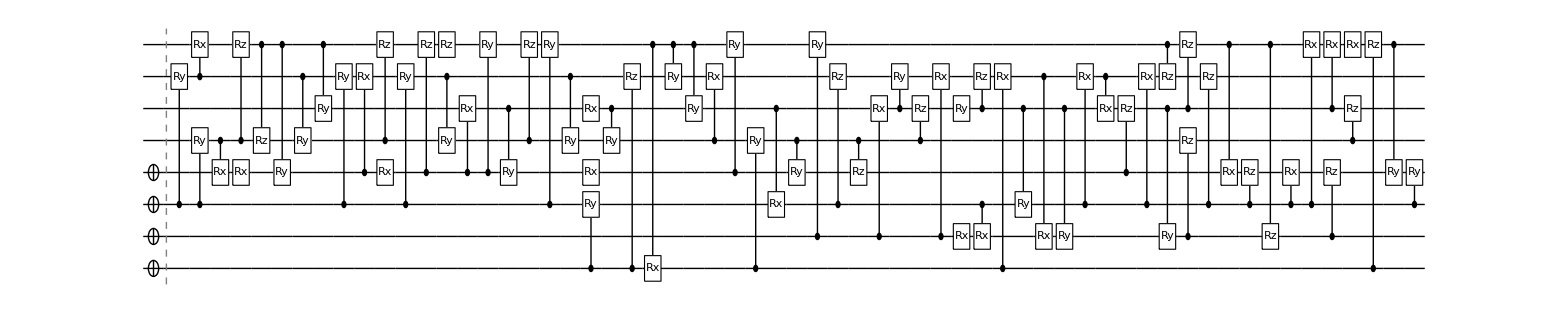

runtime=5.99483 hours

nansatz=73

nansatz/cycle={0,10,11,14,25,30,38,36,40,48,47,55,50,59,73,73}

<E>/cycle={-1.82914,-1.88136,-1.93441,-1.95084,-1.97453,-1.97626,-1.97733,-1.97794,-1.97821,-1.97855,-1.97873,-1.97895,-1.98155,-1.99427,-1.996,-1.996}

ϵ/cycle={0.167013,0.114792,0.0617419,0.0453076,0.0216184,0.0198939,0.018817,0.0182103,0.0179406,0.0176007,0.0174178,0.0171962,0.0145955,0.00188237,0.000149321,0.000149321}

<E>=-1.996

<E>-E_gs=0.000149321

Trial 2

Fri 11 Feb 2022 07:09:52GMT

target: -1.99615

@cycle1, fev:476, <E>: -1.848482789713605 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 15, 12, 6, 0}

@cycle2, fev:1698, <E>: -1.8663253551786783 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 31, 16, 10, 0}

@cycle3, fev:3300, <E>: -1.8885534890317457 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 46, 21, 15, 0}

@cycle4, fev:5605, <E>: -1.9234321868888422 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 55, 30, 19, 0}

@cycle5, fev:8471, <E>: -1.930592367959371 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 68, 34, 27, 0}

@cycle6, fev:11397, <E>: -1.931051119872051 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 83, 39, 33, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 7

@cycle7, fev:11756, <E>: -1.931051119872051 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 83, 39, 33, 0}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 8

@cycle8, fev:12161, <E>: -1.931051119872051 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 83, 39, 33, 0}

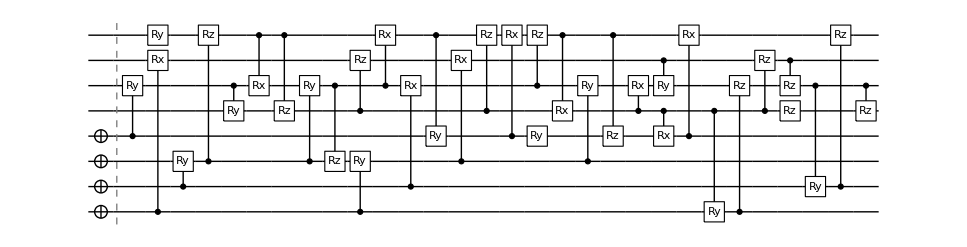

runtime=0.949892 hours

nansatz=35

nansatz/cycle={0,7,13,18,26,31,35,35}

<E>/cycle={-1.82914,-1.84848,-1.86633,-1.88855,-1.92343,-1.93059,-1.93105,-1.93105}

ϵ/cycle={0.167013,0.147668,0.129825,0.107597,0.0727181,0.065558,0.0650992,0.0650988}

<E>=-1.93105

<E>-E_gs=0.0650988

Trial 3

Fri 11 Feb 2022 08:06:52GMT

target: -1.99615

@cycle1, fev:1371, <E>: -1.8769956456362773 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 0}

@cycle2, fev:2403, <E>: -1.9069152378804706 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 31, 3, 24, 0}

@cycle3, fev:4009, <E>: -1.9102090791608004 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 44, 9, 31, 0}

@cycle4, fev:5279, <E>: -1.9731753363711781 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 60, 9, 45, 0}

@cycle5, fev:6900, <E>: -1.9762407835141331 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 70, 15, 55, 0}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 6

@cycle6, fev:7191, <E>: -1.9762407835141331 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 70, 15, 55, 1}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 7

@cycle7, fev:7587, <E>: -1.9762407835141331 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 70, 15, 55, 1}

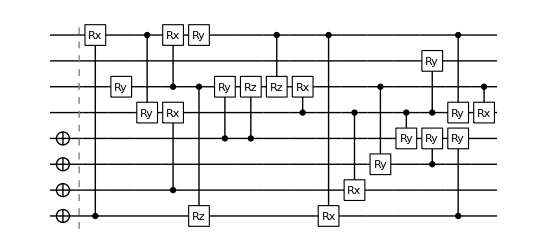

runtime=0.431568 hours

nansatz=20

nansatz/cycle={0,17,12,16,16,20,20}

<E>/cycle={-1.82914,-1.877,-1.90692,-1.91021,-1.97318,-1.97624,-1.97624}

ϵ/cycle={0.167013,0.119155,0.0892351,0.0859412,0.022975,0.0199095,0.0199095}

<E>=-1.97624

<E>-E_gs=0.0199095

Trial 4

Fri 11 Feb 2022 08:32:46GMT

target: -1.99615

@cycle1, fev:459, <E>: -1.8481750035913496 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 9, 0}

@cycle2, fev:1853, <E>: -1.85317790823549 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 37, 6, 13, 0}

@cycle3, fev:3524, <E>: -1.8763230047629564 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 51, 10, 19, 0}

@cycle4, fev:5647, <E>: -1.9140007115529887 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 64, 22, 22, 2}

@cycle5, fev:7805, <E>: -1.9565255847884435 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 83, 24, 29, 1}

@cycle6, fev:10609, <E>: -1.9640157838229517 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 90, 34, 34, 0}

@cycle7, fev:13841, <E>: -1.9929120191528904 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 98, 45, 41, 0}

@cycle8, fev:17983, <E>: -1.9952891880608594 nansatz: 43 merged-smallθ-metric-bf-gmerged: {0, 104, 46, 55, 0}

@cycle9, fev:22112, <E>: -1.9955653287554804 nansatz: 48 merged-smallθ-metric-bf-gmerged: {0, 111, 53, 65, 0}

@cycle10, fev:27226, <E>: -1.995965043856744 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 119, 58, 70, 1}

@cycle11, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 11

@cycle11, fev:28018, <E>: -1.995965043856744 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 119, 58, 70, 0}

@cycle12, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 12

@cycle12, fev:28954, <E>: -1.995965043856744 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 119, 58, 70, 0}

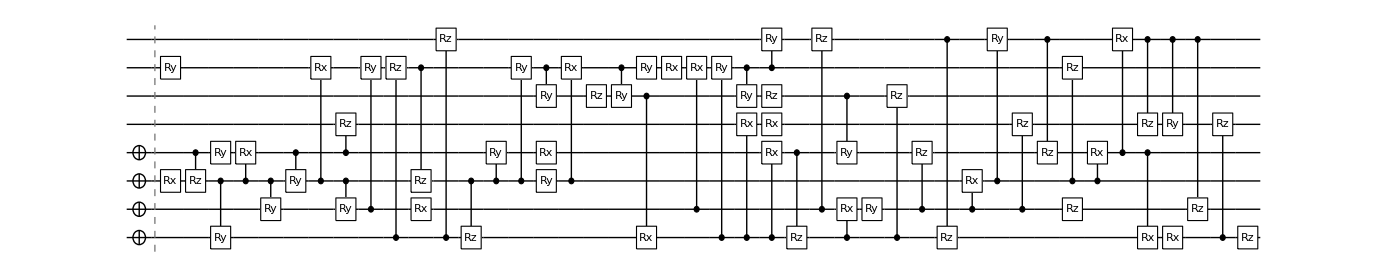

runtime=2.43825 hours

nansatz=59

nansatz/cycle={0,7,14,19,21,23,31,35,43,48,59,59}

<E>/cycle={-1.82914,-1.84818,-1.85318,-1.87632,-1.914,-1.95653,-1.96402,-1.99291,-1.99529,-1.99557,-1.99597,-1.99597}

ϵ/cycle={0.167013,0.147975,0.142972,0.119827,0.0821496,0.0396247,0.0321345,0.00323831,0.000861137,0.000584997,0.000185282,0.000185282}

<E>=-1.99597

<E>-E_gs=0.000185282

Trial 5

Fri 11 Feb 2022 10:59:04GMT

target: -1.99615

@cycle1, fev:949, <E>: -1.8951750029076595 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 10, 8, 8, 0}

@cycle2, fev:2463, <E>: -1.9179971491547498 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 25, 11, 14, 0}

@cycle3, fev:4677, <E>: -1.9196242105018073 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 37, 14, 21, 0}

@cycle4, fev:7422, <E>: -1.9233663636994907 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 50, 19, 32, 0}

@cycle5, fev:9783, <E>: -1.9235730360531955 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 59, 32, 40, 1}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 6

@cycle6, fev:10091, <E>: -1.9235730360531955 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 59, 32, 40, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 7

@cycle7, fev:10454, <E>: -1.9235730360531955 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 59, 32, 40, 0}

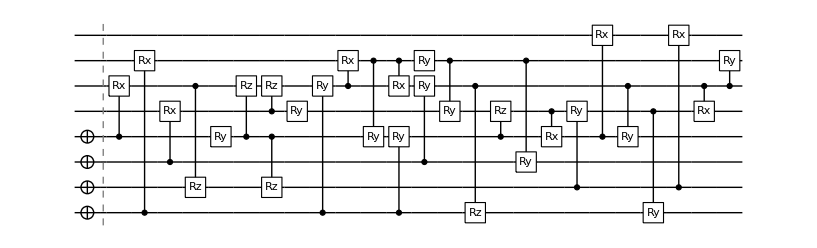

runtime=0.758065 hours

nansatz=28

nansatz/cycle={0,13,19,27,28,28,28}

<E>/cycle={-1.82914,-1.89518,-1.918,-1.91962,-1.92337,-1.92357,-1.92358}

ϵ/cycle={0.167013,0.100975,0.0781532,0.0765261,0.072784,0.0725773,0.0725747}

<E>=-1.92358

<E>-E_gs=0.0725747

Trial 6

Fri 11 Feb 2022 11:44:33GMT

target: -1.99615

@cycle1, fev:793, <E>: -1.849966671998734 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 8, 17, 1, 0}

@cycle2, fev:2242, <E>: -1.8728904270781728 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 24, 21, 11, 1}

@cycle3, fev:4039, <E>: -1.8944838170128175 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 39, 23, 18, 0}

@cycle4, fev:6246, <E>: -1.9112505021710275 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 51, 26, 26, 0}

@cycle5, fev:8676, <E>: -1.929596086984808 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 63, 30, 38, 0}

@cycle6, fev:11395, <E>: -1.9310819054940052 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 78, 36, 44, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 7

@cycle7, fev:11712, <E>: -1.9310819054940052 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 78, 36, 44, 0}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 8

@cycle8, fev:12009, <E>: -1.9310819054940052 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 78, 36, 44, 0}

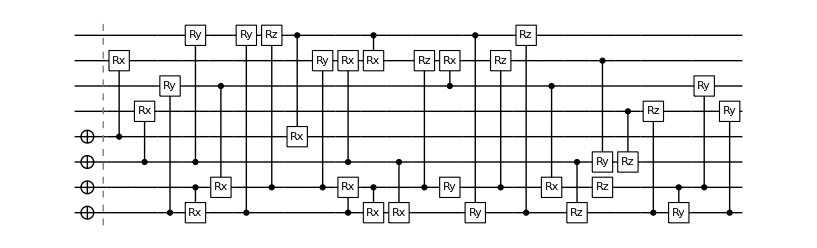

runtime=0.880985 hours

nansatz=30

nansatz/cycle={0,13,13,18,25,27,30,30}

<E>/cycle={-1.82914,-1.84997,-1.87289,-1.89448,-1.91125,-1.9296,-1.93108,-1.93108}

ϵ/cycle={0.167013,0.146184,0.12326,0.101667,0.0848998,0.0665542,0.0650684,0.0650684}

<E>=-1.93108

<E>-E_gs=0.0650684

Trial 7

Fri 11 Feb 2022 12:37:24GMT

target: -1.99615

@cycle1, fev:1238, <E>: -1.8514488840866807 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 7, 6, 0}

@cycle2, fev:3234, <E>: -1.8838287070503745 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 27, 12, 8, 0}

@cycle3, fev:5545, <E>: -1.907153835134172 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 34, 19, 20, 3}

@cycle4, fev:8372, <E>: -1.9290727070579792 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 46, 22, 33, 0}

@cycle5, fev:11170, <E>: -1.930888460160313 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 57, 24, 46, 0}

@cycle6, fev:14586, <E>: -1.9310712322824855 nansatz: 39 merged-smallθ-metric-bf-gmerged: {0, 68, 29, 53, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 7

@cycle7, fev:15035, <E>: -1.9310712322824855 nansatz: 39 merged-smallθ-metric-bf-gmerged: {0, 68, 29, 53, 1}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 8

@cycle8, fev:15467, <E>: -1.9310712322824855 nansatz: 39 merged-smallθ-metric-bf-gmerged: {0, 68, 29, 53, 0}

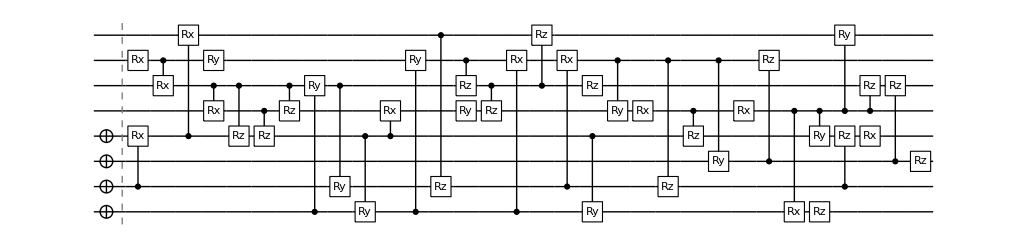

runtime=1.21605 hours

nansatz=39

nansatz/cycle={0,15,22,26,28,32,39,39}

<E>/cycle={-1.82914,-1.85145,-1.88383,-1.90715,-1.92907,-1.93089,-1.93107,-1.93107}

ϵ/cycle={0.167013,0.144701,0.112322,0.0889965,0.0670776,0.0652619,0.0650791,0.0650791}

<E>=-1.93107

<E>-E_gs=0.0650791

Trial 8

Fri 11 Feb 2022 13:50:22GMT

target: -1.99615

@cycle1, fev:712, <E>: -1.873520809051239 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 14, 13, 5, 0}

@cycle2, fev:1253, <E>: -1.8751100236030611 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 25, 21, 14, 0}

@cycle3, fev:2077, <E>: -1.9085877851596975 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 39, 29, 19, 0}

@cycle4, fev:3060, <E>: -1.9513691797484858 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 57, 34, 23, 0}

@cycle5, fev:4419, <E>: -1.9745118598964047 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 72, 42, 27, 0}

@cycle6, fev:6167, <E>: -1.9770947155547072 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 92, 46, 31, 2}

@cycle7, fev:8201, <E>: -1.9774871634156284 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 106, 50, 41, 0}

@cycle8, fev:10344, <E>: -1.9778551334702985 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 120, 52, 51, 0}

@cycle9, fev:12878, <E>: -1.9782952704760348 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 138, 52, 59, 0}

@cycle10, fev:15729, <E>: -1.983472481436855 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 152, 54, 71, 0}

@cycle11, fev:20182, <E>: -1.9859914199794313 nansatz: 37 merged-smallθ-metric-bf-gmerged: {1, 167, 59, 76, 0}

@cycle12, fev:23857, <E>: -1.9903789025442724 nansatz: 44 merged-smallθ-metric-bf-gmerged: {1, 180, 60, 85, 0}

@cycle13, fev:27713, <E>: -1.994675046440626 nansatz: 44 merged-smallθ-metric-bf-gmerged: {1, 188, 64, 103, 0}

@cycle14, fev:32124, <E>: -1.9953308621917134 nansatz: 50 merged-smallθ-metric-bf-gmerged: {1, 203, 67, 108, 0}

@cycle15, fev:36796, <E>: -1.9959120248088447 nansatz: 54 merged-smallθ-metric-bf-gmerged: {1, 216, 73, 115, 0}

@cycle16, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 16

@cycle16, fev:37521, <E>: -1.9959120248088447 nansatz: 54 merged-smallθ-metric-bf-gmerged: {1, 216, 73, 115, 0}

@cycle17, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 17

@cycle17, fev:38511, <E>: -1.9959120248088447 nansatz: 54 merged-smallθ-metric-bf-gmerged: {1, 216, 73, 115, 0}

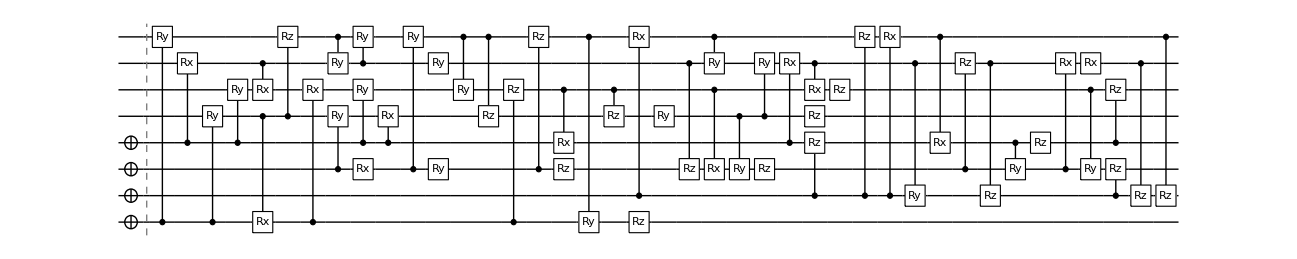

runtime=3.02943 hours

nansatz=54

nansatz/cycle={0,8,10,13,16,19,21,23,27,31,32,37,44,44,50,54,54}

<E>/cycle={-1.82914,-1.87352,-1.87511,-1.90859,-1.95137,-1.97451,-1.97709,-1.97749,-1.97786,-1.9783,-1.98347,-1.98599,-1.99038,-1.99468,-1.99533,-1.99591,-1.99591}

ϵ/cycle={0.167013,0.12263,0.12104,0.0875625,0.0447811,0.0216385,0.0190556,0.0186632,0.0182952,0.0178551,0.0126778,0.0101589,0.00577142,0.00147528,0.000819463,0.000238301,0.000238219}

<E>=-1.99591

<E>-E_gs=0.000238219

Trial 9

Fri 11 Feb 2022 16:52:08GMT

target: -1.99615

@cycle1, fev:952, <E>: -1.8751102467614273 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 22, 0}

@cycle2, fev:1707, <E>: -1.9069173558627956 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 23, 8, 27, 0}

@cycle3, fev:2852, <E>: -1.9513695516051401 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 41, 13, 28, 0}

@cycle4, fev:4730, <E>: -1.9673664568542555 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 53, 19, 34, 0}

@cycle5, fev:6852, <E>: -1.9762043882184246 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 59, 28, 45, 0}

@cycle6, fev:8912, <E>: -1.9768214715055827 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 76, 28, 57, 0}

@cycle7, fev:11364, <E>: -1.9776584982844214 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 84, 37, 69, 0}

@cycle8, fev:14123, <E>: -1.9781065267199627 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 100, 39, 78, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 9

@cycle9, fev:14381, <E>: -1.9781065267199627 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 100, 39, 78, 0}

@cycle10, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 10

@cycle10, fev:14959, <E>: -1.9781065267199627 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 100, 39, 78, 0}

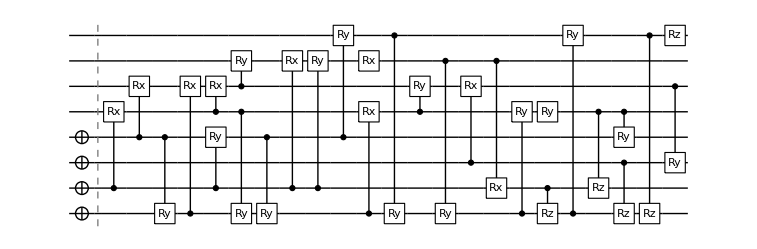

runtime=1.05789 hours

nansatz=29

nansatz/cycle={0,11,9,14,20,24,25,26,29,29}

<E>/cycle={-1.82914,-1.87511,-1.90692,-1.95137,-1.96737,-1.9762,-1.97682,-1.97766,-1.97811,-1.97811}

ϵ/cycle={0.167013,0.12104,0.089233,0.0447808,0.0287839,0.0199459,0.0193289,0.0184918,0.0180438,0.0180437}

<E>=-1.97811

<E>-E_gs=0.0180437

Trial 10

Fri 11 Feb 2022 17:55:37GMT

target: -1.99615

@cycle1, fev:1282, <E>: -1.8706279023345027 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 7, 11, 6, 0}

@cycle2, fev:2844, <E>: -1.8735476080125155 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 19, 16, 17, 1}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 3

@cycle3, fev:3176, <E>: -1.8735476080125155 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 19, 16, 17, 2}

@cycle4, fev:5119, <E>: -1.9003120368228306 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 35, 30, 19, 0}

@cycle5, fev:7680, <E>: -1.9257111134773852 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 51, 36, 27, 0}

@cycle6, fev:10486, <E>: -1.9306246758901133 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 67, 38, 40, 0}

@cycle7, fev:14146, <E>: -1.9310519800114379 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 75, 46, 58, 0}

@cycle8, fev:17411, <E>: -1.9752295044745518 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 94, 51, 72, 0}

@cycle9, fev:21052, <E>: -1.9935437555212623 nansatz: 39 merged-smallθ-metric-bf-gmerged: {0, 110, 55, 80, 0}

@cycle10, fev:26885, <E>: -1.9953448343526747 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 117, 66, 90, 0}

@cycle11, fev:31739, <E>: -1.9959087386279637 nansatz: 52 merged-smallθ-metric-bf-gmerged: {0, 134, 71, 98, 1}

@cycle12, fev:37648, <E>: -1.9961006872574607 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 147, 73, 111, 1}

@cycle13, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 13

@cycle13, fev:38575, <E>: -1.9961006872574607 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 147, 73, 111, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 53 @cycle 14

@cycle14, fev:39560, <E>: -1.9961006872574607 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 147, 73, 111, 0}

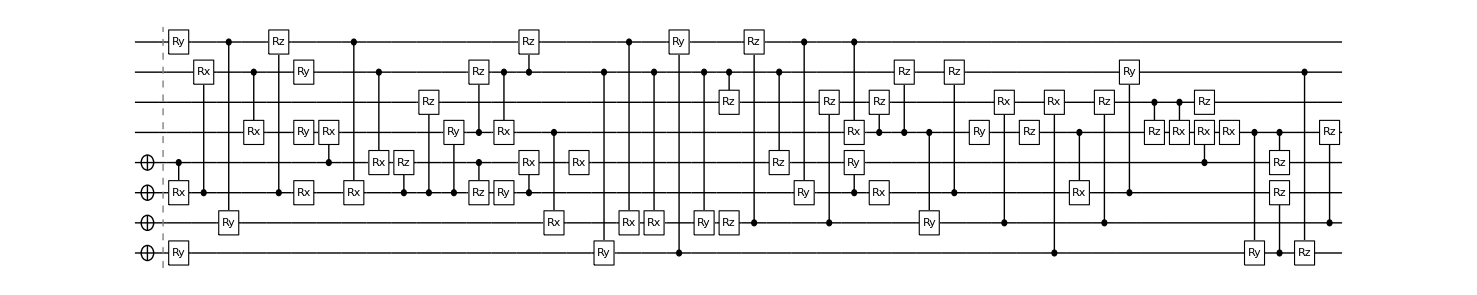

runtime=3.37484 hours

nansatz=59

nansatz/cycle={0,16,17,21,27,32,34,31,39,47,52,59,59}

<E>/cycle={-1.82914,-1.87063,-1.87355,-1.90031,-1.92571,-1.93062,-1.93105,-1.97523,-1.99354,-1.99534,-1.99591,-1.9961,-1.9961}

ϵ/cycle={0.167013,0.125522,0.122603,0.0958383,0.0704392,0.0655256,0.0650983,0.0209208,0.00260657,0.000805491,0.000241587,0.0000496383,0.0000496383}

<E>=-1.9961

<E>-E_gs=0.0000496383

{-1.996,-1.93105,-1.97624,-1.99597,-1.92358,-1.93108,-1.93107,-1.99591,-1.97811,-1.9961}

```mathematica
results={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[nqubits,hamiltonian,conf]];

Print@DrawCircuit[{conf["ansatzinit"],ansatz},nqubits];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
DestroyAllQuregs[];
AppendTo[results,{ansatz,θvars,timing,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

## Total results

```mathematica
{ψ,ψwork}=CreateQuregs[nqubits,2];
ansatzinit=conf["ansatzinit"];
chemacc=1.59*10^-3;
trial=1;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧/60,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp1,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
```

```mathematica
disp1//TableForm
```

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
1 | 359.69 | True | 0.000149321 | 73 | {0, 249, 44, 188} | 63182 | {0, 10, 11, 14, 25, 30, 38, 36, 40, 48, 47, 55, 50, 59, 73, 73} | {}
2 | 56.9935 | False | 0.0650988 | 35 | {0, 83, 39, 33} | 13219 | {0, 7, 13, 18, 26, 31, 35, 35} | {}
3 | 25.8941 | False | 0.0199095 | 20 | {0, 70, 15, 55} | 8140 | {0, 17, 12, 16, 16, 20, 20} | {}
4 | 146.295 | True | 0.000185282 | 59 | {0, 119, 58, 70} | 30732 | {0, 7, 14, 19, 21, 23, 31, 35, 43, 48, 59, 59} | {}
5 | 45.4839 | False | 0.0725747 | 28 | {0, 59, 32, 40} | 11304 | {0, 13, 19, 27, 28, 28, 28} | {}
6 | 52.8591 | False | 0.0650684 | 30 | {0, 78, 36, 44} | 12914 | {0, 13, 13, 18, 25, 27, 30, 30} | {}
7 | 72.9632 | False | 0.0650791 | 39 | {0, 68, 29, 53} | 16645 | {0, 15, 22, 26, 28, 32, 39, 39} | {}
8 | 181.766 | True | 0.000238219 | 54 | {1, 216, 73, 115} | 40139 | {0, 8, 10, 13, 16, 19, 21, 23, 27, 31, 32, 37, 44, 44, 50, 54, 54} | {}
9 | 63.4737 | False | 0.0180437 | 29 | {0, 100, 39, 78} | 15807 | {0, 11, 9, 14, 20, 24, 25, 26, 29, 29} | {}
10 | 202.491 | True | 0.0000496383 | 59 | {0, 147, 73, 111} | 41338 | {0, 16, 17, 21, 27, 32, 34, 31, 39, 47, 52, 59, 59} | {}

```mathematica
results
```

{{{C_2[Ry_6[θ_508]],C_2[Ry_4[θ_511]],C_6[Rx_7[θ_512]],C_4[Rx_3[θ_515]],Rx_3[θ_522],C_4[Rz_7[θ_519]],C_7[Rz_4[θ_530]],C_7[Ry_3[θ_534]],C_6[Ry_4[θ_531]],C_7[Ry_5[θ_536]],C_2[Ry_6[θ_535]],C_3[Rx_6[θ_540]],C_4[Rz_7[θ_545]],Rx_3[θ_542],C_2[Ry_6[θ_282]],C_3[Rz_7[θ_546]],C_6[Ry_4[θ_289]],Rz_7[θ_550],C_3[Rx_5[θ_266]],C_3[Ry_7[θ_272]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],Rx_5[θ_451],Rx_3[θ_379],C_0[Ry_2[θ_452]],C_5[Ry_4[θ_29]],C_0[Rz_6[θ_366]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_7[Ry_5[θ_490]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_5[Rx_2[θ_496]],C_4[Ry_3[θ_75]],C_1[Ry_7[θ_197]],C_2[Rz_6[θ_465]],C_4[Rz_3[θ_450]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],Rx_1[θ_463],C_5[Rz_6[θ_114]],C_2[Rx_1[θ_453]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_6[Rx_5[θ_375]],C_3[Rz_5[θ_489]],C_2[Rx_6[θ_337]],C_5[Ry_1[θ_183]],C_7[Rz_6[θ_483]],C_1[Rz_4[θ_320]],C_5[Rz_7[θ_493]],C_2[Rz_6[θ_342]],C_7[Rx_3[θ_402]],C_2[Rz_3[θ_484]],C_7[Rz_1[θ_478]],C_2[Rx_3[θ_406]],C_2[Rx_7[θ_410]],C_1[Rz_3[θ_469]],C_5[Rx_7[θ_426]],Rx_7[θ_429],C_4[Rz_5[θ_466]],C_0[Rz_7[θ_430]],C_7[Ry_3[θ_435]],C_2[Ry_3[θ_437]]},<|θ_14→-3.13947,θ_19→-3.14159,θ_29→-4.60927,θ_30→3.14159,θ_41→-1.57081,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14182,θ_97→4.62776,θ_110→1.57054,θ_114→3.81545,θ_117→0.795343,θ_125→-2.83697,θ_127→-3.58695,θ_134→3.00935,θ_163→-3.14159,θ_183→-3.14159,θ_197→-3.14159,θ_216→1.57058,θ_218→3.14159,θ_220→-3.14185,θ_223→3.0945,θ_266→3.13549,θ_272→-3.1078,θ_282→2.86386,θ_289→4.56908,θ_298→4.88739,θ_306→-3.14159,θ_320→2.99087,θ_337→3.14159,θ_342→-5.43769,θ_366→2.26727,θ_375→0.53241,θ_379→-3.1002,θ_402→3.14159,θ_406→-3.14159,θ_410→-3.14025,θ_426→-3.14378,θ_429→3.07695,θ_430→4.45313,θ_435→3.14159,θ_437→-3.14159,θ_450→-4.07367,θ_451→-0.570353,θ_452→-3.14177,θ_453→-3.14159,θ_463→3.14159,θ_465→0.917153,θ_466→6.91062,θ_469→-0.684257,θ_478→3.18867,θ_483→1.33666,θ_484→-3.556,θ_489→-3.61816,θ_490→4.57129,θ_493→1.67753,θ_496→3.14167,θ_508→0.833542,θ_511→-1.01649,θ_512→0.487199,θ_515→1.02674,θ_519→1.49455,θ_522→1.0326,θ_530→2.90121,θ_531→1.43306,θ_534→-1.90982,θ_535→-2.74878,θ_536→-0.554979,θ_540→-0.775649,θ_542→-1.2269,θ_545→-1.75013,θ_546→-3.20131,θ_550→4.16552|>,21581.4,<|ansatz→{{},{C_3[Ry_5[θ_11]],C_5[Ry_3[θ_31]],C_5[Ry_4[θ_29]],C_3[Ry_5[θ_20]],C_5[Rz_1[θ_2]],C_5[Ry_6[θ_14]],C_6[Rx_1[θ_19]],C_5[Ry_2[θ_30]],C_0[Rz_2[θ_32]],C_1[Rz_6[θ_22]]},{C_3[Ry_5[θ_11]],C_2[Rx_7[θ_55]],C_5[Ry_3[θ_31]],C_7[Rx_0[θ_54]],C_5[Ry_4[θ_29]],C_3[Ry_5[θ_20]],C_5[Ry_6[θ_14]],Ry_5[θ_41],C_6[Rx_1[θ_19]],C_5[Ry_2[θ_30]],C_1[Rz_6[θ_22]]},{C_1[Ry_6[θ_81]],C_3[Ry_5[θ_11]],C_2[Rx_7[θ_55]],C_7[Rx_0[θ_54]],C_5[Ry_4[θ_29]],C_3[Ry_5[θ_20]],C_0[Ry_4[θ_97]],C_5[Ry_6[θ_14]],C_4[Ry_3[θ_75]],Ry_5[θ_41],C_1[Rz_6[θ_90]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]]},{C_1[Ry_6[θ_81]],C_3[Ry_5[θ_11]],C_6[Ry_4[θ_125]],C_2[Rz_6[θ_107]],C_5[Ry_4[θ_29]],C_2[Rx_7[θ_55]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_6[Rx_5[θ_119]],C_0[Ry_4[θ_97]],C_6[Rz_7[θ_103]],C_1[Rx_5[θ_110]],C_4[Ry_3[θ_75]],C_5[Ry_6[θ_14]],C_5[Rz_2[θ_118]],C_1[Rz_6[θ_90]],Ry_5[θ_41],C_1[Rz_4[θ_113]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_7[Rz_2[θ_115]],C_5[Rz_1[θ_123]],C_6[Rx_1[θ_19]]},{C_2[Ry_7[θ_134]],Ry_5[θ_140],Rx_4[θ_147],C_1[Ry_6[θ_81]],C_4[Rz_5[θ_158]],C_3[Ry_5[θ_11]],C_4[Rx_7[θ_160]],C_6[Ry_4[θ_125]],C_2[Rz_6[θ_107]],C_5[Ry_4[θ_29]],C_2[Rx_7[θ_55]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_6[Rx_5[θ_119]],C_0[Ry_4[θ_97]],C_6[Rz_7[θ_103]],C_1[Rx_5[θ_110]],C_4[Ry_3[θ_75]],C_5[Ry_6[θ_14]],C_5[Rz_2[θ_118]],C_1[Rz_6[θ_90]],Ry_5[θ_41],C_1[Rz_4[θ_113]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_7[Rz_2[θ_115]],C_5[Rz_1[θ_123]],C_6[Rx_1[θ_19]]},{C_2[Ry_7[θ_134]],Ry_5[θ_140],Rx_4[θ_147],C_1[Ry_6[θ_81]],C_4[Rz_5[θ_158]],C_3[Ry_5[θ_11]],C_4[Rx_7[θ_160]],C_6[Ry_4[θ_125]],C_2[Rz_6[θ_107]],C_5[Ry_4[θ_29]],C_2[Rx_7[θ_55]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_6[Rx_5[θ_119]],C_0[Ry_4[θ_97]],C_6[Rz_7[θ_103]],C_1[Rx_5[θ_110]],C_4[Ry_3[θ_75]],C_5[Ry_6[θ_14]],C_3[Rz_7[θ_175]],C_5[Rz_2[θ_118]],C_1[Rz_6[θ_90]],C_7[Rz_3[θ_178]],Ry_5[θ_41],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],Rz_0[θ_161],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_3[Rz_6[θ_186]],C_4[Rx_5[θ_169]],C_5[Ry_1[θ_177]],Rx_5[θ_179],C_5[Ry_1[θ_183]],C_4[Rx_5[θ_185]],C_3[Rz_5[θ_188]]},{C_2[Ry_7[θ_134]],Ry_5[θ_140],C_1[Ry_6[θ_81]],C_5[Ry_3[θ_223]],C_7[Rx_0[θ_54]],C_6[Rz_5[θ_221]],C_3[Ry_5[θ_11]],C_6[Ry_4[θ_125]],C_5[Ry_4[θ_29]],C_7[Ry_6[θ_127]],C_6[Ry_3[θ_203]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_4[Ry_3[θ_75]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_3[Rz_0[θ_209]],C_1[Rx_6[θ_216]],C_4[Rz_5[θ_220]],Ry_5[θ_41],C_3[Rz_6[θ_205]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],Rz_0[θ_161],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_3[Rz_6[θ_186]],C_4[Rx_5[θ_169]],C_0[Rz_3[θ_222]],C_5[Ry_1[θ_177]],Rx_5[θ_179],C_5[Ry_1[θ_183]],C_3[Rz_5[θ_188]]},{C_2[Ry_7[θ_134]],Ry_5[θ_140],C_1[Ry_6[θ_81]],C_7[Rx_0[θ_54]],C_5[Ry_3[θ_223]],C_6[Rz_5[θ_221]],C_3[Ry_5[θ_11]],C_6[Ry_4[θ_125]],C_5[Ry_4[θ_29]],C_7[Ry_6[θ_127]],C_6[Ry_3[θ_203]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_6[Rz_4[θ_229]],C_1[Rx_5[θ_110]],C_6[Rz_0[θ_250]],C_3[Ry_4[θ_238]],C_7[Rz_3[θ_253]],C_5[Ry_6[θ_14]],C_4[Ry_3[θ_75]],C_1[Rx_6[θ_216]],C_3[Rz_0[θ_209]],C_4[Rz_5[θ_220]],Ry_5[θ_41],C_3[Rz_6[θ_205]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_3[Rz_6[θ_186]],C_2[Rz_1[θ_247]],C_5[Ry_1[θ_163]],C_0[Rz_3[θ_222]],C_4[Rx_5[θ_169]],C_5[Ry_1[θ_177]],Rx_5[θ_179],C_5[Ry_1[θ_183]],C_3[Rz_5[θ_188]]},{C_3[Rx_5[θ_266]],C_2[Ry_6[θ_282]],C_3[Ry_7[θ_272]],C_5[Rz_4[θ_283]],C_5[Rz_6[θ_287]],C_6[Ry_4[θ_289]],C_7[Rz_5[θ_295]],C_1[Ry_4[θ_292]],Ry_5[θ_140],C_4[Rz_7[θ_298]],C_1[Ry_6[θ_81]],C_5[Ry_3[θ_223]],C_2[Ry_7[θ_134]],C_6[Rz_5[θ_221]],C_7[Rx_0[θ_54]],C_3[Ry_5[θ_11]],C_6[Ry_4[θ_125]],C_5[Ry_4[θ_29]],C_7[Ry_6[θ_127]],C_6[Ry_3[θ_203]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_6[Rz_4[θ_229]],C_1[Rx_5[θ_110]],C_3[Ry_4[θ_238]],C_5[Ry_6[θ_14]],C_7[Rz_3[θ_253]],C_1[Rx_6[θ_216]],C_4[Ry_3[θ_75]],C_3[Rz_0[θ_209]],C_4[Rz_5[θ_220]],Ry_5[θ_41],C_3[Rz_6[θ_205]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_3[Rz_6[θ_186]],C_2[Rz_1[θ_247]],C_5[Ry_1[θ_163]],C_0[Rz_3[θ_222]],C_4[Rx_5[θ_169]],C_5[Ry_1[θ_177]],Rx_5[θ_179],C_5[Ry_1[θ_183]],C_3[Rz_5[θ_188]]},{C_3[Rx_5[θ_266]],C_2[Ry_6[θ_282]],C_3[Ry_7[θ_272]],C_5[Rz_4[θ_283]],C_5[Rz_6[θ_287]],C_6[Ry_4[θ_289]],C_7[Rz_5[θ_295]],Ry_5[θ_140],C_4[Rz_7[θ_298]],C_5[Ry_3[θ_223]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],C_7[Rx_0[θ_54]],C_3[Ry_5[θ_11]],C_5[Ry_4[θ_29]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_1[Rx_5[θ_110]],C_3[Ry_4[θ_238]],C_5[Ry_6[θ_14]],C_4[Ry_3[θ_75]],C_1[Rx_6[θ_216]],C_4[Rz_5[θ_220]],Ry_5[θ_41],C_3[Rz_6[θ_205]],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_3[Rz_6[θ_186]],C_2[Rz_1[θ_247]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_4[Rx_5[θ_169]],C_6[Ry_2[θ_309]],Rx_5[θ_179],C_2[Rz_0[θ_313]],C_4[Rz_3[θ_303]],C_5[Ry_1[θ_183]],C_2[Rz_3[θ_318]],C_1[Rz_4[θ_320]],C_2[Rx_6[θ_337]],C_3[Rz_1[θ_323]],C_2[Rz_6[θ_342]]},{C_3[Rx_5[θ_266]],C_2[Ry_6[θ_282]],C_3[Ry_7[θ_272]],C_5[Rz_4[θ_283]],C_6[Ry_4[θ_289]],C_7[Rz_5[θ_295]],Ry_5[θ_140],C_0[Rz_7[θ_356]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_6[Rz_3[θ_370]],C_2[Ry_7[θ_134]],C_3[Rz_1[θ_346]],C_6[Rx_4[θ_353]],C_3[Ry_5[θ_11]],C_6[Ry_4[θ_125]],Rx_3[θ_379],C_0[Rz_6[θ_366]],C_5[Ry_4[θ_29]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_2[Rz_6[θ_363]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_3[Ry_4[θ_238]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_4[Ry_3[θ_75]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],C_3[Rz_6[θ_205]],Rz_3[θ_359],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_3[Rz_6[θ_186]],C_2[Rz_1[θ_247]],C_1[Rz_0[θ_380]],C_2[Rx_6[θ_306]],C_4[Rz_3[θ_303]],C_5[Ry_1[θ_163]],C_6[Ry_2[θ_309]],Rz_4[θ_383],C_2[Rz_0[θ_313]],C_6[Rx_5[θ_375]],C_2[Rz_3[θ_318]],C_5[Ry_1[θ_183]],C_1[Rz_4[θ_320]],C_2[Rx_6[θ_337]],C_3[Rz_1[θ_323]],C_2[Rz_6[θ_342]]},{C_3[Rx_5[θ_266]],C_2[Ry_6[θ_282]],C_3[Ry_7[θ_272]],C_6[Ry_4[θ_289]],C_7[Rz_5[θ_295]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],Rx_3[θ_379],C_0[Rz_6[θ_366]],C_5[Ry_4[θ_29]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_1[Ry_7[θ_197]],C_1[Rx_5[θ_110]],C_4[Ry_3[θ_75]],C_5[Ry_6[θ_14]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],Rz_4[θ_383],C_5[Rz_6[θ_114]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_3[Rz_6[θ_186]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_6[Ry_2[θ_309]],C_6[Rx_5[θ_375]],C_2[Rz_3[θ_318]],C_5[Ry_1[θ_183]],C_2[Rx_6[θ_337]],C_7[Rx_3[θ_402]],C_1[Rz_4[θ_320]],C_2[Rz_6[θ_342]],C_2[Rx_3[θ_406]],C_2[Rx_7[θ_410]],C_4[Rz_7[θ_417]],C_5[Rx_7[θ_426]],Rx_7[θ_429],C_6[Rz_5[θ_431]],C_0[Rz_7[θ_430]],C_1[Rz_5[θ_439]],C_7[Ry_3[θ_435]],C_2[Ry_3[θ_437]]},{C_3[Rx_5[θ_266]],C_2[Ry_6[θ_282]],C_3[Ry_7[θ_272]],C_6[Ry_4[θ_289]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],Rx_5[θ_451],Rx_3[θ_379],C_0[Ry_2[θ_452]],C_5[Ry_4[θ_29]],C_0[Rz_6[θ_366]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_7[Ry_5[θ_490]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_5[Rx_2[θ_496]],C_4[Ry_3[θ_75]],C_1[Ry_7[θ_197]],C_2[Rz_6[θ_465]],C_4[Rz_3[θ_450]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],Rx_1[θ_463],C_5[Rz_6[θ_114]],C_2[Rx_1[θ_453]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_6[Ry_2[θ_309]],C_6[Rx_5[θ_375]],C_3[Rz_5[θ_489]],C_2[Rx_6[θ_337]],C_5[Ry_1[θ_183]],C_7[Rz_6[θ_483]],C_1[Rz_4[θ_320]],C_5[Rz_7[θ_493]],C_2[Rz_6[θ_342]],C_7[Rx_3[θ_402]],C_2[Rz_3[θ_484]],C_7[Rz_1[θ_478]],C_2[Rx_3[θ_406]],C_2[Rx_7[θ_410]],C_1[Rz_3[θ_469]],C_0[Rz_3[θ_487]],C_5[Rx_7[θ_426]],Rx_7[θ_429],C_4[Rz_5[θ_466]],C_0[Rz_7[θ_430]],C_7[Ry_3[θ_435]],C_2[Ry_3[θ_437]]},{C_2[Ry_6[θ_508]],C_2[Ry_4[θ_511]],C_6[Rx_7[θ_512]],C_4[Rx_3[θ_515]],Rx_3[θ_522],C_4[Rz_7[θ_519]],C_7[Rz_4[θ_530]],C_7[Ry_3[θ_534]],C_6[Ry_4[θ_531]],C_7[Ry_5[θ_536]],C_2[Ry_6[θ_535]],C_3[Rx_6[θ_540]],C_4[Rz_7[θ_545]],Rx_3[θ_542],C_2[Ry_6[θ_282]],C_3[Rz_7[θ_546]],C_6[Ry_4[θ_289]],Rz_7[θ_550],C_3[Rx_5[θ_266]],C_3[Ry_7[θ_272]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],Rx_5[θ_451],Rx_3[θ_379],C_0[Ry_2[θ_452]],C_5[Ry_4[θ_29]],C_0[Rz_6[θ_366]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_7[Ry_5[θ_490]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_5[Rx_2[θ_496]],C_4[Ry_3[θ_75]],C_1[Ry_7[θ_197]],C_2[Rz_6[θ_465]],C_4[Rz_3[θ_450]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],Rx_1[θ_463],C_5[Rz_6[θ_114]],C_2[Rx_1[θ_453]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_6[Rx_5[θ_375]],C_3[Rz_5[θ_489]],C_2[Rx_6[θ_337]],C_5[Ry_1[θ_183]],C_7[Rz_6[θ_483]],C_1[Rz_4[θ_320]],C_5[Rz_7[θ_493]],C_2[Rz_6[θ_342]],C_7[Rx_3[θ_402]],C_2[Rz_3[θ_484]],C_7[Rz_1[θ_478]],C_2[Rx_3[θ_406]],C_2[Rx_7[θ_410]],C_1[Rz_3[θ_469]],C_5[Rx_7[θ_426]],Rx_7[θ_429],C_4[Rz_5[θ_466]],C_0[Rz_7[θ_430]],C_7[Ry_3[θ_435]],C_2[Ry_3[θ_437]]},{C_2[Ry_6[θ_508]],C_2[Ry_4[θ_511]],C_6[Rx_7[θ_512]],C_4[Rx_3[θ_515]],Rx_3[θ_522],C_4[Rz_7[θ_519]],C_7[Rz_4[θ_530]],C_7[Ry_3[θ_534]],C_6[Ry_4[θ_531]],C_7[Ry_5[θ_536]],C_2[Ry_6[θ_535]],C_3[Rx_6[θ_540]],C_4[Rz_7[θ_545]],Rx_3[θ_542],C_2[Ry_6[θ_282]],C_3[Rz_7[θ_546]],C_6[Ry_4[θ_289]],Rz_7[θ_550],C_3[Rx_5[θ_266]],C_3[Ry_7[θ_272]],C_5[Ry_3[θ_223]],C_4[Rz_7[θ_298]],C_2[Ry_7[θ_134]],C_6[Ry_4[θ_125]],Rx_5[θ_451],Rx_3[θ_379],C_0[Ry_2[θ_452]],C_5[Ry_4[θ_29]],C_0[Rz_6[θ_366]],C_7[Rx_0[θ_54]],C_7[Ry_6[θ_127]],C_7[Ry_5[θ_490]],C_4[Rx_6[θ_117]],C_3[Ry_7[θ_218]],C_0[Ry_4[θ_97]],C_5[Rx_2[θ_496]],C_4[Ry_3[θ_75]],C_1[Ry_7[θ_197]],C_2[Rz_6[θ_465]],C_4[Rz_3[θ_450]],C_1[Rx_5[θ_110]],C_5[Ry_6[θ_14]],C_4[Rz_5[θ_220]],C_1[Rx_6[θ_216]],Ry_5[θ_41],Rx_1[θ_463],C_5[Rz_6[θ_114]],C_2[Rx_1[θ_453]],C_0[Rx_6[θ_82]],C_5[Ry_2[θ_30]],C_6[Rx_1[θ_19]],C_5[Ry_1[θ_163]],C_2[Rx_6[θ_306]],C_6[Rx_5[θ_375]],C_3[Rz_5[θ_489]],C_2[Rx_6[θ_337]],C_5[Ry_1[θ_183]],C_7[Rz_6[θ_483]],C_1[Rz_4[θ_320]],C_5[Rz_7[θ_493]],C_2[Rz_6[θ_342]],C_7[Rx_3[θ_402]],C_2[Rz_3[θ_484]],C_7[Rz_1[θ_478]],C_2[Rx_3[θ_406]],C_2[Rx_7[θ_410]],C_1[Rz_3[θ_469]],C_5[Rx_7[θ_426]],Rx_7[θ_429],C_4[Rz_5[θ_466]],C_0[Rz_7[θ_430]],C_7[Ry_3[θ_435]],C_2[Ry_3[θ_437]]}},θvars→{<||>,<|θ_2→-2.51575,θ_11→-0.559841,θ_14→0.745519,θ_19→-3.14159,θ_20→-0.597585,θ_22→3.14051,θ_29→-3.14159,θ_30→3.14159,θ_31→3.14159,θ_32→1.88336|>,<|θ_11→-1.11097,θ_14→0.711698,θ_19→-3.14159,θ_20→-3.63079,θ_22→3.13135,θ_29→-3.14159,θ_30→3.14159,θ_31→3.14159,θ_41→-1.74364,θ_54→-3.14159,θ_55→0.677782|>,<|θ_11→2.54482,θ_14→-0.785677,θ_19→-3.14159,θ_20→-6.70226,θ_29→-1.74609,θ_30→3.14159,θ_41→-1.48425,θ_54→-3.14159,θ_55→0.599914,θ_75→3.14159,θ_81→-0.480174,θ_82→0.696203,θ_90→-1.5708,θ_97→0.907989|>,<|θ_11→1.88057,θ_14→-1.30682,θ_19→-3.14159,θ_29→-2.08753,θ_30→3.14159,θ_41→-1.4636,θ_54→-3.14159,θ_55→0.610855,θ_75→3.14159,θ_81→1.69564,θ_82→1.33913,θ_90→-1.83098,θ_97→1.9791,θ_103→-1.85647,θ_107→1.56033,θ_110→1.70163,θ_113→-1.49255,θ_114→1.75414,θ_115→0.983126,θ_117→1.24387,θ_118→-1.68514,θ_119→-1.82364,θ_123→0.819764,θ_125→-1.39368,θ_127→-1.94834|>,<|θ_11→1.49049,θ_14→-1.46869,θ_19→-3.14159,θ_29→-1.81785,θ_30→3.14159,θ_41→-1.5586,θ_54→-3.14159,θ_55→0.62453,θ_75→3.14159,θ_81→1.82797,θ_82→1.76826,θ_90→-2.20282,θ_97→1.67606,θ_103→-1.86372,θ_107→1.9758,θ_110→1.43052,θ_113→-1.78652,θ_114→1.24694,θ_115→0.911591,θ_117→1.72835,θ_118→-1.69904,θ_119→-1.53719,θ_123→1.29411,θ_125→-1.56116,θ_127→-1.77345,θ_134→0.203206,θ_140→0.512573,θ_147→-0.751225,θ_158→2.71728,θ_160→-0.745692|>,<|θ_11→1.55987,θ_14→-1.45274,θ_19→-3.14158,θ_29→-1.89278,θ_30→3.14159,θ_41→-1.52286,θ_54→-3.14159,θ_55→0.646196,θ_75→3.14159,θ_81→1.76242,θ_82→1.74528,θ_90→-2.34958,θ_97→1.63989,θ_103→-1.94997,θ_107→2.05692,θ_110→1.4349,θ_114→1.14624,θ_117→1.78137,θ_118→-1.72211,θ_119→-1.60603,θ_125→-1.50022,θ_127→-1.86878,θ_134→0.182369,θ_140→0.446556,θ_147→-0.852084,θ_158→2.68167,θ_160→-0.789129,θ_161→-2.16729,θ_163→-0.867467,θ_169→-0.264601,θ_175→-2.87076,θ_177→3.99657,θ_178→4.77105,θ_179→-0.111371,θ_183→-3.13849,θ_185→0.24028,θ_186→-1.07871,θ_188→1.59718|>,<|θ_11→3.14122,θ_14→-3.14225,θ_19→-3.14164,θ_29→-2.3296,θ_30→3.14159,θ_41→-1.56989,θ_54→-3.14159,θ_75→3.14159,θ_81→-0.883639,θ_82→3.14181,θ_97→2.80764,θ_110→1.57188,θ_114→3.32083,θ_117→1.87075,θ_125→-4.51854,θ_127→-2.3908,θ_134→-0.609696,θ_140→0.0633041,θ_161→-3.49712,θ_163→-3.07482,θ_169→-0.0916493,θ_177→6.23831,θ_179→-0.0953893,θ_183→-3.16351,θ_186→-2.47591,θ_188→1.60576,θ_197→-3.14159,θ_203→0.0891905,θ_205→-2.52443,θ_209→3.34336,θ_216→1.57063,θ_218→3.14159,θ_220→-3.14219,θ_221→3.13833,θ_222→2.38781,θ_223→3.12785|>,<|θ_11→3.14142,θ_14→-3.14062,θ_19→-3.14159,θ_29→-2.43563,θ_30→3.14159,θ_41→-1.57087,θ_54→-3.14159,θ_75→3.14159,θ_81→-0.840367,θ_82→3.1413,θ_97→2.28042,θ_110→1.57066,θ_114→3.15445,θ_117→1.60971,θ_125→-3.10564,θ_127→-1.61345,θ_134→0.607046,θ_140→0.0853741,θ_163→-3.14159,θ_169→-0.0784791,θ_177→6.28319,θ_179→-0.0818114,θ_183→-3.14159,θ_186→-3.69369,θ_188→1.5434,θ_197→-3.14159,θ_203→0.146338,θ_205→-2.3008,θ_209→2.97772,θ_216→1.57064,θ_218→3.14159,θ_220→-3.14164,θ_221→3.09361,θ_222→0.932306,θ_223→3.14089,θ_229→-1.44298,θ_238→0.771505,θ_247→1.14647,θ_250→-0.594773,θ_253→1.66506|>,<|θ_11→3.14162,θ_14→-3.14119,θ_19→-3.14159,θ_29→-3.21754,θ_30→3.14159,θ_41→-1.5708,θ_54→-3.14159,θ_75→3.14159,θ_81→-1.89463,θ_82→3.1416,θ_97→2.50828,θ_110→1.57075,θ_114→3.62727,θ_117→0.946797,θ_125→-3.71114,θ_127→-1.48229,θ_134→1.01107,θ_140→0.332684,θ_163→-3.14162,θ_169→-0.0548242,θ_177→6.2832,θ_179→-0.0662938,θ_183→-3.14159,θ_186→-2.60727,θ_188→1.56798,θ_197→-3.14159,θ_203→0.337757,θ_205→-1.55555,θ_209→2.61264,θ_216→1.57088,θ_218→3.14159,θ_220→-3.14144,θ_221→4.44946,θ_222→0.901505,θ_223→3.14157,θ_229→-1.32289,θ_238→0.914355,θ_247→1.12687,θ_253→0.937897,θ_266→0.287994,θ_272→-0.516258,θ_282→0.997339,θ_283→3.04469,θ_287→-0.799273,θ_289→0.51796,θ_292→0.362453,θ_295→0.862222,θ_298→1.81706|>,<|θ_11→3.14158,θ_14→-3.14247,θ_19→-3.14159,θ_29→-3.27129,θ_30→3.14159,θ_41→-1.57065,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14146,θ_97→3.19,θ_110→1.57085,θ_114→1.74812,θ_117→2.06077,θ_125→-4.31321,θ_127→-3.01935,θ_134→2.03485,θ_140→1.79294,θ_163→-3.14159,θ_169→0.0564129,θ_179→-0.0688231,θ_183→-3.14159,θ_186→-4.45357,θ_197→-3.14159,θ_205→-1.82333,θ_216→1.57082,θ_218→3.14159,θ_220→-3.1416,θ_223→3.14083,θ_238→-0.867345,θ_247→-2.33104,θ_266→1.82923,θ_272→-1.67756,θ_282→0.619775,θ_283→3.29335,θ_287→-0.0755843,θ_289→2.08201,θ_295→0.14593,θ_298→3.64409,θ_303→1.72329,θ_306→-3.14159,θ_309→-0.0645423,θ_313→-1.31894,θ_318→0.724048,θ_320→-0.97912,θ_323→-2.01833,θ_337→3.14159,θ_342→-3.85391|>,<|θ_11→3.14159,θ_14→-3.14149,θ_19→-3.14159,θ_29→-3.20122,θ_30→3.14159,θ_41→-1.57079,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14161,θ_97→3.23543,θ_110→1.57079,θ_114→3.70473,θ_117→1.23854,θ_125→-6.35072,θ_127→-3.84256,θ_134→1.49754,θ_140→2.16449,θ_163→-3.14159,θ_183→-3.14159,θ_186→-4.19783,θ_197→-3.14159,θ_205→-1.76764,θ_216→1.5708,θ_218→3.14159,θ_220→-3.14156,θ_223→3.14157,θ_238→-0.851319,θ_247→-2.34974,θ_266→2.08914,θ_272→-1.68527,θ_282→0.581784,θ_283→3.31088,θ_289→1.29793,θ_295→0.185656,θ_298→2.9008,θ_303→2.07824,θ_306→-3.14159,θ_309→-0.063764,θ_313→-2.19766,θ_318→0.984595,θ_320→-0.616824,θ_323→-1.64785,θ_337→3.14159,θ_342→-4.84766,θ_346→4.17793,θ_353→-1.17927,θ_356→-0.523979,θ_359→-2.52227,θ_363→0.213467,θ_366→2.70215,θ_370→-1.34084,θ_375→-0.0711193,θ_379→0.108949,θ_380→2.23147,θ_383→-2.9987|>,<|θ_14→-3.14139,θ_19→-3.14159,θ_29→-3.9965,θ_30→3.14159,θ_41→-1.57079,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14157,θ_97→3.5673,θ_110→1.57082,θ_114→3.60197,θ_117→1.98612,θ_125→-5.24308,θ_127→-3.56494,θ_134→2.57131,θ_163→-3.14159,θ_183→-3.14159,θ_186→-4.06211,θ_197→-3.14159,θ_216→1.5708,θ_218→3.14159,θ_220→-3.1416,θ_223→3.16649,θ_266→3.1416,θ_272→-3.18931,θ_282→0.926037,θ_289→3.6743,θ_295→0.856111,θ_298→3.03458,θ_306→-3.14159,θ_309→-0.128008,θ_318→1.89243,θ_320→-1.61052,θ_337→3.14159,θ_342→-7.3355,θ_366→3.09296,θ_375→-0.119451,θ_379→-3.16605,θ_383→-1.50565,θ_402→3.14159,θ_406→-3.14159,θ_410→-2.30242,θ_417→-0.436305,θ_426→-2.31984,θ_429→2.34561,θ_430→1.51064,θ_431→-3.01913,θ_435→3.14159,θ_437→-3.14159,θ_439→4.69363|>,<|θ_14→-3.13381,θ_19→-3.14159,θ_29→-4.01963,θ_30→3.14159,θ_41→-1.57065,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14218,θ_97→5.04189,θ_110→1.57008,θ_114→3.74022,θ_117→1.11711,θ_125→-3.43811,θ_127→-3.16992,θ_134→3.30297,θ_163→-3.14159,θ_183→-3.14159,θ_197→-3.14159,θ_216→1.57039,θ_218→3.14159,θ_220→-3.14247,θ_223→3.10401,θ_266→3.1369,θ_272→-2.70137,θ_282→1.01438,θ_289→4.21522,θ_298→5.42329,θ_306→-3.14159,θ_309→0.123433,θ_320→2.95493,θ_337→3.14159,θ_342→-4.68742,θ_366→1.83055,θ_375→0.407805,θ_379→-3.09778,θ_402→3.14159,θ_406→-3.14159,θ_410→-3.15148,θ_426→-3.1104,θ_429→3.0934,θ_430→4.44472,θ_435→3.14159,θ_437→-3.14159,θ_450→-3.11894,θ_451→-0.401905,θ_452→-3.14195,θ_453→-3.14159,θ_463→3.14159,θ_465→0.481454,θ_466→5.8487,θ_469→-1.80078,θ_478→2.60991,θ_483→0.738368,θ_484→-4.33589,θ_487→0.170337,θ_489→-3.68857,θ_490→1.09551,θ_493→1.8597,θ_496→3.14173|>,<|θ_14→-3.13947,θ_19→-3.14159,θ_29→-4.60927,θ_30→3.14159,θ_41→-1.57081,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14182,θ_97→4.62776,θ_110→1.57054,θ_114→3.81545,θ_117→0.795343,θ_125→-2.83697,θ_127→-3.58695,θ_134→3.00935,θ_163→-3.14159,θ_183→-3.14159,θ_197→-3.14159,θ_216→1.57058,θ_218→3.14159,θ_220→-3.14185,θ_223→3.0945,θ_266→3.13549,θ_272→-3.1078,θ_282→2.86386,θ_289→4.56908,θ_298→4.88739,θ_306→-3.14159,θ_320→2.99087,θ_337→3.14159,θ_342→-5.43769,θ_366→2.26727,θ_375→0.53241,θ_379→-3.1002,θ_402→3.14159,θ_406→-3.14159,θ_410→-3.14025,θ_426→-3.14378,θ_429→3.07695,θ_430→4.45313,θ_435→3.14159,θ_437→-3.14159,θ_450→-4.07367,θ_451→-0.570353,θ_452→-3.14177,θ_453→-3.14159,θ_463→3.14159,θ_465→0.917153,θ_466→6.91062,θ_469→-0.684257,θ_478→3.18867,θ_483→1.33666,θ_484→-3.556,θ_489→-3.61816,θ_490→4.57129,θ_493→1.67753,θ_496→3.14167,θ_508→0.833542,θ_511→-1.01649,θ_512→0.487199,θ_515→1.02674,θ_519→1.49455,θ_522→1.0326,θ_530→2.90121,θ_531→1.43306,θ_534→-1.90982,θ_535→-2.74878,θ_536→-0.554979,θ_540→-0.775649,θ_542→-1.2269,θ_545→-1.75013,θ_546→-3.20131,θ_550→4.16552|>,<|θ_14→-3.13947,θ_19→-3.14159,θ_29→-4.60927,θ_30→3.14159,θ_41→-1.57081,θ_54→-3.14159,θ_75→3.14159,θ_82→3.14182,θ_97→4.62776,θ_110→1.57054,θ_114→3.81545,θ_117→0.795343,θ_125→-2.83697,θ_127→-3.58695,θ_134→3.00935,θ_163→-3.14159,θ_183→-3.14159,θ_197→-3.14159,θ_216→1.57058,θ_218→3.14159,θ_220→-3.14185,θ_223→3.0945,θ_266→3.13549,θ_272→-3.1078,θ_282→2.86386,θ_289→4.56908,θ_298→4.88739,θ_306→-3.14159,θ_320→2.99087,θ_337→3.14159,θ_342→-5.43769,θ_366→2.26727,θ_375→0.53241,θ_379→-3.1002,θ_402→3.14159,θ_406→-3.14159,θ_410→-3.14025,θ_426→-3.14378,θ_429→3.07695,θ_430→4.45313,θ_435→3.14159,θ_437→-3.14159,θ_450→-4.07367,θ_451→-0.570353,θ_452→-3.14177,θ_453→-3.14159,θ_463→3.14159,θ_465→0.917153,θ_466→6.91062,θ_469→-0.684257,θ_478→3.18867,θ_483→1.33666,θ_484→-3.556,θ_489→-3.61816,θ_490→4.57129,θ_493→1.67753,θ_496→3.14167,θ_508→0.833542,θ_511→-1.01649,θ_512→0.487199,θ_515→1.02674,θ_519→1.49455,θ_522→1.0326,θ_530→2.90121,θ_531→1.43306,θ_534→-1.90982,θ_535→-2.74878,θ_536→-0.554979,θ_540→-0.775649,θ_542→-1.2269,θ_545→-1.75013,θ_546→-3.20131,θ_550→4.16552|>},E→{-1.82914,-1.88136,-1.93441,-1.95084,-1.97453,-1.97626,-1.97733,-1.97794,-1.97821,-1.97855,-1.97873,-1.97895,-1.98155,-1.99427,-1.996,-1.996},idx→{1,41,71,101,131,161,191,227,263,299,343,396,449,502,555,555}|>,63182,{},{0,249,44,188}},{{C_3[Ry_5[θ_104]],C_0[Rx_6[θ_72]],Ry_7[θ_131],C_1[Ry_2[θ_114]],C_2[Rz_7[θ_122]],C_5[Ry_4[θ_108]],C_7[Rx_5[θ_124]],C_7[Rz_4[θ_125]],C_2[Ry_5[θ_127]],C_5[Rz_2[θ_178]],C_4[Rz_6[θ_150]],C_0[Ry_2[θ_75]],C_5[Rx_7[θ_185]],C_1[Rx_5[θ_97]],C_7[Ry_3[θ_129]],C_2[Rx_6[θ_78]],C_4[Rz_7[θ_183]],C_3[Rx_7[θ_6]],Ry_3[θ_27],C_5[Rz_7[θ_142]],C_7[Rx_4[θ_1]],C_2[Ry_5[θ_47]],C_7[Rz_3[θ_172]],C_4[Rx_5[θ_160]],C_4[Rx_3[θ_16]],C_6[Ry_5[θ_141]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_0[Rz_5[θ_48]],C_4[Rz_6[θ_161]],C_6[Rz_5[θ_180]],Rz_4[θ_132],C_5[Ry_1[θ_66]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},<|θ_1→0.605591,θ_6→-3.14159,θ_11→3.14159,θ_16→1.31937,θ_18→3.14159,θ_27→0.786191,θ_47→-1.67685,θ_48→5.63148,θ_66→3.14159,θ_67→-2.67311,θ_69→6.80209,θ_72→-3.14159,θ_75→2.66491,θ_78→3.14159,θ_97→2.60878,θ_104→0.426725,θ_108→-2.96788,θ_114→-2.45375,θ_122→-1.64218,θ_124→-3.41098,θ_125→8.67153,θ_127→-1.03356,θ_129→-3.14159,θ_131→-2.07814,θ_132→-0.816536,θ_141→2.25437,θ_142→-2.14844,θ_150→-4.1428,θ_160→-1.97611,θ_161→1.69605,θ_172→1.98697,θ_178→-0.345619,θ_180→-0.734354,θ_183→3.07388,θ_185→2.37336|>,3419.61,<|ansatz→{{},{C_3[Rx_7[θ_6]],Ry_3[θ_27],C_7[Rx_4[θ_1]],C_4[Rx_3[θ_16]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_3[Rz_6[θ_35]]},{C_3[Rx_7[θ_6]],C_2[Ry_5[θ_47]],Ry_3[θ_27],C_7[Rx_4[θ_1]],C_4[Rx_3[θ_16]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_0[Rz_5[θ_48]],C_3[Rx_5[θ_51]],C_5[Ry_1[θ_66]],C_4[Rz_3[θ_61]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},{C_0[Rx_6[θ_72]],C_3[Rx_7[θ_6]],C_0[Ry_2[θ_75]],Ry_3[θ_27],C_7[Rx_4[θ_1]],C_2[Rx_6[θ_78]],C_4[Rx_3[θ_16]],C_6[Ry_5[θ_80]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_1[Rx_5[θ_97]],C_2[Ry_5[θ_47]],C_0[Rz_5[θ_48]],C_3[Rx_5[θ_51]],C_5[Ry_1[θ_66]],C_4[Rz_3[θ_61]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},{C_3[Ry_5[θ_104]],Ry_7[θ_109],C_0[Rx_6[θ_72]],C_1[Ry_2[θ_114]],C_5[Ry_4[θ_108]],C_2[Rz_7[θ_122]],C_7[Rx_5[θ_124]],C_7[Rz_4[θ_125]],C_2[Ry_5[θ_127]],C_7[Ry_3[θ_129]],C_0[Ry_2[θ_75]],C_1[Rx_5[θ_97]],C_3[Rx_7[θ_6]],C_2[Rx_6[θ_78]],Ry_3[θ_27],C_7[Rx_4[θ_1]],C_2[Ry_5[θ_47]],C_4[Rx_3[θ_16]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_0[Rz_5[θ_48]],C_3[Rx_5[θ_51]],C_5[Ry_1[θ_66]],C_4[Rz_3[θ_61]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},{C_3[Ry_5[θ_104]],C_0[Rx_6[θ_72]],C_1[Ry_2[θ_114]],Ry_7[θ_131],C_0[Rx_4[θ_158]],C_2[Rz_7[θ_122]],C_5[Ry_4[θ_108]],C_7[Rx_5[θ_124]],C_7[Rz_4[θ_125]],C_2[Ry_5[θ_127]],C_0[Ry_2[θ_75]],C_1[Rx_5[θ_97]],C_4[Rz_6[θ_150]],C_7[Ry_3[θ_129]],C_2[Rx_6[θ_78]],C_3[Rx_7[θ_6]],Ry_3[θ_27],C_5[Rz_7[θ_142]],C_7[Rx_4[θ_1]],C_2[Ry_5[θ_47]],C_4[Rx_5[θ_160]],C_4[Rx_3[θ_16]],C_6[Ry_5[θ_141]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],Rz_6[θ_157],C_0[Rz_5[θ_48]],Rz_4[θ_132],C_5[Ry_1[θ_66]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},{C_3[Ry_5[θ_104]],C_0[Rx_6[θ_72]],Ry_7[θ_131],C_1[Ry_2[θ_114]],C_2[Rz_7[θ_122]],C_5[Ry_4[θ_108]],C_7[Rx_5[θ_124]],C_7[Rz_4[θ_125]],C_2[Ry_5[θ_127]],C_5[Rz_2[θ_178]],C_4[Rz_6[θ_150]],C_0[Ry_2[θ_75]],C_5[Rx_7[θ_185]],C_1[Rx_5[θ_97]],C_7[Ry_3[θ_129]],C_2[Rx_6[θ_78]],C_4[Rz_7[θ_183]],C_3[Rx_7[θ_6]],Ry_3[θ_27],C_5[Rz_7[θ_142]],C_7[Rx_4[θ_1]],C_2[Ry_5[θ_47]],C_7[Rz_3[θ_172]],C_4[Rx_5[θ_160]],C_4[Rx_3[θ_16]],C_6[Ry_5[θ_141]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_0[Rz_5[θ_48]],C_4[Rz_6[θ_161]],C_6[Rz_5[θ_180]],Rz_4[θ_132],C_5[Ry_1[θ_66]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]},{C_3[Ry_5[θ_104]],C_0[Rx_6[θ_72]],Ry_7[θ_131],C_1[Ry_2[θ_114]],C_2[Rz_7[θ_122]],C_5[Ry_4[θ_108]],C_7[Rx_5[θ_124]],C_7[Rz_4[θ_125]],C_2[Ry_5[θ_127]],C_5[Rz_2[θ_178]],C_4[Rz_6[θ_150]],C_0[Ry_2[θ_75]],C_5[Rx_7[θ_185]],C_1[Rx_5[θ_97]],C_7[Ry_3[θ_129]],C_2[Rx_6[θ_78]],C_4[Rz_7[θ_183]],C_3[Rx_7[θ_6]],Ry_3[θ_27],C_5[Rz_7[θ_142]],C_7[Rx_4[θ_1]],C_2[Ry_5[θ_47]],C_7[Rz_3[θ_172]],C_4[Rx_5[θ_160]],C_4[Rx_3[θ_16]],C_6[Ry_5[θ_141]],C_3[Rx_7[θ_11]],C_4[Ry_0[θ_18]],C_0[Rz_5[θ_48]],C_4[Rz_6[θ_161]],C_6[Rz_5[θ_180]],Rz_4[θ_132],C_5[Ry_1[θ_66]],C_1[Rz_7[θ_67]],C_5[Rz_4[θ_69]]}},θvars→{<||>,<|θ_1→0.335999,θ_6→-3.13979,θ_11→3.13976,θ_16→3.14159,θ_18→3.14159,θ_27→-0.0523196,θ_35→-3.14159|>,<|θ_1→0.644898,θ_6→-3.14159,θ_11→3.14159,θ_16→1.42832,θ_18→3.14159,θ_27→-0.232332,θ_47→-0.805718,θ_48→1.4517,θ_51→-0.96732,θ_61→1.54579,θ_66→3.14159,θ_67→-1.76012,θ_69→3.84907|>,<|θ_1→0.557146,θ_6→-3.14159,θ_11→3.14159,θ_16→1.46973,θ_18→3.14159,θ_27→-0.198748,θ_47→-0.777196,θ_48→2.34914,θ_51→-1.09745,θ_61→0.796665,θ_66→3.14159,θ_67→-2.50187,θ_69→5.0168,θ_72→-3.1416,θ_75→0.384612,θ_78→3.1416,θ_80→1.51018,θ_97→-0.64659|>,<|θ_1→0.361212,θ_6→-3.14159,θ_11→3.14159,θ_16→3.06242,θ_18→3.14159,θ_27→0.968435,θ_47→-1.77809,θ_48→2.81554,θ_51→-0.667163,θ_61→0.425848,θ_66→3.14159,θ_67→-2.44561,θ_69→6.64633,θ_72→-3.14159,θ_75→3.62625,θ_78→3.14159,θ_97→0.855399,θ_104→2.16883,θ_108→-0.520656,θ_109→-1.24653,θ_114→-2.75802,θ_122→-3.9244,θ_124→1.23023,θ_125→1.89395,θ_127→-2.77718,θ_129→-3.14159|>,<|θ_1→0.625592,θ_6→-3.14159,θ_11→3.14159,θ_16→2.07279,θ_18→3.14159,θ_27→1.49572,θ_47→-1.7185,θ_48→3.48688,θ_66→3.14159,θ_67→-3.53517,θ_69→5.85793,θ_72→-3.14159,θ_75→3.565,θ_78→3.14159,θ_97→2.3671,θ_104→1.35676,θ_108→-0.832397,θ_114→-2.71542,θ_122→-4.36599,θ_124→-3.53614,θ_125→6.50685,θ_127→-3.19394,θ_129→-3.14159,θ_131→-1.46492,θ_132→1.78939,θ_141→1.98252,θ_142→-0.337758,θ_150→-4.15131,θ_157→-0.263257,θ_158→0.799813,θ_160→-1.16335|>,<|θ_1→0.60562,θ_6→-3.14159,θ_11→3.14159,θ_16→1.31883,θ_18→3.14159,θ_27→0.786086,θ_47→-1.67486,θ_48→5.63131,θ_66→3.14159,θ_67→-2.67296,θ_69→6.80168,θ_72→-3.14159,θ_75→2.66538,θ_78→3.14159,θ_97→2.60972,θ_104→0.42682,θ_108→-2.96742,θ_114→-2.4541,θ_122→-1.64345,θ_124→-3.41046,θ_125→8.66958,θ_127→-1.03425,θ_129→-3.14159,θ_131→-2.07878,θ_132→-0.8165,θ_141→2.25521,θ_142→-2.14677,θ_150→-4.13882,θ_160→-1.97659,θ_161→1.69528,θ_172→1.98671,θ_178→-0.345746,θ_180→-0.733915,θ_183→3.07055,θ_185→2.37362|>,<|θ_1→0.605591,θ_6→-3.14159,θ_11→3.14159,θ_16→1.31937,θ_18→3.14159,θ_27→0.786191,θ_47→-1.67685,θ_48→5.63148,θ_66→3.14159,θ_67→-2.67311,θ_69→6.80209,θ_72→-3.14159,θ_75→2.66491,θ_78→3.14159,θ_97→2.60878,θ_104→0.426725,θ_108→-2.96788,θ_114→-2.45375,θ_122→-1.64218,θ_124→-3.41098,θ_125→8.67153,θ_127→-1.03356,θ_129→-3.14159,θ_131→-2.07814,θ_132→-0.816536,θ_141→2.25437,θ_142→-2.14844,θ_150→-4.1428,θ_160→-1.97611,θ_161→1.69605,θ_172→1.98697,θ_178→-0.345619,θ_180→-0.734354,θ_183→3.07388,θ_185→2.37336|>},E→{-1.82914,-1.84848,-1.86633,-1.88855,-1.92343,-1.93059,-1.93105,-1.93105},idx→{1,41,71,101,131,161,191,191}|>,13219,{},{0,83,39,33}},{{C_0[Rx_7[θ_146]],Ry_5[θ_148],C_7[Ry_4[θ_151]],C_5[Rx_7[θ_152]],C_1[Rx_4[θ_98]],C_5[Rz_0[θ_159]],Ry_7[θ_87],C_3[Ry_5[θ_72]],C_3[Rz_5[θ_83]],C_7[Rz_5[θ_94]],C_4[Rx_5[θ_50]],C_7[Rx_0[θ_128]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_7[Ry_4[θ_126]],C_0[Ry_3[θ_40]],C_5[Rx_4[θ_33]]},<|θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14159,θ_33→3.14159,θ_40→-3.14159,θ_50→-4.27086,θ_52→3.14159,θ_72→-0.965532,θ_83→2.3367,θ_87→0.362216,θ_94→9.40254,θ_98→0.417094,θ_126→-3.14159,θ_128→3.14159,θ_146→-0.467517,θ_148→0.634434,θ_151→2.8916,θ_152→0.709412,θ_159→2.15493|>,1553.65,<|ansatz→{{},{C_3[Ry_5[θ_1]],C_1[Rx_4[θ_2]],C_4[Rx_7[θ_6]],C_4[Rx_2[θ_8]],C_7[Rx_4[θ_10]],C_2[Ry_6[θ_11]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_1[Rz_7[θ_14]],C_2[Ry_3[θ_20]],C_4[Ry_6[θ_17]],C_7[Ry_6[θ_34]],C_5[Rx_4[θ_33]],C_2[Rz_0[θ_36]],Ry_6[θ_39],C_2[Rz_5[θ_38]],C_0[Ry_3[θ_40]]},{C_1[Rx_4[θ_2]],C_4[Rx_5[θ_50]],Ry_5[θ_42],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],Rz_1[θ_41],C_5[Rz_3[θ_59]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_5[Rx_4[θ_33]],C_0[Ry_3[θ_40]]},{C_3[Rx_7[θ_71]],C_1[Rx_4[θ_98]],C_3[Ry_5[θ_72]],C_5[Rz_7[θ_73]],Ry_7[θ_87],C_3[Rz_5[θ_83]],C_7[Rz_5[θ_94]],C_7[Rx_3[θ_99]],C_4[Rx_5[θ_50]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_5[Rx_4[θ_33]],C_0[Ry_3[θ_40]]},{C_1[Rx_4[θ_98]],C_3[Ry_5[θ_72]],Ry_7[θ_87],C_3[Rz_5[θ_83]],C_7[Rx_4[θ_125]],C_7[Rz_5[θ_94]],C_4[Rx_5[θ_50]],C_7[Rx_0[θ_128]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_7[Ry_4[θ_126]],C_0[Ry_3[θ_40]],C_5[Rx_4[θ_33]]},{C_0[Rx_7[θ_146]],Ry_5[θ_148],C_7[Ry_4[θ_151]],C_5[Rx_7[θ_152]],C_1[Rx_4[θ_98]],C_5[Rz_0[θ_159]],Ry_7[θ_87],C_3[Ry_5[θ_72]],C_3[Rz_5[θ_83]],C_7[Rz_5[θ_94]],C_4[Rx_5[θ_50]],C_7[Rx_0[θ_128]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_7[Ry_4[θ_126]],C_0[Ry_3[θ_40]],C_5[Rx_4[θ_33]]},{C_0[Rx_7[θ_146]],Ry_5[θ_148],C_7[Ry_4[θ_151]],C_5[Rx_7[θ_152]],C_1[Rx_4[θ_98]],C_5[Rz_0[θ_159]],Ry_7[θ_87],C_3[Ry_5[θ_72]],C_3[Rz_5[θ_83]],C_7[Rz_5[θ_94]],C_4[Rx_5[θ_50]],C_7[Rx_0[θ_128]],C_4[Rx_1[θ_13]],C_5[Ry_2[θ_16]],C_4[Ry_3[θ_52]],C_4[Ry_6[θ_17]],C_2[Ry_3[θ_20]],C_7[Ry_4[θ_126]],C_0[Ry_3[θ_40]],C_5[Rx_4[θ_33]]}},θvars→{<||>,<|θ_1→0.553274,θ_2→-0.118967,θ_6→3.32975,θ_8→-3.14159,θ_10→3.14159,θ_11→1.44524,θ_13→-2.25714,θ_14→1.57702,θ_16→-3.14159,θ_17→1.28345,θ_20→3.14159,θ_33→3.14159,θ_34→-1.696,θ_36→2.34488,θ_38→-0.792595,θ_39→-1.44521,θ_40→-3.14159|>,<|θ_2→0.44316,θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14159,θ_33→3.14159,θ_40→-3.14159,θ_41→-1.55892,θ_42→0.694988,θ_50→-3.16622,θ_52→3.14162,θ_59→-3.13749|>,<|θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14207,θ_33→3.14159,θ_40→-3.14182,θ_50→-3.84398,θ_52→3.13665,θ_71→-0.110413,θ_72→-0.729502,θ_73→-1.42235,θ_83→0.862815,θ_87→-0.102177,θ_94→7.76723,θ_98→0.440351,θ_99→3.14159|>,<|θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14159,θ_33→3.14159,θ_40→-3.14159,θ_50→-4.35275,θ_52→3.14159,θ_72→-0.825682,θ_83→1.57113,θ_87→0.62042,θ_94→9.42197,θ_98→0.507223,θ_125→-1.78618,θ_126→-3.14159,θ_128→3.14159|>,<|θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14159,θ_33→3.14159,θ_40→-3.14159,θ_50→-4.27086,θ_52→3.14159,θ_72→-0.965532,θ_83→2.3367,θ_87→0.362216,θ_94→9.40254,θ_98→0.417094,θ_126→-3.14159,θ_128→3.14159,θ_146→-0.467517,θ_148→0.634434,θ_151→2.8916,θ_152→0.709412,θ_159→2.15493|>,<|θ_13→-3.14159,θ_16→-3.14159,θ_17→3.14159,θ_20→3.14159,θ_33→3.14159,θ_40→-3.14159,θ_50→-4.27086,θ_52→3.14159,θ_72→-0.965532,θ_83→2.3367,θ_87→0.362216,θ_94→9.40254,θ_98→0.417094,θ_126→-3.14159,θ_128→3.14159,θ_146→-0.467517,θ_148→0.634434,θ_151→2.8916,θ_152→0.709412,θ_159→2.15493|>},E→{-1.82914,-1.877,-1.90692,-1.91021,-1.97318,-1.97624,-1.97624},idx→{1,41,71,101,131,161,161}|>,8140,{},{0,70,15,55}},{{Rx_2[θ_195],Ry_6[θ_258],C_3[Rz_2[θ_300]],Ry_3[θ_201],C_2[Ry_0[θ_271]],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_3[Rz_4[θ_302]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],C_0[Rz_6[θ_168]],Rx_1[θ_243],C_6[Rz_2[θ_186]],C_0[Rz_7[θ_283]],C_2[Rz_0[θ_281]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],Rx_3[θ_297],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],Rz_5[θ_310],C_6[Ry_5[θ_99]],Ry_6[θ_265],C_5[Rx_0[θ_73]],Rx_6[θ_246],C_1[Rx_6[θ_274]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rz_5[θ_264],C_0[Rx_3[θ_158]],C_6[Ry_7[θ_65]],Rx_4[θ_286],C_3[Rz_0[θ_245]],C_1[Rz_7[θ_282]],C_5[Ry_3[θ_157]],C_0[Rx_1[θ_135]],Ry_1[θ_296],C_0[Rz_5[θ_305]],C_1[Rz_3[θ_224]],C_7[Rz_0[θ_273]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_1[Rz_4[θ_261]],C_7[Rz_3[θ_251]],C_2[Rz_6[θ_156]],Rz_1[θ_230],C_2[Rx_3[θ_226]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Rz_4[θ_285]],Rx_0[θ_34],C_7[Ry_4[θ_20]],C_7[Rz_1[θ_137]],C_0[Rz_4[θ_291]],Rz_0[θ_294]},<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_73→3.33982,θ_86→3.14159,θ_91→-6.04463,θ_92→-2.35055,θ_99→3.14159,θ_126→3.14159,θ_135→6.96934,θ_137→-1.90736,θ_142→-3.14159,θ_154→4.60233,θ_156→3.73941,θ_157→2.1598,θ_158→-2.60904,θ_163→3.19145,θ_166→2.6863,θ_167→4.06382,θ_168→4.32421,θ_186→-3.57549,θ_187→4.67352,θ_195→1.91346,θ_201→-3.87474,θ_204→-2.07712,θ_213→-2.01857,θ_217→4.75253,θ_224→-0.742275,θ_226→-1.81197,θ_230→0.87645,θ_243→-0.895731,θ_245→2.37043,θ_246→0.850459,θ_251→0.738267,θ_258→1.14927,θ_261→0.85788,θ_264→1.51327,θ_265→1.15503,θ_271→-0.11999,θ_273→0.95724,θ_274→-0.642066,θ_281→-1.01028,θ_282→1.32583,θ_283→-2.02804,θ_285→1.22377,θ_286→3.14159,θ_291→1.64735,θ_294→-0.385125,θ_296→-0.546182,θ_297→0.680579,θ_300→-0.376491,θ_302→1.17593,θ_305→-1.54784,θ_310→-0.247879|>,8777.71,<|ansatz→{{},{C_1[Ry_3[θ_7]],C_2[Ry_7[θ_14]],Rz_7[θ_15],C_3[Rx_7[θ_16]],C_7[Ry_4[θ_20]],C_3[Rx_0[θ_25]],Rx_0[θ_34]},{C_3[Ry_0[θ_41]],C_3[Rx_6[θ_44]],C_1[Rz_0[θ_45]],C_6[Rx_3[θ_53]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rx_4[θ_66],C_1[Ry_3[θ_7]],C_6[Ry_7[θ_65]],C_2[Ry_7[θ_14]],C_3[Rx_7[θ_16]],C_7[Ry_4[θ_20]],C_3[Rx_0[θ_25]],Rx_0[θ_34]},{Ry_2[θ_91],C_2[Rx_6[θ_86]],C_3[Rx_6[θ_44]],C_6[Ry_5[θ_99]],C_5[Rx_0[θ_73]],Rx_0[θ_100],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Rx_3[θ_53]],Rx_4[θ_66],C_6[Ry_5[θ_60]],C_1[Ry_3[θ_7]],C_6[Ry_7[θ_65]],C_5[Rz_3[θ_84]],C_2[Ry_7[θ_14]],C_3[Rx_7[θ_16]],C_7[Ry_4[θ_20]],C_3[Rx_0[θ_25]],Rx_0[θ_34]},{C_0[Rx_6[θ_108]],Ry_2[θ_118],C_6[Ry_5[θ_126]],C_2[Ry_3[θ_124]],C_0[Rx_6[θ_129]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_6[Ry_5[θ_99]],C_5[Rx_0[θ_73]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Rx_3[θ_53]],Rx_4[θ_66],C_6[Ry_5[θ_60]],C_6[Ry_7[θ_65]],C_5[Rz_3[θ_84]],C_2[Ry_7[θ_14]],C_3[Rx_7[θ_16]],C_7[Ry_4[θ_20]],C_3[Rx_0[θ_25]],Rx_0[θ_34]},{C_2[Ry_6[θ_154]],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_6[Ry_5[θ_99]],C_5[Rx_0[θ_73]],C_0[Ry_6[θ_92]],C_5[Rx_1[θ_152]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],C_0[Rx_3[θ_158]],Rx_4[θ_66],C_6[Ry_7[θ_65]],C_0[Rx_1[θ_135]],C_5[Ry_3[θ_157]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_2[Rz_6[θ_156]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Ry_4[θ_20]],Rx_0[θ_34],C_7[Rz_1[θ_137]]},{C_2[Rx_6[θ_163]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],Ry_2[θ_180],C_0[Rz_6[θ_168]],C_1[Rz_4[θ_172]],Rz_2[θ_184],C_6[Rz_2[θ_186]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_6[Ry_5[θ_99]],C_5[Rx_0[θ_73]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],C_0[Rx_3[θ_158]],Rx_4[θ_66],C_6[Ry_7[θ_65]],C_0[Rx_1[θ_135]],C_5[Ry_3[θ_157]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_2[Rz_6[θ_156]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Ry_4[θ_20]],Rx_0[θ_34],C_7[Rz_1[θ_137]]},{Rx_2[θ_195],Ry_3[θ_201],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],Ry_2[θ_180],C_0[Rz_6[θ_168]],Rz_2[θ_184],C_6[Rz_2[θ_186]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_6[Ry_5[θ_99]],C_5[Rx_0[θ_73]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],C_0[Rx_3[θ_158]],Rx_4[θ_66],C_6[Ry_7[θ_65]],C_0[Rx_1[θ_135]],C_5[Ry_3[θ_157]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_2[Rz_6[θ_156]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Ry_4[θ_20]],Rx_0[θ_34],C_7[Rz_1[θ_137]]},{Rx_2[θ_195],Ry_3[θ_201],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],C_0[Rz_6[θ_168]],C_6[Rz_2[θ_186]],C_2[Rz_1[θ_233]],C_2[Ry_3[θ_187]],Rx_1[θ_243],C_2[Ry_6[θ_154]],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_5[Ry_3[θ_221]],C_6[Ry_5[θ_99]],Rx_6[θ_246],C_5[Rx_0[θ_73]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rx_4[θ_66],C_0[Rx_3[θ_158]],Rz_5[θ_244],C_6[Ry_7[θ_65]],C_3[Rz_0[θ_245]],C_0[Rx_1[θ_135]],C_5[Ry_3[θ_157]],C_5[Rz_0[θ_250]],C_1[Rz_3[θ_224]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],Rz_1[θ_230],C_2[Rz_6[θ_156]],C_2[Rx_3[θ_226]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Ry_4[θ_20]],Rx_0[θ_34],C_7[Rz_1[θ_137]]},{Rx_2[θ_195],Ry_6[θ_258],Ry_3[θ_201],C_2[Ry_0[θ_271]],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],C_0[Rz_6[θ_168]],Rx_1[θ_243],C_6[Rz_2[θ_186]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],C_5[Ry_3[θ_221]],C_6[Ry_5[θ_99]],Ry_6[θ_265],C_5[Rx_0[θ_73]],Rx_6[θ_246],C_1[Rx_6[θ_274]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rz_5[θ_264],Rx_4[θ_66],C_0[Rx_3[θ_158]],C_6[Ry_7[θ_65]],C_3[Rz_0[θ_245]],C_0[Rx_1[θ_135]],C_5[Ry_3[θ_157]],C_1[Rz_3[θ_224]],C_7[Rz_0[θ_273]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_1[Rz_4[θ_261]],C_7[Rz_3[θ_251]],C_2[Rz_6[θ_156]],Rz_1[θ_230],C_2[Rx_3[θ_226]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Ry_4[θ_20]],Rx_0[θ_34],C_7[Rz_1[θ_137]]},{Rx_2[θ_195],Ry_6[θ_258],C_3[Rz_2[θ_300]],Ry_3[θ_201],C_2[Ry_0[θ_271]],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_3[Rz_4[θ_302]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],C_0[Rz_6[θ_168]],Rx_1[θ_243],C_6[Rz_2[θ_186]],C_0[Rz_7[θ_283]],C_2[Rz_0[θ_281]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],Rx_3[θ_297],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],Rz_5[θ_310],C_6[Ry_5[θ_99]],Ry_6[θ_265],C_5[Rx_0[θ_73]],Rx_6[θ_246],C_1[Rx_6[θ_274]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rz_5[θ_264],C_0[Rx_3[θ_158]],C_6[Ry_7[θ_65]],Rx_4[θ_286],C_3[Rz_0[θ_245]],C_1[Rz_7[θ_282]],C_5[Ry_3[θ_157]],C_0[Rx_1[θ_135]],Ry_1[θ_296],C_0[Rz_5[θ_305]],C_1[Rz_3[θ_224]],C_7[Rz_0[θ_273]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_1[Rz_4[θ_261]],C_7[Rz_3[θ_251]],C_2[Rz_6[θ_156]],Rz_1[θ_230],C_2[Rx_3[θ_226]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Rz_4[θ_285]],Rx_0[θ_34],C_7[Ry_4[θ_20]],C_7[Rz_1[θ_137]],C_0[Rz_4[θ_291]],Rz_0[θ_294]},{Rx_2[θ_195],Ry_6[θ_258],C_3[Rz_2[θ_300]],Ry_3[θ_201],C_2[Ry_0[θ_271]],C_2[Rx_3[θ_204]],C_2[Ry_1[θ_213]],C_3[Ry_2[θ_217]],C_2[Rx_6[θ_163]],C_3[Rz_4[θ_302]],C_2[Ry_1[θ_166]],C_1[Ry_6[θ_167]],C_0[Rz_6[θ_168]],Rx_1[θ_243],C_6[Rz_2[θ_186]],C_0[Rz_7[θ_283]],C_2[Rz_0[θ_281]],C_2[Ry_3[θ_187]],C_2[Ry_6[θ_154]],Rx_3[θ_297],C_6[Ry_5[θ_126]],Ry_2[θ_91],C_2[Rx_6[θ_86]],Rz_5[θ_310],C_6[Ry_5[θ_99]],Ry_6[θ_265],C_5[Rx_0[θ_73]],Rx_6[θ_246],C_1[Rx_6[θ_274]],C_0[Ry_6[θ_92]],C_0[Rx_4[θ_56]],C_6[Ry_5[θ_60]],Rz_5[θ_264],C_0[Rx_3[θ_158]],C_6[Ry_7[θ_65]],Rx_4[θ_286],C_3[Rz_0[θ_245]],C_1[Rz_7[θ_282]],C_5[Ry_3[θ_157]],C_0[Rx_1[θ_135]],Ry_1[θ_296],C_0[Rz_5[θ_305]],C_1[Rz_3[θ_224]],C_7[Rz_0[θ_273]],C_1[Rx_2[θ_142]],C_2[Ry_7[θ_14]],C_1[Rz_4[θ_261]],C_7[Rz_3[θ_251]],C_2[Rz_6[θ_156]],Rz_1[θ_230],C_2[Rx_3[θ_226]],C_3[Rx_7[θ_16]],C_3[Rx_0[θ_25]],C_7[Rz_4[θ_285]],Rx_0[θ_34],C_7[Ry_4[θ_20]],C_7[Rz_1[θ_137]],C_0[Rz_4[θ_291]],Rz_0[θ_294]}},θvars→{<||>,<|θ_7→0.332167,θ_14→3.14407,θ_15→-1.57089,θ_16→-3.14353,θ_20→3.14159,θ_25→-3.14153,θ_34→3.14154|>,<|θ_7→0.307128,θ_14→3.14159,θ_16→-3.14159,θ_20→3.14294,θ_25→-3.14161,θ_34→3.17048,θ_41→0.141651,θ_44→0.154618,θ_45→1.51599,θ_53→3.14721,θ_56→2.73317,θ_60→3.14159,θ_65→3.14159,θ_66→-2.73116|>,<|θ_7→0.30452,θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_44→-3.14159,θ_53→3.14477,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→2.75166,θ_84→-3.141,θ_86→3.14159,θ_91→-0.323165,θ_92→-0.239197,θ_99→3.14159,θ_100→-0.187627|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_53→3.13839,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→2.84285,θ_84→-3.14148,θ_86→3.14159,θ_91→-2.13248,θ_92→2.9871,θ_99→3.14159,θ_108→3.14179,θ_118→1.83234,θ_124→1.44301,θ_126→3.14159,θ_129→3.14159|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→3.01776,θ_86→3.14159,θ_91→-4.07061,θ_92→-2.54441,θ_99→3.14159,θ_126→3.14159,θ_135→5.84848,θ_137→-3.14159,θ_142→-3.14159,θ_152→1.01924,θ_154→4.16816,θ_156→3.14159,θ_157→3.14159,θ_158→0.135293|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→3.03161,θ_86→3.14159,θ_91→-4.96736,θ_92→-1.74459,θ_99→3.14159,θ_126→3.14159,θ_135→6.00544,θ_137→-2.8539,θ_142→-3.14159,θ_154→2.00965,θ_156→0.296823,θ_157→2.93354,θ_158→0.186702,θ_163→0.634736,θ_166→0.598907,θ_167→2.27895,θ_168→2.18396,θ_172→3.28702,θ_180→-1.63164,θ_184→0.705604,θ_186→-3.00457,θ_187→0.250679|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→3.21276,θ_86→3.14159,θ_91→-5.07423,θ_92→-2.85643,θ_99→3.14159,θ_126→3.14159,θ_135→5.95952,θ_137→-3.37843,θ_142→-3.14159,θ_154→2.12001,θ_156→3.05548,θ_157→2.89622,θ_158→-2.20987,θ_163→1.84296,θ_166→1.94091,θ_167→3.63563,θ_168→3.80875,θ_180→-0.261831,θ_184→0.977971,θ_186→-4.92798,θ_187→2.38713,θ_195→1.59465,θ_201→-3.32029,θ_204→-1.84727,θ_213→-2.25306,θ_217→1.0521|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→3.2295,θ_86→3.14159,θ_91→-5.5894,θ_92→-2.34847,θ_99→3.14159,θ_126→3.14159,θ_135→6.29577,θ_137→-4.04862,θ_142→-3.14159,θ_154→2.39255,θ_156→4.43448,θ_157→1.66549,θ_158→-1.83476,θ_163→2.21571,θ_166→3.28878,θ_167→3.83617,θ_168→4.11808,θ_186→-4.5347,θ_187→4.14599,θ_195→2.33645,θ_201→-3.07758,θ_204→-1.69919,θ_213→-2.1998,θ_217→2.26651,θ_221→-0.750955,θ_224→-0.958286,θ_226→-0.836541,θ_230→1.37069,θ_233→1.56472,θ_243→-0.260126,θ_244→0.966035,θ_245→0.931108,θ_246→-0.274944,θ_250→1.26831|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_66→-3.14159,θ_73→3.28369,θ_86→3.14159,θ_91→-5.91604,θ_92→-2.79128,θ_99→3.14159,θ_126→3.14159,θ_135→6.75406,θ_137→-4.11116,θ_142→-3.14159,θ_154→4.5812,θ_156→4.74002,θ_157→0.477447,θ_158→-0.728795,θ_163→2.60904,θ_166→2.53666,θ_167→3.9815,θ_168→3.84387,θ_186→-4.56509,θ_187→4.27754,θ_195→1.98803,θ_201→-3.56729,θ_204→-2.41385,θ_213→-1.41803,θ_217→4.40713,θ_221→-0.463608,θ_224→-0.835708,θ_226→-1.73091,θ_230→1.60946,θ_243→-0.557565,θ_245→2.27895,θ_246→0.916325,θ_251→0.469115,θ_258→0.725504,θ_261→0.799664,θ_264→0.428253,θ_265→1.17928,θ_271→-0.0522135,θ_273→0.999418,θ_274→-0.950415|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_73→3.33982,θ_86→3.14159,θ_91→-6.04463,θ_92→-2.35055,θ_99→3.14159,θ_126→3.14159,θ_135→6.96934,θ_137→-1.90736,θ_142→-3.14159,θ_154→4.60233,θ_156→3.73941,θ_157→2.1598,θ_158→-2.60904,θ_163→3.19145,θ_166→2.6863,θ_167→4.06382,θ_168→4.32421,θ_186→-3.57549,θ_187→4.67352,θ_195→1.91346,θ_201→-3.87474,θ_204→-2.07712,θ_213→-2.01857,θ_217→4.75253,θ_224→-0.742275,θ_226→-1.81197,θ_230→0.87645,θ_243→-0.895731,θ_245→2.37043,θ_246→0.850459,θ_251→0.738267,θ_258→1.14927,θ_261→0.85788,θ_264→1.51327,θ_265→1.15503,θ_271→-0.11999,θ_273→0.95724,θ_274→-0.642066,θ_281→-1.01028,θ_282→1.32583,θ_283→-2.02804,θ_285→1.22377,θ_286→3.14159,θ_291→1.64735,θ_294→-0.385125,θ_296→-0.546182,θ_297→0.680579,θ_300→-0.376491,θ_302→1.17593,θ_305→-1.54784,θ_310→-0.247879|>,<|θ_14→3.14159,θ_16→-3.14159,θ_20→3.14159,θ_25→-3.14159,θ_34→3.14159,θ_56→3.14159,θ_60→3.14159,θ_65→3.14159,θ_73→3.33982,θ_86→3.14159,θ_91→-6.04463,θ_92→-2.35055,θ_99→3.14159,θ_126→3.14159,θ_135→6.96934,θ_137→-1.90736,θ_142→-3.14159,θ_154→4.60233,θ_156→3.73941,θ_157→2.1598,θ_158→-2.60904,θ_163→3.19145,θ_166→2.6863,θ_167→4.06382,θ_168→4.32421,θ_186→-3.57549,θ_187→4.67352,θ_195→1.91346,θ_201→-3.87474,θ_204→-2.07712,θ_213→-2.01857,θ_217→4.75253,θ_224→-0.742275,θ_226→-1.81197,θ_230→0.87645,θ_243→-0.895731,θ_245→2.37043,θ_246→0.850459,θ_251→0.738267,θ_258→1.14927,θ_261→0.85788,θ_264→1.51327,θ_265→1.15503,θ_271→-0.11999,θ_273→0.95724,θ_274→-0.642066,θ_281→-1.01028,θ_282→1.32583,θ_283→-2.02804,θ_285→1.22377,θ_286→3.14159,θ_291→1.64735,θ_294→-0.385125,θ_296→-0.546182,θ_297→0.680579,θ_300→-0.376491,θ_302→1.17593,θ_305→-1.54784,θ_310→-0.247879|>},E→{-1.82914,-1.84818,-1.85318,-1.87632,-1.914,-1.95653,-1.96402,-1.99291,-1.99529,-1.99557,-1.99597,-1.99597},idx→{1,41,71,101,131,161,191,221,251,281,311,311}|>,30732,{},{0,119,58,70}},{{C_3[Rx_5[θ_134]],C_0[Rx_6[θ_31]],C_2[Rx_4[θ_27]],C_5[Rz_1[θ_137]],Ry_3[θ_125],C_3[Rz_5[θ_118]],C_4[Rz_5[θ_5]],C_3[Rz_1[θ_115]],Ry_4[θ_36],C_0[Ry_5[θ_112]],C_5[Rx_6[θ_64]],C_6[Ry_3[θ_82]],C_0[Ry_3[θ_98]],C_6[Rx_5[θ_18]],Ry_6[θ_121],C_2[Ry_5[θ_72]],C_6[Ry_4[θ_129]],C_5[Rz_0[θ_127]],C_3[Rz_4[θ_41]],C_6[Ry_2[θ_30]],C_4[Rx_3[θ_102]],C_1[Ry_4[θ_55]],C_3[Rx_7[θ_88]],C_5[Ry_3[θ_39]],C_4[Ry_0[θ_22]],C_1[Rx_7[θ_90]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]]},<|θ_5→3.13916,θ_17→-3.14159,θ_18→-3.13685,θ_22→3.14159,θ_27→1.74269,θ_30→3.14159,θ_31→1.08324,θ_36→3.97682,θ_37→3.14159,θ_39→-3.14159,θ_41→3.14543,θ_55→2.39635,θ_64→0.391088,θ_72→-1.177,θ_82→-0.258556,θ_88→3.14159,θ_90→-3.14159,θ_98→-0.557603,θ_102→-0.734554,θ_112→1.10903,θ_115→-3.17424,θ_118→3.18762,θ_121→-1.04499,θ_125→0.268155,θ_127→3.14008,θ_129→1.87441,θ_134→-0.583209,θ_137→3.0511|>,2729.03,<|ansatz→{{},{C_0[Rx_6[θ_31]],C_2[Rx_4[θ_27]],C_1[Ry_5[θ_19]],C_3[Rz_5[θ_32]],C_4[Rz_5[θ_5]],Ry_4[θ_36],C_6[Rx_5[θ_18]],C_5[Ry_3[θ_39]],C_6[Rz_4[θ_15]],C_4[Ry_0[θ_22]],C_6[Ry_2[θ_30]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]]},{C_0[Rx_6[θ_31]],C_2[Rx_4[θ_27]],C_1[Ry_5[θ_19]],C_3[Ry_7[θ_58]],C_0[Rx_3[θ_49]],C_4[Rz_5[θ_5]],C_3[Rz_7[θ_43]],Ry_4[θ_36],C_5[Rx_6[θ_64]],C_6[Rx_5[θ_18]],C_0[Ry_7[θ_42]],C_3[Rz_4[θ_41]],C_5[Ry_3[θ_39]],C_1[Ry_4[θ_55]],C_6[Ry_2[θ_30]],C_4[Ry_0[θ_22]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]],C_3[Rz_5[θ_62]]},{C_0[Rx_6[θ_31]],Rx_5[θ_91],C_2[Rx_4[θ_27]],C_1[Rx_7[θ_93]],C_4[Rz_5[θ_5]],C_6[Rx_4[θ_87]],C_2[Rx_5[θ_77]],Ry_4[θ_36],C_5[Rx_6[θ_64]],C_6[Ry_3[θ_82]],C_0[Ry_3[θ_98]],C_6[Rx_5[θ_18]],C_5[Rz_4[θ_89]],C_2[Rx_3[θ_73]],C_4[Rx_6[θ_94]],C_2[Ry_5[θ_72]],C_3[Rz_4[θ_41]],C_1[Ry_4[θ_55]],C_3[Rx_7[θ_88]],C_4[Ry_0[θ_22]],C_6[Ry_7[θ_96]],C_5[Ry_3[θ_39]],C_6[Ry_2[θ_30]],C_5[Rx_4[θ_37]],C_1[Rx_7[θ_90]],C_5[Ry_6[θ_17]],C_3[Rz_5[θ_62]]},{C_0[Rx_6[θ_31]],Rx_5[θ_91],C_2[Rx_4[θ_27]],Ry_3[θ_125],C_3[Rz_5[θ_118]],C_4[Rz_5[θ_5]],C_3[Rz_1[θ_115]],Ry_4[θ_36],C_0[Ry_5[θ_112]],C_5[Rx_6[θ_64]],C_6[Ry_3[θ_82]],C_0[Ry_3[θ_98]],C_6[Rx_5[θ_18]],C_2[Rx_3[θ_73]],Ry_6[θ_121],C_2[Ry_5[θ_72]],C_6[Ry_4[θ_129]],C_5[Rz_0[θ_127]],C_3[Rz_4[θ_41]],C_6[Ry_2[θ_30]],C_4[Rx_3[θ_102]],C_1[Ry_4[θ_55]],C_3[Rx_7[θ_88]],C_5[Ry_3[θ_39]],C_4[Ry_0[θ_22]],C_1[Rx_7[θ_90]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]]},{C_3[Rx_5[θ_134]],C_0[Rx_6[θ_31]],C_2[Rx_4[θ_27]],C_5[Rz_1[θ_137]],Ry_3[θ_125],C_3[Rz_5[θ_118]],C_4[Rz_5[θ_5]],C_3[Rz_1[θ_115]],Ry_4[θ_36],C_0[Ry_5[θ_112]],C_5[Rx_6[θ_64]],C_6[Ry_3[θ_82]],C_0[Ry_3[θ_98]],C_6[Rx_5[θ_18]],Ry_6[θ_121],C_2[Ry_5[θ_72]],C_6[Ry_4[θ_129]],C_5[Rz_0[θ_127]],C_3[Rz_4[θ_41]],C_6[Ry_2[θ_30]],C_4[Rx_3[θ_102]],C_1[Ry_4[θ_55]],C_3[Rx_7[θ_88]],C_5[Ry_3[θ_39]],C_4[Ry_0[θ_22]],C_1[Rx_7[θ_90]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]]},{C_3[Rx_5[θ_134]],C_0[Rx_6[θ_31]],C_2[Rx_4[θ_27]],C_5[Rz_1[θ_137]],Ry_3[θ_125],C_3[Rz_5[θ_118]],C_4[Rz_5[θ_5]],C_3[Rz_1[θ_115]],Ry_4[θ_36],C_0[Ry_5[θ_112]],C_5[Rx_6[θ_64]],C_6[Ry_3[θ_82]],C_0[Ry_3[θ_98]],C_6[Rx_5[θ_18]],Ry_6[θ_121],C_2[Ry_5[θ_72]],C_6[Ry_4[θ_129]],C_5[Rz_0[θ_127]],C_3[Rz_4[θ_41]],C_6[Ry_2[θ_30]],C_4[Rx_3[θ_102]],C_1[Ry_4[θ_55]],C_3[Rx_7[θ_88]],C_5[Ry_3[θ_39]],C_4[Ry_0[θ_22]],C_1[Rx_7[θ_90]],C_5[Rx_4[θ_37]],C_5[Ry_6[θ_17]]}},θvars→{<||>,<|θ_5→3.14145,θ_15→3.14201,θ_17→-3.14159,θ_18→-3.39081,θ_19→-0.347659,θ_22→3.14159,θ_27→1.61,θ_30→3.14159,θ_31→-0.723795,θ_32→1.56845,θ_36→1.52758,θ_37→3.14159,θ_39→-3.14159|>,<|θ_5→3.14577,θ_17→-3.14159,θ_18→-3.14234,θ_19→0.271707,θ_22→3.14159,θ_27→1.71483,θ_30→3.14159,θ_31→0.72132,θ_36→3.21678,θ_37→3.14159,θ_39→-3.14159,θ_41→3.13935,θ_42→1.5708,θ_43→-3.14159,θ_49→-0.362512,θ_55→1.46031,θ_58→1.5708,θ_62→3.14409,θ_64→0.82477|>,<|θ_5→3.28075,θ_17→-3.14159,θ_18→-2.8615,θ_22→3.14159,θ_27→1.81946,θ_30→3.14159,θ_31→0.911286,θ_36→3.56131,θ_37→3.14159,θ_39→-3.14159,θ_41→3.2174,θ_55→1.56074,θ_62→3.41994,θ_64→1.72175,θ_72→-0.580667,θ_73→0.368429,θ_77→1.14495,θ_82→-0.1312,θ_87→-1.75425,θ_88→3.14159,θ_89→0.455828,θ_90→-1.5708,θ_91→1.05022,θ_93→-1.5708,θ_94→-1.81473,θ_96→0.276665,θ_98→0.0878904|>,<|θ_5→3.14241,θ_17→-3.14159,θ_18→-3.11074,θ_22→3.14159,θ_27→1.73917,θ_30→3.14159,θ_31→1.12726,θ_36→3.83982,θ_37→3.14159,θ_39→-3.14159,θ_41→3.14218,θ_55→2.22057,θ_64→0.351509,θ_72→-1.2545,θ_73→-0.233793,θ_82→-0.252692,θ_88→3.14159,θ_90→-3.14159,θ_91→0.643331,θ_98→-0.494964,θ_102→-0.5368,θ_112→1.24252,θ_115→-3.10561,θ_118→1.5969,θ_121→-1.09329,θ_125→0.252829,θ_127→3.12923,θ_129→2.16358|>,<|θ_5→3.13873,θ_17→-3.14159,θ_18→-3.13639,θ_22→3.14159,θ_27→1.74298,θ_30→3.14159,θ_31→1.08375,θ_36→3.9758,θ_37→3.14159,θ_39→-3.14159,θ_41→3.14586,θ_55→2.39462,θ_64→0.390594,θ_72→-1.17786,θ_82→-0.258439,θ_88→3.14159,θ_90→-3.14159,θ_98→-0.557261,θ_102→-0.732374,θ_112→1.11046,θ_115→-3.17503,θ_118→3.19439,θ_121→-1.04551,θ_125→0.266688,θ_127→3.13988,θ_129→1.87765,θ_134→-0.583797,θ_137→3.0381|>,<|θ_5→3.13916,θ_17→-3.14159,θ_18→-3.13685,θ_22→3.14159,θ_27→1.74269,θ_30→3.14159,θ_31→1.08324,θ_36→3.97682,θ_37→3.14159,θ_39→-3.14159,θ_41→3.14543,θ_55→2.39635,θ_64→0.391088,θ_72→-1.177,θ_82→-0.258556,θ_88→3.14159,θ_90→-3.14159,θ_98→-0.557603,θ_102→-0.734554,θ_112→1.10903,θ_115→-3.17424,θ_118→3.18762,θ_121→-1.04499,θ_125→0.268155,θ_127→3.14008,θ_129→1.87441,θ_134→-0.583209,θ_137→3.0511|>},E→{-1.82914,-1.89518,-1.918,-1.91962,-1.92337,-1.92357,-1.92358},idx→{1,41,71,101,131,161,161}|>,11304,{},{0,59,32,40}},{{C_3[Rx_6[θ_142]],C_2[Rx_4[θ_34]],C_0[Ry_5[θ_49]],C_1[Rx_0[θ_171]],C_2[Ry_7[θ_105]],C_5[Rx_1[θ_78]],C_0[Ry_7[θ_166]],C_1[Rz_7[θ_147]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_2[Rx_6[θ_172]],C_0[Rx_1[θ_51]],C_7[Rx_6[θ_188]],C_1[Rx_0[θ_96]],C_2[Rx_0[θ_151]],C_1[Rz_6[θ_68]],Ry_1[θ_160],C_5[Rx_6[θ_136]],C_7[Ry_0[θ_143]],C_1[Rz_6[θ_154]],C_0[Rz_7[θ_65]],C_5[Rx_1[θ_90]],C_2[Rz_0[θ_176]],Rz_1[θ_71],C_6[Ry_2[θ_94]],C_4[Rz_2[θ_116]],C_0[Rz_4[θ_87]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Ry_4[θ_11]]},<|θ_11→-3.14159,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→2.6,θ_59→-5.98512,θ_65→-6.28656,θ_68→-9.42289,θ_71→-1.57206,θ_78→-2.20977,θ_87→7.21222,θ_90→-1.41242,θ_93→3.13961,θ_94→3.14159,θ_96→3.76014,θ_105→-2.84468,θ_116→-1.57262,θ_136→-1.94496,θ_142→-0.988842,θ_143→-3.1395,θ_147→-3.13738,θ_151→-3.87711,θ_154→-3.14203,θ_160→-1.4079,θ_166→2.19151,θ_171→0.10753,θ_172→-0.298915,θ_176→1.1042,θ_188→-0.2488|>,3171.54,<|ansatz→{{},{Ry_7[θ_12],C_2[Rx_4[θ_34]],C_0[Rx_6[θ_28]],Ry_0[θ_20],C_2[Rz_6[θ_8]],C_7[Rx_3[θ_15]],C_6[Ry_2[θ_3]],C_7[Rx_0[θ_29]],C_3[Rz_4[θ_33]],Ry_0[θ_23],Rz_3[θ_18],C_4[Ry_6[θ_36]],C_0[Ry_4[θ_11]]},{Ry_7[θ_12],C_0[Ry_5[θ_49]],C_2[Rx_4[θ_34]],C_7[Rx_3[θ_15]],C_0[Rx_1[θ_51]],C_7[Rx_0[θ_29]],C_1[Rz_6[θ_68]],Rz_3[θ_18],C_0[Rz_7[θ_65]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],Ry_0[θ_23],C_0[Ry_4[θ_11]]},{Ry_7[θ_12],C_0[Ry_5[θ_49]],C_2[Rx_4[θ_34]],C_5[Rx_1[θ_78]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_0[Rx_1[θ_51]],C_1[Rx_0[θ_96]],C_1[Rz_6[θ_68]],C_0[Rz_7[θ_65]],C_6[Ry_2[θ_94]],C_5[Rx_1[θ_90]],C_0[Rz_4[θ_87]],Rz_1[θ_71],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Rz_3[θ_83]],C_0[Ry_4[θ_11]]},{C_0[Ry_5[θ_49]],C_2[Rx_4[θ_34]],C_5[Rx_1[θ_78]],C_2[Ry_7[θ_105]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_0[Rx_1[θ_51]],C_3[Rz_6[θ_113]],C_4[Rz_7[θ_127]],C_2[Rz_1[θ_114]],C_1[Rx_0[θ_96]],Rz_0[θ_102],C_3[Rx_1[θ_108]],C_1[Rz_6[θ_68]],C_0[Rz_7[θ_65]],C_2[Ry_6[θ_110]],C_5[Rx_1[θ_90]],C_6[Ry_2[θ_94]],Rz_1[θ_71],C_4[Rz_2[θ_116]],C_0[Rz_4[θ_87]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Rz_3[θ_83]],C_0[Ry_4[θ_11]]},{C_3[Rx_6[θ_142]],C_0[Ry_5[θ_49]],C_2[Rx_4[θ_34]],C_5[Rx_1[θ_78]],C_2[Ry_7[θ_105]],C_1[Rz_7[θ_147]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_0[Rx_1[θ_51]],C_1[Rx_0[θ_96]],C_2[Rx_0[θ_151]],C_1[Rz_6[θ_68]],Ry_1[θ_160],C_5[Rx_6[θ_136]],C_7[Ry_0[θ_143]],C_4[Rx_1[θ_149]],C_0[Rz_7[θ_65]],C_1[Rz_6[θ_154]],C_5[Rx_1[θ_90]],C_6[Ry_2[θ_94]],Rz_1[θ_71],C_4[Rz_2[θ_116]],C_0[Rz_4[θ_87]],C_7[Rz_2[θ_131]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Ry_4[θ_11]]},{C_3[Rx_6[θ_142]],C_2[Rx_4[θ_34]],C_0[Ry_5[θ_49]],C_1[Rx_0[θ_171]],C_2[Ry_7[θ_105]],C_5[Rx_1[θ_78]],C_0[Ry_7[θ_166]],C_1[Rz_7[θ_147]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_2[Rx_6[θ_172]],C_0[Rx_1[θ_51]],C_7[Rx_6[θ_188]],C_1[Rx_0[θ_96]],C_2[Rx_0[θ_151]],C_1[Rz_6[θ_68]],Ry_1[θ_160],C_5[Rx_6[θ_136]],C_7[Ry_0[θ_143]],C_1[Rz_6[θ_154]],C_0[Rz_7[θ_65]],C_5[Rx_1[θ_90]],C_2[Rz_0[θ_176]],Rz_1[θ_71],C_6[Ry_2[θ_94]],C_4[Rz_2[θ_116]],C_0[Rz_4[θ_87]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Ry_4[θ_11]]},{C_3[Rx_6[θ_142]],C_2[Rx_4[θ_34]],C_0[Ry_5[θ_49]],C_1[Rx_0[θ_171]],C_2[Ry_7[θ_105]],C_5[Rx_1[θ_78]],C_0[Ry_7[θ_166]],C_1[Rz_7[θ_147]],C_7[Rx_3[θ_15]],C_1[Ry_6[θ_93]],C_2[Rx_6[θ_172]],C_0[Rx_1[θ_51]],C_7[Rx_6[θ_188]],C_1[Rx_0[θ_96]],C_2[Rx_0[θ_151]],C_1[Rz_6[θ_68]],Ry_1[θ_160],C_5[Rx_6[θ_136]],C_7[Ry_0[θ_143]],C_1[Rz_6[θ_154]],C_0[Rz_7[θ_65]],C_5[Rx_1[θ_90]],C_2[Rz_0[θ_176]],Rz_1[θ_71],C_6[Ry_2[θ_94]],C_4[Rz_2[θ_116]],C_0[Rz_4[θ_87]],C_1[Ry_0[θ_59]],C_1[Ry_5[θ_45]],C_0[Ry_4[θ_11]]}},θvars→{<||>,<|θ_3→1.37294,θ_8→-1.57833,θ_11→-3.14159,θ_12→-0.378683,θ_15→3.14159,θ_18→-0.91497,θ_20→-0.222576,θ_23→0.361049,θ_28→0.0663723,θ_29→3.13898,θ_33→1.82909,θ_34→3.14159,θ_36→0.0513358|>,<|θ_11→-3.14159,θ_12→0.440111,θ_15→3.14159,θ_18→1.66993,θ_23→3.43948,θ_29→2.54589,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→0.372444,θ_59→-3.19414,θ_65→-2.92596,θ_68→-3.10773|>,<|θ_11→-3.14159,θ_12→0.532934,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→1.1911,θ_59→-4.75562,θ_65→-7.5954,θ_68→-4.85921,θ_71→-1.01887,θ_78→-1.51383,θ_83→-0.888492,θ_87→1.05712,θ_90→-0.587006,θ_93→0.709893,θ_94→3.14159,θ_96→1.56428|>,<|θ_11→-3.14159,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→2.10711,θ_59→-5.63076,θ_65→-8.51908,θ_68→-5.71872,θ_71→-0.358776,θ_78→-1.57638,θ_83→-2.33651,θ_87→2.04919,θ_90→-1.2979,θ_93→0.968881,θ_94→3.14159,θ_96→1.08011,θ_102→-0.831132,θ_105→0.566816,θ_108→-0.429345,θ_110→0.877746,θ_113→3.02699,θ_114→2.72384,θ_116→-1.35796,θ_127→-1.63455|>,<|θ_11→-3.14159,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→0.969031,θ_59→-6.06076,θ_65→-6.24272,θ_68→-9.34771,θ_71→-1.05213,θ_78→-0.7027,θ_87→6.37616,θ_90→-1.22152,θ_93→2.59507,θ_94→3.14159,θ_96→3.18713,θ_105→-0.645623,θ_116→-1.75162,θ_131→0.524287,θ_136→-2.3567,θ_142→-1.04314,θ_143→-2.67635,θ_147→-1.8814,θ_149→-0.698264,θ_151→-3.1861,θ_154→-3.34131,θ_160→-1.29041|>,<|θ_11→-3.14159,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→2.6,θ_59→-5.98512,θ_65→-6.28656,θ_68→-9.42289,θ_71→-1.57206,θ_78→-2.20977,θ_87→7.21222,θ_90→-1.41242,θ_93→3.13961,θ_94→3.14159,θ_96→3.76014,θ_105→-2.84468,θ_116→-1.57262,θ_136→-1.94496,θ_142→-0.988842,θ_143→-3.1395,θ_147→-3.13738,θ_151→-3.87711,θ_154→-3.14203,θ_160→-1.4079,θ_166→2.19151,θ_171→0.10753,θ_172→-0.298915,θ_176→1.1042,θ_188→-0.2488|>,<|θ_11→-3.14159,θ_15→3.14159,θ_34→3.14159,θ_45→3.14159,θ_49→-3.14159,θ_51→2.6,θ_59→-5.98512,θ_65→-6.28656,θ_68→-9.42289,θ_71→-1.57206,θ_78→-2.20977,θ_87→7.21222,θ_90→-1.41242,θ_93→3.13961,θ_94→3.14159,θ_96→3.76014,θ_105→-2.84468,θ_116→-1.57262,θ_136→-1.94496,θ_142→-0.988842,θ_143→-3.1395,θ_147→-3.13738,θ_151→-3.87711,θ_154→-3.14203,θ_160→-1.4079,θ_166→2.19151,θ_171→0.10753,θ_172→-0.298915,θ_176→1.1042,θ_188→-0.2488|>},E→{-1.82914,-1.84997,-1.87289,-1.89448,-1.91125,-1.9296,-1.93108,-1.93108},idx→{1,41,71,101,131,161,191,191}|>,12914,{},{0,78,36,44}},{{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_6[Rx_5[θ_89]],C_3[Rx_7[θ_2]],C_5[Rx_4[θ_104]],Ry_6[θ_90],C_5[Rz_3[θ_121]],C_4[Rz_3[θ_177]],C_5[Rz_4[θ_93]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_3[Rx_4[θ_117]],C_0[Ry_6[θ_138]],C_7[Rz_1[θ_180]],Ry_4[θ_151],C_6[Rz_5[θ_129]],C_5[Rz_4[θ_181]],C_0[Rx_6[θ_51]],C_5[Rz_7[θ_103]],C_1[Rx_6[θ_107]],C_3[Ry_0[θ_43]],Rz_5[θ_176],C_6[Ry_4[θ_22]],Rx_4[θ_171],C_6[Rz_1[θ_40]],C_4[Rz_3[θ_189]],C_6[Ry_2[θ_10]],Rx_4[θ_186],C_2[Rz_6[θ_69]],C_4[Rx_0[θ_21]],Rz_0[θ_126],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_1[Rz_3[θ_160]],C_4[Rz_5[θ_31]],Rx_3[θ_20],C_2[Rz_5[θ_146]],Rz_2[θ_161]},<|θ_2→-3.14159,θ_9→-3.14159,θ_10→3.14159,θ_20→3.14159,θ_21→3.14159,θ_22→-7.30442,θ_27→3.14159,θ_31→-2.26386,θ_36→-2.45864,θ_40→-1.74789,θ_43→3.14159,θ_48→-3.14159,θ_51→3.66834,θ_52→-3.14159,θ_69→6.62931,θ_80→-3.73645,θ_89→1.4503,θ_90→-2.89749,θ_93→-1.80206,θ_99→-1.33073,θ_103→4.47193,θ_104→-0.425181,θ_107→-2.88482,θ_117→-1.14295,θ_121→-2.03598,θ_126→-1.36489,θ_129→4.06388,θ_138→-0.856681,θ_146→-0.788097,θ_151→1.28047,θ_160→2.47107,θ_161→1.97232,θ_171→1.02081,θ_176→-0.651918,θ_177→-2.2347,θ_180→-1.03269,θ_181→-0.323036,θ_186→-1.16493,θ_189→1.9401|>,4377.79,<|ansatz→{{},{Ry_6[θ_13],C_0[Rx_4[θ_38]],C_1[Rx_3[θ_36]],C_3[Rx_7[θ_2]],C_6[Ry_4[θ_22]],C_7[Rz_5[θ_11]],C_3[Rx_4[θ_1]],C_6[Rz_1[θ_40]],C_4[Rx_0[θ_21]],C_6[Ry_2[θ_10]],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_4[Rz_5[θ_31]],C_3[Rz_5[θ_6]],Rx_3[θ_20]},{Rx_5[θ_57],Ry_6[θ_64],C_0[Rx_4[θ_38]],C_1[Rx_3[θ_36]],C_3[Rx_7[θ_2]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_7[Rz_5[θ_11]],C_0[Rx_6[θ_51]],C_3[Rz_2[θ_67]],C_6[Ry_4[θ_22]],C_3[Rx_4[θ_1]],C_6[Rz_1[θ_40]],C_6[Ry_2[θ_10]],C_3[Ry_0[θ_43]],C_2[Rz_6[θ_69]],C_4[Rx_0[θ_21]],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_4[Rz_5[θ_31]],C_3[Rz_5[θ_6]],Rx_3[θ_20]},{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_6[Rx_4[θ_84]],C_3[Rx_7[θ_2]],C_0[Ry_6[θ_88]],C_6[Rx_5[θ_89]],Ry_6[θ_90],C_5[Rz_4[θ_93]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_7[Rz_5[θ_11]],C_0[Rx_6[θ_51]],C_3[Rz_2[θ_67]],C_6[Ry_4[θ_22]],C_3[Rx_4[θ_1]],C_6[Rz_1[θ_40]],C_6[Ry_2[θ_10]],C_3[Ry_0[θ_43]],C_2[Rz_6[θ_69]],C_4[Rx_0[θ_21]],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_4[Rz_5[θ_31]],C_3[Rz_5[θ_6]],Rx_3[θ_20]},{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_3[Rx_7[θ_2]],C_6[Rx_5[θ_89]],C_5[Rx_4[θ_104]],Ry_6[θ_90],C_5[Rz_3[θ_121]],C_5[Rz_4[θ_93]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_6[Rz_5[θ_129]],C_3[Rx_4[θ_117]],C_0[Rx_6[θ_51]],C_5[Rz_7[θ_103]],C_1[Rx_6[θ_107]],C_3[Ry_0[θ_43]],C_6[Ry_4[θ_22]],C_6[Rz_1[θ_40]],C_4[Rx_0[θ_21]],C_6[Ry_2[θ_10]],Rz_0[θ_126],C_4[Ry_3[θ_9]],C_2[Rz_6[θ_69]],C_4[Ry_7[θ_27]],C_4[Rz_5[θ_31]],C_3[Rz_5[θ_6]],Rx_3[θ_20]},{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_3[Rx_7[θ_2]],C_6[Rx_5[θ_89]],C_5[Rx_4[θ_104]],Ry_6[θ_90],C_5[Rz_3[θ_121]],C_5[Rz_4[θ_93]],C_3[Rz_2[θ_139]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_3[Rx_4[θ_117]],C_0[Ry_6[θ_138]],Ry_4[θ_151],C_6[Rz_5[θ_129]],C_0[Rx_6[θ_51]],C_5[Rz_7[θ_103]],C_1[Rx_6[θ_107]],C_3[Ry_0[θ_43]],C_6[Ry_4[θ_22]],C_6[Rz_1[θ_40]],C_4[Rx_0[θ_21]],C_6[Ry_2[θ_10]],Rz_0[θ_126],C_4[Ry_3[θ_9]],C_2[Rz_6[θ_69]],C_4[Ry_7[θ_27]],C_1[Rz_3[θ_160]],C_4[Rz_5[θ_31]],Rx_3[θ_20],C_2[Rz_5[θ_146]]},{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_6[Rx_5[θ_89]],C_3[Rx_7[θ_2]],C_5[Rx_4[θ_104]],Ry_6[θ_90],C_5[Rz_3[θ_121]],C_4[Rz_3[θ_177]],C_5[Rz_4[θ_93]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_3[Rx_4[θ_117]],C_0[Ry_6[θ_138]],C_7[Rz_1[θ_180]],Ry_4[θ_151],C_6[Rz_5[θ_129]],C_5[Rz_4[θ_181]],C_0[Rx_6[θ_51]],C_5[Rz_7[θ_103]],C_1[Rx_6[θ_107]],C_3[Ry_0[θ_43]],Rz_5[θ_176],C_6[Ry_4[θ_22]],Rx_4[θ_171],C_6[Rz_1[θ_40]],C_4[Rz_3[θ_189]],C_6[Ry_2[θ_10]],Rx_4[θ_186],C_2[Rz_6[θ_69]],C_4[Rx_0[θ_21]],Rz_0[θ_126],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_1[Rz_3[θ_160]],C_4[Rz_5[θ_31]],Rx_3[θ_20],C_2[Rz_5[θ_146]],Rz_2[θ_161]},{Rx_6[θ_80],C_1[Rx_3[θ_36]],C_6[Rx_5[θ_89]],C_3[Rx_7[θ_2]],C_5[Rx_4[θ_104]],Ry_6[θ_90],C_5[Rz_3[θ_121]],C_4[Rz_3[θ_177]],C_5[Rz_4[θ_93]],C_0[Ry_5[θ_99]],C_5[Ry_1[θ_48]],C_3[Ry_0[θ_52]],C_3[Rx_4[θ_117]],C_0[Ry_6[θ_138]],C_7[Rz_1[θ_180]],Ry_4[θ_151],C_6[Rz_5[θ_129]],C_5[Rz_4[θ_181]],C_0[Rx_6[θ_51]],C_5[Rz_7[θ_103]],C_1[Rx_6[θ_107]],C_3[Ry_0[θ_43]],Rz_5[θ_176],C_6[Ry_4[θ_22]],Rx_4[θ_171],C_6[Rz_1[θ_40]],C_4[Rz_3[θ_189]],C_6[Ry_2[θ_10]],Rx_4[θ_186],C_2[Rz_6[θ_69]],C_4[Rx_0[θ_21]],Rz_0[θ_126],C_4[Ry_3[θ_9]],C_4[Ry_7[θ_27]],C_1[Rz_3[θ_160]],C_4[Rz_5[θ_31]],Rx_3[θ_20],C_2[Rz_5[θ_146]],Rz_2[θ_161]}},θvars→{<||>,<|θ_1→-1.67957,θ_2→-3.14159,θ_6→-3.12847,θ_9→-3.14159,θ_10→3.14159,θ_11→3.1682,θ_13→-0.0936986,θ_20→3.14159,θ_21→3.14159,θ_22→-3.07092,θ_27→3.14159,θ_31→-3.15108,θ_36→-2.90455,θ_38→-0.385035,θ_40→-3.11823|>,<|θ_1→-1.20023,θ_2→-3.14159,θ_6→-3.39466,θ_9→-3.14159,θ_10→3.14159,θ_11→3.81328,θ_20→3.14159,θ_21→3.14159,θ_22→-6.07286,θ_27→3.14159,θ_31→-3.42231,θ_36→-2.16666,θ_38→-0.552719,θ_40→0.32079,θ_43→3.14159,θ_48→-3.14159,θ_51→0.307285,θ_52→-3.14159,θ_57→0.848214,θ_64→0.694293,θ_67→2.56008,θ_69→3.45943|>,<|θ_1→-1.08844,θ_2→-3.14159,θ_6→-3.54357,θ_9→-3.14159,θ_10→3.14159,θ_11→4.70807,θ_20→3.14159,θ_21→3.14159,θ_22→-7.01703,θ_27→3.14159,θ_31→-3.17327,θ_36→-2.27409,θ_40→-2.21482,θ_43→3.14159,θ_48→-3.14159,θ_51→0.994498,θ_52→-3.14159,θ_67→2.666,θ_69→4.42212,θ_80→-2.27554,θ_84→-0.735232,θ_88→1.53613,θ_89→0.949352,θ_90→-4.31974,θ_93→-1.08247,θ_99→-0.452248|>,<|θ_2→-3.14159,θ_6→-3.88273,θ_9→-3.14159,θ_10→3.14159,θ_20→3.14159,θ_21→3.14159,θ_22→-7.78388,θ_27→3.14159,θ_31→-3.75287,θ_36→-2.50418,θ_40→-5.49533,θ_43→3.14159,θ_48→-3.14159,θ_51→2.68795,θ_52→-3.14159,θ_69→5.42553,θ_80→-2.81303,θ_89→2.21588,θ_90→-3.80442,θ_93→-1.20177,θ_99→-1.81536,θ_103→7.59025,θ_104→-0.635929,θ_107→-1.97698,θ_117→-1.99255,θ_121→-1.80171,θ_126→-0.516858,θ_129→1.90342|>,<|θ_2→-3.14159,θ_9→-3.14159,θ_10→3.14159,θ_20→3.14159,θ_21→3.14159,θ_22→-7.74005,θ_27→3.14159,θ_31→-2.13116,θ_36→-2.44973,θ_40→-1.65913,θ_43→3.14159,θ_48→-3.14159,θ_51→2.93431,θ_52→-3.14159,θ_69→3.96947,θ_80→-3.4078,θ_89→2.22382,θ_90→-3.16734,θ_93→-1.57551,θ_99→-1.87687,θ_103→5.01298,θ_104→-0.552462,θ_107→-2.24692,θ_117→-2.03486,θ_121→-2.10301,θ_126→-1.44407,θ_129→3.32292,θ_138→-0.740626,θ_139→-1.3409,θ_146→-0.62403,θ_151→0.101274,θ_160→2.14948|>,<|θ_2→-3.14159,θ_9→-3.14159,θ_10→3.14159,θ_20→3.14159,θ_21→3.14159,θ_22→-7.30442,θ_27→3.14159,θ_31→-2.26386,θ_36→-2.45864,θ_40→-1.74789,θ_43→3.14159,θ_48→-3.14159,θ_51→3.66834,θ_52→-3.14159,θ_69→6.62931,θ_80→-3.73645,θ_89→1.4503,θ_90→-2.89749,θ_93→-1.80206,θ_99→-1.33073,θ_103→4.47193,θ_104→-0.425181,θ_107→-2.88482,θ_117→-1.14295,θ_121→-2.03598,θ_126→-1.36489,θ_129→4.06388,θ_138→-0.856681,θ_146→-0.788097,θ_151→1.28047,θ_160→2.47107,θ_161→1.97232,θ_171→1.02081,θ_176→-0.651918,θ_177→-2.2347,θ_180→-1.03269,θ_181→-0.323036,θ_186→-1.16493,θ_189→1.9401|>,<|θ_2→-3.14159,θ_9→-3.14159,θ_10→3.14159,θ_20→3.14159,θ_21→3.14159,θ_22→-7.30442,θ_27→3.14159,θ_31→-2.26386,θ_36→-2.45864,θ_40→-1.74789,θ_43→3.14159,θ_48→-3.14159,θ_51→3.66834,θ_52→-3.14159,θ_69→6.62931,θ_80→-3.73645,θ_89→1.4503,θ_90→-2.89749,θ_93→-1.80206,θ_99→-1.33073,θ_103→4.47193,θ_104→-0.425181,θ_107→-2.88482,θ_117→-1.14295,θ_121→-2.03598,θ_126→-1.36489,θ_129→4.06388,θ_138→-0.856681,θ_146→-0.788097,θ_151→1.28047,θ_160→2.47107,θ_161→1.97232,θ_171→1.02081,θ_176→-0.651918,θ_177→-2.2347,θ_180→-1.03269,θ_181→-0.323036,θ_186→-1.16493,θ_189→1.9401|>},E→{-1.82914,-1.85145,-1.88383,-1.90715,-1.92907,-1.93089,-1.93107,-1.93107},idx→{1,41,71,101,131,161,191,191}|>,16645,{},{0,68,29,53}},{{C_0[Ry_7[θ_373]],C_3[Rx_6[θ_138]],C_0[Ry_4[θ_377]],C_3[Ry_5[θ_429]],C_4[Rx_0[θ_386]],C_6[Rx_5[θ_142]],C_4[Rz_7[θ_398]],C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],C_7[Ry_6[θ_445]],C_3[Ry_5[θ_315]],Rx_2[θ_436],C_6[Ry_7[θ_156]],C_3[Rx_4[θ_434]],C_2[Ry_7[θ_337]],Ry_6[θ_452],Ry_2[θ_252],C_7[Ry_5[θ_411]],C_7[Rz_4[θ_79]],C_0[Rz_5[θ_318]],C_2[Rz_7[θ_438]],C_5[Rx_3[θ_1]],Rz_2[θ_427],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Rx_7[θ_322]],Rz_0[θ_361],Ry_4[θ_196],C_6[Rz_2[θ_448]],C_5[Rx_2[θ_402]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],Rz_2[θ_420],C_4[Ry_6[θ_362]],C_3[Rx_6[θ_354]],Rz_4[θ_345],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rz_7[θ_408]],C_1[Rx_7[θ_351]],C_6[Ry_1[θ_127]],C_7[Rx_3[θ_349]],C_2[Rz_6[θ_449]],C_6[Rz_1[θ_290]],C_3[Ry_2[θ_287]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},<|θ_1→3.14159,θ_2→1.5708,θ_8→3.47061,θ_26→3.14159,θ_28→3.14159,θ_79→-3.14159,θ_94→3.14159,θ_101→0.922831,θ_121→-3.14159,θ_127→3.14159,θ_138→0.376223,θ_142→-3.63172,θ_156→-7.62601,θ_191→-5.26141,θ_196→-1.5708,θ_223→-1.86119,θ_252→3.27833,θ_259→-3.12328,θ_270→3.14159,θ_272→-3.14159,θ_273→-3.19828,θ_287→-3.28872,θ_290→-1.81007,θ_291→2.52076,θ_315→-2.27745,θ_318→-5.96441,θ_322→0.281562,θ_326→-1.17149,θ_337→-2.34989,θ_345→-2.61711,θ_349→-3.14159,θ_351→0.156999,θ_354→0.324307,θ_357→-3.0152,θ_359→-0.91654,θ_361→-1.76372,θ_362→-0.70118,θ_373→2.02996,θ_377→-0.487205,θ_386→3.14159,θ_398→3.96436,θ_402→-0.125919,θ_408→-2.72994,θ_411→1.17624,θ_420→0.964257,θ_427→-0.629029,θ_429→0.23284,θ_434→1.80221,θ_436→0.0499626,θ_438→1.90446,θ_445→0.731332,θ_448→-0.797553,θ_449→-0.703801,θ_452→0.641923|>,10905.9,<|ansatz→{{},{C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],C_5[Rx_3[θ_1]],C_3[Rx_5[θ_10]],C_5[Rz_4[θ_28]],C_5[Rz_7[θ_32]],C_2[Ry_4[θ_22]],C_5[Ry_2[θ_26]]},{C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],Rx_7[θ_55],C_5[Rx_3[θ_1]],C_5[Rz_4[θ_28]],C_2[Ry_4[θ_22]],C_5[Ry_2[θ_26]],C_4[Rx_7[θ_58]],Rz_4[θ_70],C_7[Rx_3[θ_67]]},{C_1[Ry_6[θ_83]],Rx_7[θ_55],C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],C_5[Rx_3[θ_1]],C_7[Rz_4[θ_79]],C_5[Rz_4[θ_28]],C_7[Ry_0[θ_94]],C_2[Ry_4[θ_22]],C_7[Rx_3[θ_67]],C_5[Ry_2[θ_26]],Rz_4[θ_70],C_6[Ry_2[θ_74]]},{Rx_7[θ_55],C_1[Ry_6[θ_83]],C_2[Ry_4[θ_2]],C_0[Rx_5[θ_8]],C_7[Rz_4[θ_79]],C_5[Rx_3[θ_1]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Rz_3[θ_122]],C_6[Rx_5[θ_121]],C_7[Rx_3[θ_67]],C_2[Ry_4[θ_22]],Rz_5[θ_101],C_6[Ry_1[θ_127]],Rz_4[θ_70],C_5[Ry_2[θ_26]]},{C_3[Rx_6[θ_138]],C_2[Ry_4[θ_2]],C_6[Rx_5[θ_142]],C_6[Ry_7[θ_156]],C_0[Rx_5[θ_8]],C_1[Ry_6[θ_83]],Rx_7[θ_55],C_5[Rx_3[θ_1]],C_7[Rz_4[θ_79]],C_1[Rz_3[θ_122]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_6[Rx_5[θ_121]],C_7[Rx_3[θ_67]],C_2[Ry_4[θ_22]],Rz_5[θ_101],C_6[Ry_1[θ_127]],Rz_4[θ_70],C_5[Ry_2[θ_26]]},{C_3[Rx_6[θ_138]],Ry_7[θ_176],C_2[Ry_4[θ_2]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_5[Rx_3[θ_1]],C_1[Ry_6[θ_83]],C_7[Rz_4[θ_79]],C_0[Rz_6[θ_164]],C_5[Rz_4[θ_28]],C_7[Ry_0[θ_94]],C_2[Rx_6[θ_175]],C_7[Ry_6[θ_180]],C_2[Ry_4[θ_22]],Rx_7[θ_165],C_6[Rx_5[θ_121]],C_7[Rx_3[θ_67]],Rz_5[θ_101],C_6[Ry_1[θ_127]],C_5[Ry_2[θ_26]]},{C_3[Rx_6[θ_138]],Ry_7[θ_176],C_2[Ry_4[θ_2]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_5[Rx_3[θ_1]],C_1[Ry_6[θ_83]],C_7[Rz_4[θ_79]],C_0[Rz_6[θ_164]],C_5[Rz_4[θ_28]],C_2[Rx_6[θ_175]],C_7[Ry_0[θ_94]],Ry_4[θ_196],C_7[Ry_6[θ_180]],Rz_4[θ_201],C_3[Ry_7[θ_209]],C_6[Rx_5[θ_121]],Rz_5[θ_101],C_6[Ry_1[θ_127]],C_7[Rx_3[θ_67]],C_5[Ry_2[θ_26]],Rz_3[θ_191]},{C_3[Rx_6[θ_138]],Ry_7[θ_176],C_2[Ry_4[θ_2]],Rz_7[θ_227],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_4[Ry_0[θ_246]],C_5[Rx_3[θ_1]],C_1[Ry_6[θ_83]],C_7[Rz_4[θ_79]],C_2[Rx_6[θ_175]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Ry_6[θ_249]],Ry_4[θ_196],C_7[Ry_6[θ_180]],C_1[Ry_0[θ_238]],C_3[Ry_7[θ_209]],C_6[Rx_5[θ_121]],Rz_5[θ_101],C_6[Ry_1[θ_127]],C_7[Rx_3[θ_67]],C_5[Rz_4[θ_228]],C_6[Rz_1[θ_223]],Rz_3[θ_191],C_5[Ry_2[θ_26]]},{C_3[Rx_6[θ_138]],C_2[Ry_4[θ_2]],C_1[Rx_7[θ_258]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_4[Ry_0[θ_246]],C_5[Rx_3[θ_1]],C_1[Ry_6[θ_83]],C_7[Rz_4[θ_79]],C_2[Rx_6[θ_175]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],Ry_2[θ_252],C_1[Ry_6[θ_249]],Ry_4[θ_196],C_7[Ry_6[θ_180]],C_1[Ry_0[θ_238]],C_4[Ry_2[θ_259]],C_3[Ry_7[θ_209]],C_6[Rx_5[θ_121]],Rz_5[θ_101],C_7[Rx_3[θ_67]],C_6[Ry_1[θ_127]],C_5[Rz_4[θ_228]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_2[Ry_4[θ_2]],C_1[Rx_7[θ_258]],C_3[Rx_6[θ_138]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_4[Ry_0[θ_246]],C_1[Ry_6[θ_83]],C_5[Rx_3[θ_1]],C_7[Rz_4[θ_79]],C_2[Rx_6[θ_175]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],Ry_2[θ_252],C_1[Ry_6[θ_249]],Ry_4[θ_196],C_1[Ry_0[θ_238]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],C_6[Rx_5[θ_121]],C_7[Rx_3[θ_67]],Rz_5[θ_101],C_6[Ry_1[θ_127]],C_3[Ry_2[θ_287]],C_5[Rz_4[θ_228]],Rz_3[θ_191],C_6[Rz_1[θ_290]],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_2[Ry_4[θ_2]],C_1[Rx_7[θ_258]],C_3[Rx_6[θ_138]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_1[Ry_6[θ_83]],C_4[Ry_0[θ_246]],C_2[Ry_7[θ_337]],C_0[Rz_5[θ_320]],C_7[Rz_4[θ_79]],Ry_2[θ_252],C_3[Ry_5[θ_315]],C_0[Rz_5[θ_318]],C_5[Rx_3[θ_1]],C_7[Ry_0[θ_94]],C_1[Rx_7[θ_322]],C_5[Rz_4[θ_28]],Ry_4[θ_196],C_1[Ry_0[θ_238]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],C_1[Rz_0[θ_316]],C_6[Rx_5[θ_121]],Rz_5[θ_101],C_1[Rz_3[θ_326]],C_7[Rx_3[θ_67]],C_5[Rz_4[θ_228]],C_6[Ry_1[θ_127]],C_3[Ry_2[θ_287]],C_6[Rz_1[θ_290]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_2[Ry_4[θ_2]],C_3[Rx_6[θ_138]],C_6[Rx_5[θ_142]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_6[Rx_7[θ_363]],C_4[Ry_0[θ_246]],C_5[Ry_0[θ_342]],C_2[Ry_7[θ_337]],C_0[Rz_5[θ_320]],Ry_2[θ_252],C_7[Rz_4[θ_79]],C_3[Ry_5[θ_315]],C_0[Rz_5[θ_318]],C_5[Rx_3[θ_1]],C_7[Ry_0[θ_94]],C_1[Rx_7[θ_322]],C_5[Rz_4[θ_28]],Ry_4[θ_196],C_7[Ry_6[θ_291]],C_1[Ry_0[θ_238]],C_4[Ry_2[θ_259]],Rz_0[θ_361],C_4[Ry_6[θ_362]],C_2[Rz_6[θ_355]],C_3[Rx_6[θ_354]],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rx_7[θ_351]],C_5[Rz_4[θ_228]],C_7[Rx_3[θ_349]],C_6[Ry_1[θ_127]],Rz_4[θ_345],C_3[Ry_2[θ_287]],C_6[Rz_1[θ_290]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_0[Ry_7[θ_373]],C_0[Ry_4[θ_377]],C_4[Ry_6[θ_384]],C_4[Rx_0[θ_386]],C_3[Rx_6[θ_138]],C_4[Rz_7[θ_398]],C_1[Rz_0[θ_392]],C_6[Rx_5[θ_142]],C_2[Ry_4[θ_2]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_2[Ry_7[θ_337]],C_3[Ry_5[θ_315]],Ry_2[θ_252],C_7[Rz_4[θ_79]],C_0[Rz_5[θ_318]],C_5[Rx_3[θ_1]],C_7[Ry_0[θ_94]],C_1[Rx_7[θ_322]],C_5[Rz_4[θ_28]],Rz_0[θ_361],Ry_4[θ_196],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],C_4[Ry_6[θ_362]],C_3[Rx_6[θ_354]],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rx_7[θ_351]],C_5[Rz_4[θ_228]],C_7[Rx_3[θ_349]],C_6[Ry_1[θ_127]],Rz_4[θ_345],C_3[Ry_2[θ_287]],C_6[Rz_1[θ_290]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_0[Ry_7[θ_373]],C_0[Ry_4[θ_377]],C_4[Ry_6[θ_384]],C_4[Rx_0[θ_386]],C_3[Rx_6[θ_138]],C_4[Rz_7[θ_398]],C_3[Ry_5[θ_429]],C_1[Rz_0[θ_392]],C_6[Rx_5[θ_142]],C_2[Ry_4[θ_2]],C_0[Rx_5[θ_8]],C_6[Ry_7[θ_156]],C_2[Ry_7[θ_337]],C_3[Ry_5[θ_315]],Ry_2[θ_252],C_7[Ry_5[θ_411]],C_7[Rz_4[θ_79]],Rz_2[θ_427],C_0[Rz_5[θ_318]],C_5[Rx_3[θ_1]],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Rx_7[θ_322]],Rz_0[θ_361],Ry_4[θ_196],C_5[Rx_2[θ_402]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],Rz_2[θ_420],C_4[Ry_6[θ_362]],C_3[Rx_6[θ_354]],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rz_7[θ_408]],C_1[Rx_7[θ_351]],C_5[Rz_4[θ_228]],C_6[Ry_1[θ_127]],Rz_4[θ_345],C_7[Rx_3[θ_349]],C_6[Rz_1[θ_290]],C_3[Ry_2[θ_287]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_0[Ry_7[θ_373]],C_3[Rx_6[θ_138]],C_0[Ry_4[θ_377]],C_3[Ry_5[θ_429]],C_4[Rx_0[θ_386]],C_6[Rx_5[θ_142]],C_4[Rz_7[θ_398]],C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],C_7[Ry_6[θ_445]],C_3[Ry_5[θ_315]],Rx_2[θ_436],C_6[Ry_7[θ_156]],C_3[Rx_4[θ_434]],C_2[Ry_7[θ_337]],Ry_6[θ_452],Ry_2[θ_252],C_7[Ry_5[θ_411]],C_7[Rz_4[θ_79]],C_0[Rz_5[θ_318]],C_2[Rz_7[θ_438]],C_5[Rx_3[θ_1]],Rz_2[θ_427],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Rx_7[θ_322]],Rz_0[θ_361],Ry_4[θ_196],C_6[Rz_2[θ_448]],C_5[Rx_2[θ_402]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],Rz_2[θ_420],C_4[Ry_6[θ_362]],C_3[Rx_6[θ_354]],Rz_4[θ_345],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rz_7[θ_408]],C_1[Rx_7[θ_351]],C_6[Ry_1[θ_127]],C_7[Rx_3[θ_349]],C_2[Rz_6[θ_449]],C_6[Rz_1[θ_290]],C_3[Ry_2[θ_287]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]},{C_0[Ry_7[θ_373]],C_3[Rx_6[θ_138]],C_0[Ry_4[θ_377]],C_3[Ry_5[θ_429]],C_4[Rx_0[θ_386]],C_6[Rx_5[θ_142]],C_4[Rz_7[θ_398]],C_0[Rx_5[θ_8]],C_2[Ry_4[θ_2]],C_7[Ry_6[θ_445]],C_3[Ry_5[θ_315]],Rx_2[θ_436],C_6[Ry_7[θ_156]],C_3[Rx_4[θ_434]],C_2[Ry_7[θ_337]],Ry_6[θ_452],Ry_2[θ_252],C_7[Ry_5[θ_411]],C_7[Rz_4[θ_79]],C_0[Rz_5[θ_318]],C_2[Rz_7[θ_438]],C_5[Rx_3[θ_1]],Rz_2[θ_427],C_7[Ry_0[θ_94]],C_5[Rz_4[θ_28]],C_1[Rx_7[θ_322]],Rz_0[θ_361],Ry_4[θ_196],C_6[Rz_2[θ_448]],C_5[Rx_2[θ_402]],C_7[Ry_6[θ_291]],C_4[Ry_2[θ_259]],Rz_2[θ_420],C_4[Ry_6[θ_362]],C_3[Rx_6[θ_354]],Rz_4[θ_345],C_6[Rx_5[θ_121]],C_1[Rz_3[θ_326]],Rz_5[θ_101],C_1[Rz_7[θ_408]],C_1[Rx_7[θ_351]],C_6[Ry_1[θ_127]],C_7[Rx_3[θ_349]],C_2[Rz_6[θ_449]],C_6[Rz_1[θ_290]],C_3[Ry_2[θ_287]],Rz_3[θ_191],C_2[Rx_6[θ_272]],Rx_6[θ_270],C_5[Ry_2[θ_26]],C_1[Rz_2[θ_359]],C_3[Rz_5[θ_357]],C_6[Rz_1[θ_223]],C_7[Rz_1[θ_273]]}},θvars→{<||>,<|θ_1→1.85764,θ_2→1.5708,θ_8→0.77097,θ_10→-0.476757,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14159,θ_32→-3.14032|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.631155,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14159,θ_55→0.127519,θ_58→-0.123875,θ_67→3.14159,θ_70→1.57045|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.707005,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14164,θ_55→0.447392,θ_67→3.14159,θ_70→1.5708,θ_74→3.14159,θ_79→-3.14172,θ_83→-0.113294,θ_94→3.14158|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.840994,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14159,θ_55→0.531571,θ_67→3.14159,θ_70→1.56987,θ_79→-3.14159,θ_83→-0.531582,θ_94→3.14159,θ_101→1.56908,θ_121→-3.14159,θ_122→1.57176,θ_127→3.14159|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.772908,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14159,θ_55→0.545978,θ_67→3.14159,θ_70→1.57316,θ_79→-3.14159,θ_83→-0.546169,θ_94→3.14159,θ_101→1.5711,θ_121→-3.14159,θ_122→1.57198,θ_127→3.14159,θ_138→-0.309597,θ_142→-4.17276,θ_156→-3.14503|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.802213,θ_22→-1.5708,θ_26→3.14159,θ_28→3.14159,θ_67→3.14159,θ_79→-3.14159,θ_83→-1.56636,θ_94→3.14159,θ_101→1.57014,θ_121→-3.14159,θ_127→3.14159,θ_138→0.521716,θ_142→-2.14257,θ_156→-4.39681,θ_164→1.2107,θ_165→0.0732312,θ_175→-1.56573,θ_176→0.386815,θ_180→1.28545|>,<|θ_1→3.14159,θ_2→1.57077,θ_8→0.80792,θ_26→3.14159,θ_28→3.14159,θ_67→3.14159,θ_79→-3.14159,θ_83→-1.56662,θ_94→3.14159,θ_101→1.57068,θ_121→-3.14159,θ_127→3.14159,θ_138→0.523487,θ_142→-2.14481,θ_156→-4.39995,θ_164→1.21016,θ_175→-1.56618,θ_176→0.383239,θ_180→1.28432,θ_191→-1.56986,θ_196→-1.57082,θ_201→-1.5701,θ_209→-0.111353|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.810749,θ_26→3.14159,θ_28→3.14159,θ_67→3.14159,θ_79→-3.14159,θ_83→2.14906,θ_94→3.14159,θ_101→0.58339,θ_121→-3.14159,θ_127→3.14159,θ_138→0.521321,θ_142→-2.1563,θ_156→-4.00001,θ_175→0.464177,θ_176→0.381317,θ_180→1.16248,θ_191→-1.52836,θ_196→-1.5708,θ_209→-0.0985841,θ_223→-2.43678,θ_227→-1.4496,θ_228→-1.07932,θ_238→0.0523303,θ_246→-0.10466,θ_249→-2.36706|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→0.817523,θ_26→3.14159,θ_28→3.14159,θ_67→3.14159,θ_79→-3.14159,θ_83→2.34329,θ_94→3.14159,θ_101→0.53954,θ_121→-3.14159,θ_127→3.14159,θ_138→0.523325,θ_142→-2.15521,θ_156→-3.95412,θ_175→0.402698,θ_180→1.12323,θ_191→-1.53652,θ_196→-1.5708,θ_209→-0.0833535,θ_223→-2.84689,θ_228→-1.00804,θ_238→0.0462526,θ_246→-0.0925044,θ_249→-2.52521,θ_252→0.0682965,θ_258→0.382298,θ_259→-0.0653637,θ_270→3.14154,θ_272→-3.14154,θ_273→0.231348|>,<|θ_1→3.13722,θ_2→1.5708,θ_8→0.817258,θ_26→3.14159,θ_28→3.14159,θ_67→3.13945,θ_79→-3.14159,θ_83→2.28283,θ_94→3.14159,θ_101→0.52697,θ_121→-3.14159,θ_127→3.14159,θ_138→0.51146,θ_142→-2.24245,θ_156→-3.85241,θ_175→0.382998,θ_191→-2.61579,θ_196→-1.5708,θ_223→-3.14181,θ_228→-3.14459,θ_238→0.207511,θ_246→-0.415021,θ_249→-2.46661,θ_252→2.7716,θ_258→0.360266,θ_259→-2.74088,θ_270→3.14159,θ_272→-3.14159,θ_273→-1.95794,θ_287→-2.68613,θ_290→2.49506,θ_291→1.03677|>,<|θ_1→3.1465,θ_2→1.58117,θ_8→1.36921,θ_26→3.14159,θ_28→3.13274,θ_67→3.1424,θ_79→-3.1372,θ_83→5.9077,θ_94→3.1447,θ_101→1.25424,θ_121→-3.14157,θ_127→3.14159,θ_138→0.389914,θ_142→-2.47462,θ_156→-4.57709,θ_191→-3.31264,θ_196→-1.57885,θ_223→-3.37226,θ_228→-3.05443,θ_238→0.172807,θ_246→-0.364807,θ_252→3.07222,θ_258→0.262026,θ_259→-3.03237,θ_270→3.14159,θ_272→-3.14159,θ_273→-5.55075,θ_287→-3.00873,θ_290→5.38981,θ_291→2.024,θ_315→-1.07656,θ_316→-0.2316,θ_318→-0.457611,θ_320→0.779693,θ_322→0.116705,θ_326→1.21759,θ_337→0.402631|>,<|θ_1→3.14159,θ_2→1.5664,θ_8→1.80129,θ_26→3.14159,θ_28→3.15725,θ_79→-3.13257,θ_94→3.08043,θ_101→1.87286,θ_121→-3.14159,θ_127→3.14159,θ_138→-0.382304,θ_142→-4.76968,θ_156→-7.79036,θ_191→-4.20449,θ_196→-1.5538,θ_223→-1.60222,θ_228→-1.6592,θ_238→0.139816,θ_246→-0.487594,θ_252→3.23568,θ_259→-3.23658,θ_270→3.14159,θ_272→-3.14159,θ_273→-3.64438,θ_287→-3.22823,θ_290→2.91421,θ_291→1.16043,θ_315→-1.09463,θ_318→-1.80237,θ_320→1.27313,θ_322→-0.337142,θ_326→1.3158,θ_337→-0.462203,θ_342→0.196897,θ_345→-0.90693,θ_349→-3.14159,θ_351→0.407291,θ_354→0.363087,θ_355→0.719249,θ_357→-2.82864,θ_359→-0.978005,θ_361→-0.344171,θ_362→-0.615908,θ_363→-3.78924|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→2.96318,θ_26→3.14159,θ_28→3.14159,θ_79→-3.14159,θ_94→3.14159,θ_101→2.49026,θ_121→-3.14159,θ_127→3.14159,θ_138→0.437368,θ_142→-4.01139,θ_156→-7.79465,θ_191→-4.55806,θ_196→-1.5708,θ_223→-0.500303,θ_228→-1.94675,θ_252→3.1504,θ_259→-3.1798,θ_270→3.14159,θ_272→-3.14159,θ_273→-4.93744,θ_287→-3.15698,θ_290→1.85326,θ_291→1.1268,θ_315→-2.44308,θ_318→-4.30546,θ_322→-0.284711,θ_326→0.3367,θ_337→-0.879202,θ_345→-1.10863,θ_349→-3.14159,θ_351→0.572164,θ_354→0.252201,θ_357→-3.4524,θ_359→-1.69717,θ_361→-0.677696,θ_362→-0.745545,θ_373→0.453296,θ_377→-0.449324,θ_384→1.91152,θ_386→3.14159,θ_392→0.173634,θ_398→4.15796|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→3.1494,θ_26→3.14159,θ_28→3.14159,θ_79→-3.14159,θ_94→3.14159,θ_101→1.97329,θ_121→-3.14159,θ_127→3.14159,θ_138→0.243433,θ_142→-3.2722,θ_156→-8.30294,θ_191→-4.11971,θ_196→-1.5708,θ_223→-1.19985,θ_228→-1.60676,θ_252→3.2463,θ_259→-3.15831,θ_270→3.14159,θ_272→-3.14159,θ_273→-3.69196,θ_287→-3.23939,θ_290→1.69791,θ_291→2.27494,θ_315→-2.16083,θ_318→-3.79895,θ_322→0.144132,θ_326→-0.208801,θ_337→-2.03035,θ_345→-1.67485,θ_349→-3.14159,θ_351→0.269074,θ_354→0.372969,θ_357→-2.71894,θ_359→-0.582973,θ_361→-1.11877,θ_362→-0.285016,θ_373→1.56811,θ_377→-0.539514,θ_384→0.586618,θ_386→3.14159,θ_392→-0.744124,θ_398→4.38633,θ_402→-0.0748974,θ_408→-0.928831,θ_411→0.427596,θ_420→0.72665,θ_427→-0.851979,θ_429→0.270163|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→3.47108,θ_26→3.14159,θ_28→3.14159,θ_79→-3.14159,θ_94→3.14159,θ_101→0.920252,θ_121→-3.14159,θ_127→3.14159,θ_138→0.376284,θ_142→-3.63173,θ_156→-7.62765,θ_191→-5.26204,θ_196→-1.5708,θ_223→-1.85886,θ_252→3.27831,θ_259→-3.1232,θ_270→3.14159,θ_272→-3.14159,θ_273→-3.2077,θ_287→-3.28869,θ_290→-1.80678,θ_291→2.52138,θ_315→-2.27737,θ_318→-5.96325,θ_322→0.281562,θ_326→-1.16932,θ_337→-2.34902,θ_345→-2.61716,θ_349→-3.14159,θ_351→0.156765,θ_354→0.324246,θ_357→-3.00882,θ_359→-0.915237,θ_361→-1.76275,θ_362→-0.700407,θ_373→2.02896,θ_377→-0.487488,θ_386→3.14159,θ_398→3.96568,θ_402→-0.12588,θ_408→-2.7292,θ_411→1.1768,θ_420→0.964008,θ_427→-0.62954,θ_429→0.232946,θ_434→1.80071,θ_436→0.0499302,θ_438→1.9045,θ_445→0.729388,θ_448→-0.798389,θ_449→-0.704949,θ_452→0.639887|>,<|θ_1→3.14159,θ_2→1.5708,θ_8→3.47061,θ_26→3.14159,θ_28→3.14159,θ_79→-3.14159,θ_94→3.14159,θ_101→0.922831,θ_121→-3.14159,θ_127→3.14159,θ_138→0.376223,θ_142→-3.63172,θ_156→-7.62601,θ_191→-5.26141,θ_196→-1.5708,θ_223→-1.86119,θ_252→3.27833,θ_259→-3.12328,θ_270→3.14159,θ_272→-3.14159,θ_273→-3.19828,θ_287→-3.28872,θ_290→-1.81007,θ_291→2.52076,θ_315→-2.27745,θ_318→-5.96441,θ_322→0.281562,θ_326→-1.17149,θ_337→-2.34989,θ_345→-2.61711,θ_349→-3.14159,θ_351→0.156999,θ_354→0.324307,θ_357→-3.0152,θ_359→-0.91654,θ_361→-1.76372,θ_362→-0.70118,θ_373→2.02996,θ_377→-0.487205,θ_386→3.14159,θ_398→3.96436,θ_402→-0.125919,θ_408→-2.72994,θ_411→1.17624,θ_420→0.964257,θ_427→-0.629029,θ_429→0.23284,θ_434→1.80221,θ_436→0.0499626,θ_438→1.90446,θ_445→0.731332,θ_448→-0.797553,θ_449→-0.703801,θ_452→0.641923|>},E→{-1.82914,-1.87352,-1.87511,-1.90859,-1.95137,-1.97451,-1.97709,-1.97749,-1.97786,-1.9783,-1.98347,-1.98599,-1.99038,-1.99468,-1.99533,-1.99591,-1.99591},idx→{1,41,71,101,131,161,191,221,251,281,311,341,371,401,431,461,461}|>,40139,{},{1,216,73,115}},{{C_1[Rx_4[θ_146]],C_3[Rx_5[θ_147]],C_3[Ry_0[θ_93]],C_0[Rx_5[θ_213]],C_1[Ry_3[θ_197]],C_4[Rx_5[θ_216]],C_5[Ry_6[θ_61]],C_4[Ry_0[θ_239]],C_3[Ry_0[θ_200]],C_1[Rx_6[θ_225]],C_1[Ry_6[θ_234]],C_3[Ry_7[θ_163]],C_0[Rx_4[θ_106]],Rx_6[θ_227],C_7[Ry_0[θ_228]],C_4[Ry_5[θ_46]],C_6[Ry_0[θ_110]],C_2[Rx_5[θ_28]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_1[θ_223]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_7[Rz_0[θ_201]],C_5[Ry_2[θ_31]],Rz_7[θ_180]},<|θ_28→-3.14159,θ_31→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_83→3.14159,θ_93→-3.33546,θ_99→3.14159,θ_103→-1.5714,θ_106→3.31779,θ_107→-3.14156,θ_110→-2.04982,θ_146→-1.46218,θ_147→-3.17347,θ_163→-3.14159,θ_180→-1.57078,θ_197→-0.142712,θ_200→0.869262,θ_201→-3.14035,θ_213→0.97455,θ_216→5.36864,θ_223→-3.14157,θ_225→1.5708,θ_227→1.5708,θ_228→1.32922,θ_234→1.57084,θ_239→-2.97227|>,3808.42,<|ansatz→{{},{C_3[Ry_4[θ_5]],Rx_5[θ_14],C_4[Rz_2[θ_6]],C_3[Ry_6[θ_32]],C_5[Rz_4[θ_15]],Ry_4[θ_27],C_2[Rx_5[θ_28]],C_5[Ry_2[θ_31]],C_4[Ry_3[θ_40]],C_5[Ry_6[θ_34]],C_6[Ry_2[θ_36]]},{Rx_5[θ_14],C_3[Ry_6[θ_32]],Ry_4[θ_58],C_5[Ry_6[θ_61]],C_6[Rx_1[θ_48]],C_4[Ry_5[θ_46]],C_2[Rx_5[θ_28]],C_4[Ry_3[θ_40]],C_5[Ry_2[θ_31]]},{Ry_7[θ_75],C_3[Ry_0[θ_93]],Rx_5[θ_14],Ry_4[θ_58],C_3[Ry_6[θ_32]],C_5[Ry_6[θ_61]],C_4[Ry_5[θ_46]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_2[Rx_5[θ_28]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_5[Ry_2[θ_31]],C_4[Ry_3[θ_40]]},{Rx_5[θ_14],C_3[Ry_0[θ_93]],Ry_7[θ_75],C_3[Ry_6[θ_32]],C_5[Rz_0[θ_102]],C_5[Ry_6[θ_61]],C_0[Rx_4[θ_106]],C_7[Rx_0[θ_130]],C_4[Ry_5[θ_46]],C_6[Ry_0[θ_110]],C_2[Rx_5[θ_28]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_6[θ_123]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_5[Ry_2[θ_31]]},{Rx_0[θ_134],C_3[Rx_5[θ_147]],Ry_7[θ_75],C_1[Rx_4[θ_146]],C_0[Rz_5[θ_157]],C_5[Rz_1[θ_160]],C_3[Ry_0[θ_93]],C_3[Ry_6[θ_32]],C_5[Rz_0[θ_102]],C_5[Ry_6[θ_61]],C_0[Rx_4[θ_106]],C_7[Rx_0[θ_130]],C_4[Ry_5[θ_46]],C_6[Ry_0[θ_110]],C_2[Rx_5[θ_28]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_6[θ_123]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_5[Ry_2[θ_31]]},{Rx_0[θ_134],C_3[Rx_5[θ_147]],C_1[Rx_4[θ_146]],C_0[Rz_5[θ_157]],C_3[Ry_0[θ_93]],C_3[Ry_6[θ_32]],C_5[Rz_0[θ_102]],C_1[Rx_3[θ_164]],C_0[Rx_4[θ_106]],C_5[Ry_6[θ_61]],C_3[Ry_7[θ_163]],C_4[Ry_5[θ_46]],C_7[Rx_0[θ_130]],C_2[Rx_5[θ_28]],C_6[Ry_0[θ_110]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_6[θ_123]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],Rz_7[θ_180],C_5[Ry_2[θ_31]]},{C_3[Rx_5[θ_147]],C_1[Rx_4[θ_146]],C_3[Ry_0[θ_93]],C_3[Ry_6[θ_32]],C_0[Rx_5[θ_213]],C_1[Ry_3[θ_197]],C_4[Rx_5[θ_216]],C_3[Ry_0[θ_200]],C_5[Ry_6[θ_61]],C_0[Rx_4[θ_106]],C_6[Rz_1[θ_205]],C_3[Ry_7[θ_163]],C_6[Ry_0[θ_110]],C_4[Ry_5[θ_46]],C_6[Rx_1[θ_48]],C_2[Rx_5[θ_28]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_6[θ_123]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_7[Rz_0[θ_201]],C_5[Ry_2[θ_31]],Rz_7[θ_180]},{C_1[Rx_4[θ_146]],C_3[Rx_5[θ_147]],C_3[Ry_0[θ_93]],C_0[Rx_5[θ_213]],C_1[Ry_3[θ_197]],C_4[Rx_5[θ_216]],C_5[Ry_6[θ_61]],C_4[Ry_0[θ_239]],C_3[Ry_0[θ_200]],C_1[Rx_6[θ_225]],C_1[Ry_6[θ_234]],C_3[Ry_7[θ_163]],C_0[Rx_4[θ_106]],Rx_6[θ_227],C_7[Ry_0[θ_228]],C_4[Ry_5[θ_46]],C_6[Ry_0[θ_110]],C_2[Rx_5[θ_28]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_1[θ_223]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_7[Rz_0[θ_201]],C_5[Ry_2[θ_31]],Rz_7[θ_180]},{C_1[Rx_4[θ_146]],C_3[Rx_5[θ_147]],C_3[Ry_0[θ_93]],C_0[Rx_5[θ_213]],C_1[Ry_3[θ_197]],C_4[Rx_5[θ_216]],C_5[Ry_6[θ_61]],C_4[Ry_0[θ_239]],C_3[Ry_0[θ_200]],C_1[Rx_6[θ_225]],C_1[Ry_6[θ_234]],C_3[Ry_7[θ_163]],C_0[Rx_4[θ_106]],Rx_6[θ_227],C_7[Ry_0[θ_228]],C_4[Ry_5[θ_46]],C_6[Ry_0[θ_110]],C_2[Rx_5[θ_28]],C_6[Rx_1[θ_48]],C_0[Ry_4[θ_83]],C_1[Rz_0[θ_107]],Ry_4[θ_72],C_0[Ry_7[θ_99]],C_4[Rz_1[θ_223]],C_2[Rz_0[θ_103]],C_4[Ry_3[θ_40]],C_7[Rz_0[θ_201]],C_5[Ry_2[θ_31]],Rz_7[θ_180]}},θvars→{<||>,<|θ_5→1.57018,θ_6→0.764085,θ_14→1.16979,θ_15→-1.38967,θ_27→-1.56985,θ_28→-1.06658,θ_31→3.14159,θ_32→-0.126884,θ_34→0.126052,θ_36→3.14159,θ_40→3.14334|>,<|θ_14→-3.5865,θ_28→-3.14116,θ_31→3.14159,θ_32→3.16028,θ_40→3.14159,θ_46→-3.14182,θ_48→-3.14159,θ_58→-6.97768,θ_61→-3.16099|>,<|θ_14→-3.67323,θ_28→-3.14181,θ_31→3.14159,θ_32→3.14323,θ_40→3.14221,θ_46→-3.1405,θ_48→-3.14191,θ_58→-7.12529,θ_61→-3.14341,θ_72→-3.14057,θ_75→-3.14314,θ_83→3.14126,θ_93→0.531396,θ_99→3.14227|>,<|θ_14→-3.7478,θ_28→-3.14159,θ_31→3.14159,θ_32→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_75→-3.14159,θ_83→3.14159,θ_93→-0.856708,θ_99→3.14159,θ_102→1.5166,θ_103→1.22358,θ_106→0.984785,θ_107→-1.12797,θ_110→1.815,θ_123→3.10845,θ_130→-0.386951|>,<|θ_28→-3.14159,θ_31→3.14159,θ_32→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_75→-3.14159,θ_83→3.14159,θ_93→-0.660148,θ_99→3.14159,θ_102→4.85967,θ_103→1.15526,θ_106→2.6082,θ_107→-4.29995,θ_110→1.49538,θ_123→3.16737,θ_130→-0.41147,θ_134→0.459231,θ_146→-1.81168,θ_147→-2.52871,θ_157→3.29591,θ_160→-0.451883|>,<|θ_28→-3.14159,θ_31→3.14159,θ_32→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_83→3.14159,θ_93→-0.654112,θ_99→3.14159,θ_102→4.74167,θ_103→-0.393806,θ_106→2.61582,θ_107→-4.3147,θ_110→1.47342,θ_123→3.14816,θ_130→-0.405711,θ_134→0.448304,θ_146→-1.81488,θ_147→-2.52616,θ_157→3.1259,θ_163→-3.14159,θ_164→0.060504,θ_180→-1.55638|>,<|θ_28→-3.14159,θ_31→3.14159,θ_32→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_83→3.14159,θ_93→-1.70043,θ_99→3.14159,θ_103→-1.64136,θ_106→1.03344,θ_107→-3.14041,θ_110→-2.67673,θ_123→3.14122,θ_146→-0.232856,θ_147→-3.0132,θ_163→-3.14159,θ_180→-1.56509,θ_197→-0.112161,θ_200→1.31262,θ_201→-2.98813,θ_205→-3.13929,θ_213→-1.04244,θ_216→1.76749|>,<|θ_28→-3.14159,θ_31→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_83→3.14159,θ_93→-3.33848,θ_99→3.14159,θ_103→-1.57141,θ_106→3.32127,θ_107→-3.14156,θ_110→-2.05295,θ_146→-1.4618,θ_147→-3.17303,θ_163→-3.14159,θ_180→-1.57078,θ_197→-0.142708,θ_200→0.869655,θ_201→-3.14033,θ_213→0.947922,θ_216→5.36767,θ_223→-3.14157,θ_225→1.5708,θ_227→1.5708,θ_228→1.33143,θ_234→1.57084,θ_239→-2.96773|>,<|θ_28→-3.14159,θ_31→3.14159,θ_40→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_61→-3.14159,θ_72→-3.14159,θ_83→3.14159,θ_93→-3.33546,θ_99→3.14159,θ_103→-1.5714,θ_106→3.31779,θ_107→-3.14156,θ_110→-2.04982,θ_146→-1.46218,θ_147→-3.17347,θ_163→-3.14159,θ_180→-1.57078,θ_197→-0.142712,θ_200→0.869262,θ_201→-3.14035,θ_213→0.97455,θ_216→5.36864,θ_223→-3.14157,θ_225→1.5708,θ_227→1.5708,θ_228→1.32922,θ_234→1.57084,θ_239→-2.97227|>},E→{-1.82914,-1.87511,-1.90692,-1.95137,-1.96737,-1.9762,-1.97682,-1.97766,-1.97811,-1.97811},idx→{1,41,71,101,131,161,191,221,251,251}|>,15807,{},{0,100,39,78}},{{Ry_7[θ_309],C_3[Rx_2[θ_359]],Ry_0[θ_249],C_2[Rx_6[θ_301]],C_7[Ry_1[θ_345]],C_6[Rx_4[θ_302]],C_2[Rz_7[θ_311]],Ry_6[θ_35],Ry_4[θ_313],Rx_2[θ_392],C_3[Rx_4[θ_317]],C_7[Rx_2[θ_337]],C_6[Rx_3[θ_244]],C_2[Rz_3[θ_361]],C_2[Rz_5[θ_321]],C_2[Ry_4[θ_217]],C_3[Rz_2[θ_393]],C_4[Rz_6[θ_286]],Ry_2[θ_160],C_6[Rx_4[θ_355]],C_2[Rx_3[θ_127]],C_6[Rz_7[θ_247]],C_4[Rx_1[θ_279]],Rx_3[θ_228],C_6[Ry_0[θ_221]],C_7[Rx_1[θ_213]],C_6[Rx_1[θ_368]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],Rz_1[θ_391],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_6[Rz_3[θ_371]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],Rx_2[θ_67],C_4[Rz_5[θ_347]],C_4[Rz_6[θ_172]],C_4[Ry_1[θ_12]],C_2[Rz_6[θ_378]],Ry_4[θ_113],C_1[Rx_5[θ_152]],Rz_4[θ_348],C_0[Rx_5[θ_166]],C_4[Rx_2[θ_26]],C_1[Rz_5[θ_380]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_5[Rx_4[θ_30]],C_3[Rx_4[θ_338]],Rz_5[θ_36],Rx_4[θ_353],C_4[Ry_0[θ_38]],C_0[Rz_2[θ_280]],C_4[Rz_3[θ_267]],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]]},<|θ_12→-2.38846,θ_26→3.02744,θ_30→-3.30101,θ_35→-2.59141,θ_36→-1.03097,θ_38→3.14159,θ_40→3.14159,θ_67→-1.54612,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.51373,θ_113→-1.08482,θ_127→3.14159,θ_138→-2.57232,θ_141→-7.5057,θ_152→-3.14159,θ_155→-4.05488,θ_160→1.55675,θ_166→3.14159,θ_172→4.59917,θ_213→5.36062,θ_217→-3.09132,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-10.0773,θ_249→-3.14159,θ_253→-0.521297,θ_259→0.228876,θ_263→2.42481,θ_265→4.67106,θ_267→-3.64344,θ_271→-5.24136,θ_279→-3.89034,θ_280→-1.49383,θ_286→-2.60952,θ_301→-0.633157,θ_302→-4.36537,θ_309→-0.97997,θ_311→-2.30998,θ_313→3.55856,θ_317→0.663071,θ_321→-3.82724,θ_337→-0.113317,θ_338→-0.224446,θ_345→0.169817,θ_347→-0.187709,θ_348→-1.40517,θ_353→0.19887,θ_355→-1.36438,θ_359→-0.0469779,θ_361→-1.24567,θ_368→0.248601,θ_371→0.0253331,θ_378→1.0063,θ_380→0.898737,θ_391→-0.897834,θ_392→0.0863797,θ_393→1.8845|>,12149.4,<|ansatz→{{},{C_2[Ry_4[θ_10]],Rx_1[θ_6],Rx_5[θ_13],Ry_6[θ_35],C_4[Ry_1[θ_12]],Rz_4[θ_19],C_5[Rz_1[θ_18]],C_4[Ry_2[θ_21]],Ry_5[θ_23],C_1[Rz_6[θ_37]],C_4[Rx_2[θ_26]],C_5[Rx_4[θ_30]],C_2[Ry_6[θ_40]],Rz_5[θ_36],C_4[Ry_0[θ_38]],C_5[Rz_0[θ_39]]},{Ry_6[θ_35],Rx_5[θ_13],Rx_2[θ_67],C_0[Rx_4[θ_68]],C_4[Ry_1[θ_12]],Ry_1[θ_63],C_4[Ry_2[θ_21]],C_5[Rz_1[θ_18]],C_2[Rz_4[θ_61]],Ry_5[θ_23],C_4[Rx_2[θ_26]],C_5[Rx_4[θ_30]],C_2[Ry_6[θ_40]],C_6[Rz_1[θ_58]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_5[Rz_0[θ_39]]},{Ry_6[θ_35],C_1[Ry_7[θ_79]],C_0[Rx_4[θ_68]],C_1[Ry_3[θ_87]],C_7[Ry_2[θ_86]],C_2[Ry_3[θ_100]],C_7[Ry_1[θ_96]],Rx_2[θ_67],C_7[Rz_5[θ_105]],C_4[Ry_1[θ_12]],Rx_5[θ_13],Ry_1[θ_63],C_4[Ry_2[θ_21]],C_5[Rz_1[θ_18]],C_2[Rz_4[θ_61]],Ry_5[θ_23],C_4[Rx_2[θ_26]],C_5[Rx_4[θ_30]],C_2[Ry_6[θ_40]],C_4[Ry_0[θ_38]],Rz_5[θ_36]},{Ry_6[θ_35],C_0[Rx_4[θ_68]],C_4[Rx_2[θ_136]],C_0[Ry_7[θ_141]],C_2[Rx_3[θ_127]],Ry_4[θ_131],C_7[Ry_2[θ_86]],C_2[Ry_3[θ_100]],C_7[Ry_1[θ_96]],C_7[Rx_4[θ_138]],Rx_1[θ_117],Rx_2[θ_67],C_7[Rz_5[θ_105]],C_4[Ry_1[θ_12]],Rx_5[θ_13],Ry_4[θ_113],C_5[Rz_1[θ_18]],C_2[Rz_4[θ_61]],Ry_5[θ_23],C_4[Rx_2[θ_26]],Rx_4[θ_134],C_2[Ry_6[θ_40]],C_5[Rx_4[θ_30]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_1[Rz_4[θ_108]],C_3[Rz_1[θ_118]]},{Ry_6[θ_35],C_0[Rx_4[θ_68]],Ry_2[θ_160],C_0[Ry_7[θ_141]],C_4[Rz_2[θ_168]],C_2[Rx_3[θ_127]],C_7[Ry_2[θ_86]],C_2[Ry_3[θ_100]],C_7[Ry_1[θ_96]],C_0[Ry_2[θ_151]],C_7[Rx_4[θ_138]],Rx_2[θ_67],C_4[Rz_6[θ_172]],C_7[Rz_5[θ_105]],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],C_4[Rx_2[θ_26]],C_1[Rz_0[θ_149]],C_6[Ry_4[θ_147]],C_0[Rx_5[θ_166]],Rx_4[θ_134],C_2[Ry_6[θ_40]],C_5[Rx_4[θ_30]],Rz_6[θ_143],C_2[Rz_3[θ_144]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]],C_3[Rz_1[θ_118]],C_2[Rz_1[θ_162]]},{C_1[Rx_7[θ_182]],C_0[Rx_4[θ_192]],Ry_6[θ_35],C_7[Rx_2[θ_196]],C_7[Rx_1[θ_213]],C_4[Ry_2[θ_212]],C_0[Ry_7[θ_141]],Ry_2[θ_160],C_4[Rz_2[θ_168]],C_2[Rx_3[θ_127]],C_7[Ry_2[θ_86]],C_2[Ry_3[θ_100]],C_7[Rx_4[θ_138]],C_0[Ry_2[θ_151]],C_4[Rz_6[θ_172]],C_7[Rz_5[θ_105]],Rx_2[θ_67],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],C_4[Rx_2[θ_26]],C_1[Rz_0[θ_149]],C_6[Ry_4[θ_147]],C_0[Rx_5[θ_166]],Rx_4[θ_134],C_2[Ry_6[θ_40]],C_5[Rx_4[θ_30]],Rz_6[θ_143],C_2[Rz_3[θ_144]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]],C_3[Rz_1[θ_118]]},{C_1[Rx_7[θ_182]],Ry_6[θ_35],Ry_0[θ_249],C_2[Ry_4[θ_217]],C_6[Rx_3[θ_244]],Ry_2[θ_160],C_4[Rz_5[θ_231]],C_6[Rz_7[θ_247]],C_2[Rx_3[θ_127]],C_7[Rx_1[θ_213]],C_6[Ry_0[θ_221]],Rx_3[θ_228],C_0[Ry_7[θ_141]],C_7[Ry_2[θ_86]],C_2[Ry_3[θ_100]],C_7[Rx_4[θ_138]],Rz_3[θ_238],C_4[Rz_6[θ_172]],Rx_2[θ_67],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],C_1[Rz_0[θ_149]],C_4[Rx_2[θ_26]],C_0[Rx_5[θ_166]],C_2[Ry_6[θ_40]],C_5[Rx_4[θ_30]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_1[Rz_4[θ_108]],C_6[Rz_0[θ_155]]},{C_1[Rx_7[θ_182]],Ry_6[θ_35],C_2[Ry_4[θ_217]],Ry_0[θ_249],Ry_2[θ_160],C_6[Rx_3[θ_244]],C_4[Rz_6[θ_286]],C_2[Rx_3[θ_127]],C_6[Rz_7[θ_247]],Rx_3[θ_228],C_4[Rx_1[θ_279]],C_7[Rx_1[θ_213]],C_6[Ry_0[θ_221]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],C_4[Rz_6[θ_172]],Rx_2[θ_67],C_7[Rz_3[θ_274]],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],C_4[Rx_2[θ_26]],C_0[Rx_5[θ_166]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_1[Rz_4[θ_275]],C_5[Rx_4[θ_30]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_4[Rz_3[θ_267]],C_0[Rz_2[θ_280]],C_1[Rz_4[θ_108]],C_6[Rz_0[θ_155]]},{Ry_7[θ_309],Ry_6[θ_294],Ry_0[θ_249],C_6[Rx_1[θ_300]],C_2[Rx_6[θ_301]],C_6[Rx_4[θ_302]],C_3[Ry_2[θ_308]],C_2[Rz_7[θ_311]],Ry_6[θ_35],Ry_4[θ_313],C_3[Rx_4[θ_317]],C_2[Rz_5[θ_321]],C_6[Rx_3[θ_244]],C_2[Ry_4[θ_217]],Ry_2[θ_160],C_4[Rz_6[θ_286]],C_2[Rx_3[θ_127]],C_6[Rz_7[θ_247]],C_4[Rx_1[θ_279]],Rx_3[θ_228],C_7[Rx_1[θ_213]],C_6[Ry_0[θ_221]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],C_4[Rz_6[θ_172]],Rx_2[θ_67],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],C_4[Rx_2[θ_26]],C_0[Rx_5[θ_166]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_1[Rz_4[θ_275]],C_5[Rx_4[θ_30]],C_4[Ry_0[θ_38]],Rz_5[θ_36],C_4[Rz_3[θ_267]],C_0[Rz_2[θ_280]],C_1[Rz_4[θ_108]],C_6[Rz_0[θ_155]]},{Ry_7[θ_309],Ry_0[θ_249],C_2[Rx_6[θ_301]],C_7[Ry_1[θ_345]],C_6[Rx_4[θ_302]],C_2[Rz_7[θ_311]],Ry_6[θ_35],Ry_4[θ_313],C_3[Rx_4[θ_317]],C_7[Rx_2[θ_337]],C_6[Rx_3[θ_244]],C_2[Rz_5[θ_321]],C_2[Ry_4[θ_217]],Ry_2[θ_160],C_4[Ry_1[θ_324]],C_4[Rz_6[θ_286]],C_2[Rx_3[θ_127]],C_6[Rx_4[θ_355]],Rx_3[θ_228],C_6[Rz_7[θ_247]],C_4[Rx_1[θ_279]],C_7[Rz_4[θ_336]],C_6[Ry_0[θ_221]],C_7[Rx_1[θ_213]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],C_4[Rz_5[θ_347]],Rx_2[θ_67],C_4[Rz_6[θ_172]],C_4[Ry_1[θ_12]],Ry_4[θ_113],C_1[Rx_5[θ_152]],Rz_4[θ_348],C_0[Rx_5[θ_166]],C_4[Rx_2[θ_26]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_5[Rx_4[θ_30]],C_3[Rx_4[θ_338]],Rz_5[θ_36],Rx_4[θ_353],C_4[Ry_0[θ_38]],C_0[Rz_2[θ_280]],C_4[Rz_3[θ_267]],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]]},{Ry_7[θ_309],C_3[Rx_2[θ_359]],Ry_0[θ_249],C_2[Rx_6[θ_301]],C_7[Ry_1[θ_345]],C_6[Rx_4[θ_302]],C_2[Rz_7[θ_311]],Ry_6[θ_35],Ry_4[θ_313],Rx_2[θ_392],C_3[Rx_4[θ_317]],C_7[Rx_2[θ_337]],C_6[Rx_3[θ_244]],C_2[Rz_3[θ_361]],C_2[Rz_5[θ_321]],C_2[Ry_4[θ_217]],C_3[Rz_2[θ_393]],C_4[Rz_6[θ_286]],Ry_2[θ_160],C_6[Rx_4[θ_355]],C_2[Rx_3[θ_127]],C_6[Rz_7[θ_247]],C_4[Rx_1[θ_279]],Rx_3[θ_228],C_6[Ry_0[θ_221]],C_7[Rx_1[θ_213]],C_6[Rx_1[θ_368]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],Rz_1[θ_391],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_6[Rz_3[θ_371]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],Rx_2[θ_67],C_4[Rz_5[θ_347]],C_4[Rz_6[θ_172]],C_4[Ry_1[θ_12]],C_2[Rz_6[θ_378]],Ry_4[θ_113],C_1[Rx_5[θ_152]],Rz_4[θ_348],C_0[Rx_5[θ_166]],C_4[Rx_2[θ_26]],C_1[Rz_5[θ_380]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_5[Rx_4[θ_30]],C_3[Rx_4[θ_338]],Rz_5[θ_36],Rx_4[θ_353],C_4[Ry_0[θ_38]],C_0[Rz_2[θ_280]],C_4[Rz_3[θ_267]],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]]},{Ry_7[θ_309],C_3[Rx_2[θ_359]],Ry_0[θ_249],C_2[Rx_6[θ_301]],C_7[Ry_1[θ_345]],C_6[Rx_4[θ_302]],C_2[Rz_7[θ_311]],Ry_6[θ_35],Ry_4[θ_313],Rx_2[θ_392],C_3[Rx_4[θ_317]],C_7[Rx_2[θ_337]],C_6[Rx_3[θ_244]],C_2[Rz_3[θ_361]],C_2[Rz_5[θ_321]],C_2[Ry_4[θ_217]],C_3[Rz_2[θ_393]],C_4[Rz_6[θ_286]],Ry_2[θ_160],C_6[Rx_4[θ_355]],C_2[Rx_3[θ_127]],C_6[Rz_7[θ_247]],C_4[Rx_1[θ_279]],Rx_3[θ_228],C_6[Ry_0[θ_221]],C_7[Rx_1[θ_213]],C_6[Rx_1[θ_368]],C_0[Ry_7[θ_141]],C_6[Ry_1[θ_253]],Rz_1[θ_391],C_6[Rz_5[θ_265]],C_1[Rz_7[θ_259]],C_6[Rz_3[θ_371]],C_7[Ry_2[θ_86]],C_1[Rz_5[θ_271]],C_7[Rx_4[θ_138]],C_2[Ry_3[θ_100]],Rx_2[θ_67],C_4[Rz_5[θ_347]],C_4[Rz_6[θ_172]],C_4[Ry_1[θ_12]],C_2[Rz_6[θ_378]],Ry_4[θ_113],C_1[Rx_5[θ_152]],Rz_4[θ_348],C_0[Rx_5[θ_166]],C_4[Rx_2[θ_26]],C_1[Rz_5[θ_380]],C_2[Ry_6[θ_40]],C_5[Rz_4[θ_263]],C_5[Rx_4[θ_30]],C_3[Rx_4[θ_338]],Rz_5[θ_36],Rx_4[θ_353],C_4[Ry_0[θ_38]],C_0[Rz_2[θ_280]],C_4[Rz_3[θ_267]],C_6[Rz_0[θ_155]],C_1[Rz_4[θ_108]]}},θvars→{<||>,<|θ_6→0.366828,θ_10→0.384124,θ_12→-3.24965,θ_13→1.571,θ_18→3.14085,θ_19→0.218301,θ_21→2.59797,θ_23→-1.57114,θ_26→0.0150576,θ_30→-3.42673,θ_35→-3.14161,θ_36→1.92465,θ_37→-0.580113,θ_38→3.14159,θ_39→-1.80539,θ_40→3.14159|>,<|θ_12→-2.95519,θ_13→1.5708,θ_18→3.14162,θ_21→2.12972,θ_23→-1.5708,θ_26→1.2006,θ_30→-3.48236,θ_35→-3.14159,θ_36→0.93038,θ_38→3.14159,θ_39→-1.22615,θ_40→3.14159,θ_58→-1.07391,θ_61→-1.98222,θ_63→-0.399686,θ_67→-0.16095,θ_68→-0.43458|>,<|θ_12→-3.47399,θ_13→1.5708,θ_18→3.14159,θ_21→1.78334,θ_23→-1.5708,θ_26→1.18245,θ_30→-3.22738,θ_35→-3.14159,θ_36→1.48995,θ_38→3.14159,θ_40→3.14159,θ_61→-2.82905,θ_63→-0.421974,θ_67→-0.347036,θ_68→-0.598299,θ_79→0.419542,θ_86→-3.14159,θ_87→-3.14159,θ_96→-0.435918,θ_100→3.14159,θ_105→-2.87739|>,<|θ_12→-4.71589,θ_13→1.5708,θ_18→3.14158,θ_23→-1.5708,θ_26→3.26236,θ_30→-2.93073,θ_35→-3.14159,θ_36→1.12616,θ_38→3.14159,θ_40→3.14159,θ_61→-2.2939,θ_67→-0.213046,θ_68→-0.449278,θ_86→-3.14159,θ_96→-0.85574,θ_100→3.14159,θ_105→-4.53326,θ_108→-1.01748,θ_113→-0.508702,θ_117→-0.386008,θ_118→0.847411,θ_127→3.14159,θ_131→-0.710498,θ_134→-0.321071,θ_136→-1.08515,θ_138→-1.81203,θ_141→0.596353|>,<|θ_12→-5.24911,θ_26→2.53469,θ_30→-3.50845,θ_35→-3.14159,θ_36→-5.72327,θ_38→3.14159,θ_40→3.14159,θ_67→-1.38041,θ_68→-1.51826,θ_86→-3.14159,θ_96→-0.177288,θ_100→3.14159,θ_105→-9.52137,θ_108→-3.92944,θ_113→-1.32384,θ_118→-0.88082,θ_127→3.14159,θ_134→0.127198,θ_138→-1.66213,θ_141→-0.651842,θ_143→-1.1753,θ_144→-1.67615,θ_147→-0.368016,θ_149→-5.91853,θ_151→-1.21994,θ_152→-3.14159,θ_155→-1.56443,θ_160→1.34291,θ_162→-0.785618,θ_166→3.14159,θ_168→0.541525,θ_172→2.64512|>,<|θ_12→-5.3497,θ_26→2.66421,θ_30→-3.77152,θ_35→-3.14159,θ_36→-5.02035,θ_38→3.14159,θ_40→3.14159,θ_67→-1.88084,θ_86→-3.14159,θ_100→3.14159,θ_105→-6.54423,θ_108→-4.56843,θ_113→-1.18094,θ_118→-1.02315,θ_127→3.14159,θ_134→0.275928,θ_138→-1.35784,θ_141→-2.84478,θ_143→-1.33233,θ_144→-1.89123,θ_147→-0.524667,θ_149→-5.29838,θ_151→-1.52174,θ_152→-3.14159,θ_155→-1.43294,θ_160→1.33183,θ_166→3.14159,θ_168→0.820166,θ_172→3.21273,θ_182→2.53961,θ_192→-1.622,θ_196→0.461411,θ_212→0.255791,θ_213→0.196111|>,<|θ_12→-4.62836,θ_26→3.06269,θ_30→-3.14117,θ_35→-2.3078,θ_36→-3.1414,θ_38→3.14159,θ_40→3.14159,θ_67→-1.56795,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.1428,θ_113→-0.228156,θ_127→3.14159,θ_138→-1.42119,θ_141→-6.56558,θ_149→-3.14258,θ_152→-3.14159,θ_155→-3.14627,θ_160→1.56026,θ_166→3.14159,θ_172→3.15317,θ_182→-0.495348,θ_213→3.15063,θ_217→-0.527745,θ_221→3.14159,θ_228→3.14159,θ_231→3.14945,θ_238→1.56548,θ_244→-3.14159,θ_247→-3.1517,θ_249→-3.14159|>,<|θ_12→-3.12478,θ_26→3.07084,θ_30→-3.14833,θ_35→-2.30948,θ_36→-1.12457,θ_38→3.14159,θ_40→3.14159,θ_67→-1.56669,θ_86→-3.14159,θ_100→3.14159,θ_108→-4.51206,θ_113→-1.71723,θ_127→3.14159,θ_138→-2.27817,θ_141→-7.33714,θ_152→-3.14159,θ_155→-3.95229,θ_160→1.56243,θ_166→3.14159,θ_172→5.06161,θ_182→-1.05372,θ_213→5.18421,θ_217→-1.62915,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-11.0566,θ_249→-3.14159,θ_253→-0.29947,θ_259→-0.560472,θ_263→2.00456,θ_265→3.40097,θ_267→-4.52952,θ_271→-3.42361,θ_274→-0.330036,θ_275→-1.89671,θ_279→-3.20657,θ_280→-2.20605,θ_286→-4.52754|>,<|θ_12→-2.65333,θ_26→3.03703,θ_30→-3.24033,θ_35→-2.36978,θ_36→-0.336834,θ_38→3.14159,θ_40→3.14159,θ_67→-1.59251,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.96386,θ_113→-1.29724,θ_127→3.14159,θ_138→-2.31004,θ_141→-7.36163,θ_152→-3.14159,θ_155→-3.98505,θ_160→1.56424,θ_166→3.14159,θ_172→5.04354,θ_213→5.25561,θ_217→-2.38521,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-10.7079,θ_249→-3.14159,θ_253→-0.457361,θ_259→-0.0743532,θ_263→1.77305,θ_265→2.94634,θ_267→-4.28417,θ_271→-3.01318,θ_275→-1.53414,θ_279→-3.37433,θ_280→-0.777378,θ_286→-4.01967,θ_294→0.050831,θ_300→-1.80877,θ_301→-0.224441,θ_302→-1.70482,θ_308→-0.0558256,θ_309→-0.968774,θ_311→-1.61637,θ_313→2.21074,θ_317→1.88932,θ_321→-2.59064|>,<|θ_12→-2.32961,θ_26→3.01739,θ_30→-3.32061,θ_35→-2.42827,θ_36→-0.634243,θ_38→3.14159,θ_40→3.14159,θ_67→-1.56462,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.12474,θ_113→-0.964967,θ_127→3.14159,θ_138→-2.51645,θ_141→-7.42769,θ_152→-3.14159,θ_155→-4.02867,θ_160→1.58082,θ_166→3.14159,θ_172→4.87612,θ_213→5.28961,θ_217→-2.27612,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-9.60886,θ_249→-3.14159,θ_253→-0.427419,θ_259→-0.361796,θ_263→2.32715,θ_265→3.08129,θ_267→-2.84613,θ_271→-4.45918,θ_279→-3.73657,θ_280→-1.21732,θ_286→-2.57594,θ_301→-0.435486,θ_302→-4.32832,θ_309→-0.973831,θ_311→-2.83199,θ_313→2.15291,θ_317→0.895294,θ_321→-2.73176,θ_324→-0.580113,θ_336→-0.231271,θ_337→-0.126312,θ_338→-0.120527,θ_345→0.363059,θ_347→-0.891727,θ_348→-1.71339,θ_353→0.135416,θ_355→-0.516624|>,<|θ_12→-2.38846,θ_26→3.02744,θ_30→-3.30101,θ_35→-2.59141,θ_36→-1.03097,θ_38→3.14159,θ_40→3.14159,θ_67→-1.54612,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.51373,θ_113→-1.08482,θ_127→3.14159,θ_138→-2.57232,θ_141→-7.5057,θ_152→-3.14159,θ_155→-4.05488,θ_160→1.55675,θ_166→3.14159,θ_172→4.59917,θ_213→5.36062,θ_217→-3.09132,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-10.0773,θ_249→-3.14159,θ_253→-0.521297,θ_259→0.228876,θ_263→2.42481,θ_265→4.67106,θ_267→-3.64344,θ_271→-5.24136,θ_279→-3.89034,θ_280→-1.49383,θ_286→-2.60952,θ_301→-0.633157,θ_302→-4.36537,θ_309→-0.97997,θ_311→-2.30998,θ_313→3.55856,θ_317→0.663071,θ_321→-3.82724,θ_337→-0.113317,θ_338→-0.224446,θ_345→0.169817,θ_347→-0.187709,θ_348→-1.40517,θ_353→0.19887,θ_355→-1.36438,θ_359→-0.0469779,θ_361→-1.24567,θ_368→0.248601,θ_371→0.0253331,θ_378→1.0063,θ_380→0.898737,θ_391→-0.897834,θ_392→0.0863797,θ_393→1.8845|>,<|θ_12→-2.38846,θ_26→3.02744,θ_30→-3.30101,θ_35→-2.59141,θ_36→-1.03097,θ_38→3.14159,θ_40→3.14159,θ_67→-1.54612,θ_86→-3.14159,θ_100→3.14159,θ_108→-3.51373,θ_113→-1.08482,θ_127→3.14159,θ_138→-2.57232,θ_141→-7.5057,θ_152→-3.14159,θ_155→-4.05488,θ_160→1.55675,θ_166→3.14159,θ_172→4.59917,θ_213→5.36062,θ_217→-3.09132,θ_221→3.14159,θ_228→3.14159,θ_244→-3.14159,θ_247→-10.0773,θ_249→-3.14159,θ_253→-0.521297,θ_259→0.228876,θ_263→2.42481,θ_265→4.67106,θ_267→-3.64344,θ_271→-5.24136,θ_279→-3.89034,θ_280→-1.49383,θ_286→-2.60952,θ_301→-0.633157,θ_302→-4.36537,θ_309→-0.97997,θ_311→-2.30998,θ_313→3.55856,θ_317→0.663071,θ_321→-3.82724,θ_337→-0.113317,θ_338→-0.224446,θ_345→0.169817,θ_347→-0.187709,θ_348→-1.40517,θ_353→0.19887,θ_355→-1.36438,θ_359→-0.0469779,θ_361→-1.24567,θ_368→0.248601,θ_371→0.0253331,θ_378→1.0063,θ_380→0.898737,θ_391→-0.897834,θ_392→0.0863797,θ_393→1.8845|>},E→{-1.82914,-1.87063,-1.87355,-1.90031,-1.92571,-1.93062,-1.93105,-1.97523,-1.99354,-1.99534,-1.99591,-1.9961,-1.9961},idx→{1,41,71,107,143,179,215,251,287,323,359,395,395}|>,41338,{},{0,147,73,111}}}